```mathematica
Quit
```

```mathematica
PacletUninstall["WimpyCodingTools"]
```

```mathematica
wimpyPacletDirectory = FileNameJoin[{NotebookDirectory[],"WimpyCodingTools"}];
```

```mathematica
PacletDirectoryLoad[wimpyPacletDirectory]
```

{/Users/anthonyz/Documents/CompilerSpace/Compile/Compile,/Users/anthonyz/Documents/CompilerSpace/Compile/CompileUtilities/,/Users/anthonyz/Dropbox/projects/Wimpy2024/WimpyCodingTools/WimpyCodingTools}

```mathematica
<<WimpyCodingTools`
```

CloudConnect::clver: Connecting to a cloud running an earlier version of the Wolfram Engine: 14.0

## Install Wimpy Coding tools from Github

```mathematica
PacletUninstall["WimpyCodingTools"]
```

PacletUninstall::notfound: Paclet WimpyCodingTools not found.

$Failed

```mathematica
ResourceFunction["GitHubInstall"]["Zupnik","WimpyCodingTools"]
```

FunctionRepository`$f5ced2695dfb433a9636feb8216b2882`GitHubInstall::assetErr: Could not find .paclet assets for Zupnik/WimpyCodingTools/latest.

$Failed

```mathematica
<<WimpyCodingTools`
```

CloudConnect::clver: Connecting to a cloud running an earlier version of the Wolfram Engine: 14.0

## Pack Paclet (For Github mainly)

```mathematica
CreatePacletArchive[wimpyPacletDirectory]
```

/Users/anthonyz/Dropbox/projects/Wimpy2024/WimpyCodingTools/WimpyCodingTools-0.0.4.paclet

```mathematica
SystemOpen[wimpyPacletDirectory]
```

```mathematica
Export["BackupWimpyData.m",$WimpyData]
```

BackupWimpyData.m

```mathematica
"BackupWimpyData.m"
```

## Tier list

```mathematica
tiers=
```

```mathematica
?TierListGenerator
```

```mathematica
FileNames[NotebookDirectory[],
```

```mathematica
$Tiers={"S","A","B","C","D","E","F"}
```

{S,A,B,C,D,E,F}

```mathematica
Table[$Tiers,{i,20}]
```

```mathematica
image=Import["/Users/anthonyz/Dropbox/projects/Wimpy2024/WimpyCodingTools/Testing/TierList/IMG_5103.jpeg"];
```

```mathematica
choices=RandomChoice[$Tiers,100]
```

{C,D,A,B,D,E,A,D,B,B,F,S,B,D,F,A,D,A,D,C,S,A,B,E,E,A,F,F,D,A,E,B,E,A,C,A,E,D,E,D,S,B,C,E,E,E,C,E,C,D,F,S,A,E,E,D,A,B,S,C,A,S,F,D,D,C,D,A,A,A,B,F,C,E,C,F,C,E,F,F,C,D,S,F,C,C,E,A,D,E,S,S,C,A,S,E,F,C,D,D}

```mathematica
tierList=Map[<|"Tier"->#,"Image"->image|>&,choices];
```

```mathematica
<<WimpyCodingTools`
TierListGenerator[{},"Width"->10,"Tiers"->Range[5]]
```

```mathematica
Association@@@(Query[All,{"Tier"->#Tier&,"Image"->ImageResize[#Image,{100,100}]&}]@tierList)
```

```mathematica
AbsoluteTiming[Rasterize@TierListGenerator[Association@@@(Query[All,{"Tier"->#Tier&,"Image"->ImageResize[#Image,{100,100}]&}]@tierList),"Width"->6]]
```

```mathematica
<<WimpyCodingTools`
AbsoluteTiming[TierListGenerator[Association@@@(Query[All,{"Tier"->#Tier&,"Image"->ImageResize[#Image,{100,100}]&}]@tierList),"Width"->5]]
```

```mathematica
(*WimpyTierListGenerator[$Tiers,Association@@@(Query[All,{"Tier"->#Tier&,"Image"->ImageResize[#Image,{Automatic,100}]&}]@tierList)]*)
```

```mathematica
(*Association@@@(Query[All,{"Tier"->#Tier&,"Image"->ImageResize[#Image,{Automatic,100}]&}]@tierList)*)
```

## Deploying Applications

```mathematica
<<WimpyCodingTools`
RegisterWimpyDataFormFunction[]
RegisterWimpyNutritionFormFunction[]
```

CloudObject[https://www.wolframcloud.com/obj/az/Wimpy/Deployments/WimpyVisitForm]

CloudObject[https://www.wolframcloud.com/obj/az/Wimpy/Deployments/WimpyNutritionalForm]

```mathematica
(*CloudSymbol["Wimpy/WimpyTourData"]={}*)
```

{}

```mathematica
CloudExport[RandomImage[],"JPEG",CloudObject["testasdasdas"]]
```

CloudObject[https://www.wolframcloud.com/obj/az/testasdasdas]

```mathematica
CloudDeploy[FormFunction[{"first"->"String"->"a","second"-><|"Input"->DateString[Today],"Interpreter" -> "DateTime"|>},aaa],"test"]
```

CloudObject[https://www.wolframcloud.com/obj/az/test]

## Checking Nutrition parts

```mathematica
Message
```

```mathematica
<<WimpyCodingTools`
```

```mathematica
DeployNutritionalData[]
```

WimpyCodingTools::coexists: CloudObject already exists at CloudObject[https://www.wolframcloud.com/obj/az/Wimpy/WimpyData/NutritionalData.m]

Failure[…]

```mathematica
CloudSymbol["Wimpy/$NutritionalData"]
```

<|3 Chicken Strips→<|Name→3 Chicken Strips,Calories→247 Cal,Fat→13.7 g,Saturates→4.8 g,Sugars→0.5 g,Carbohydrates→15.8 g,Fibre→0.7 g,Protein→16.8 g,Salt→1.2 g|>,5 Chicken Strips→<|Name→5 Chicken Strips,Calories→411 Cal,Fat→22.8 g,Saturates→8. g,Sugars→0.9 g,Carbohydrates→26.3 g,Fibre→1.1 g,Protein→28. g,Salt→2. g|>,10 Chicken Strips→<|Name→10 Chicken Strips,Calories→823 Cal,Fat→45.5 g,Saturates→16. g,Sugars→1.8 g,Carbohydrates→52.5 g,Fibre→2.3 g,Protein→56. g,Salt→3.9 g|>,4 Mozzarella Melts→<|Name→4 Mozzarella Melts,Calories→323 Cal,Fat→17.7 g,Saturates→5.9 g,Sugars→2.1 g,Carbohydrates→28.1 g,Fibre→1.2 g,Protein→12.5 g,Salt→0.9 g|>,6 Mozzarella Melts→<|Name→6 Mozzarella Melts,Calories→485 Cal,Fat→26.5 g,Saturates→8.8 g,Sugars→3.1 g,Carbohydrates→42.1 g,Fibre→1.9 g,Protein→18.7 g,Salt→1.4 g|>,6 Onion Rings→<|Name→6 Onion Rings,Calories→238 Cal,Fat→13.3 g,Saturates→4.3 g,Sugars→3.7 g,Carbohydrates→24.4 g,Fibre→3.2 g,Protein→3.3 g,Salt→0.6 g|>,10 Onion Rings→<|Name→10 Onion Rings,Calories→396 Cal,Fat→22.1 g,Saturates→7.1 g,Sugars→6.1 g,Carbohydrates→40.6 g,Fibre→5.3 g,Protein→5.4 g,Salt→1. g|>,Cheesy Chips→<|Name→Cheesy Chips,Calories→464 Cal,Fat→23.4 g,Saturates→8.7 g,Sugars→0.5 g,Carbohydrates→52.5 g,Fibre→5.6 g,Protein→15.4 g,Salt→0.9 g|>,Sweet Potato Chips→<|Name→Sweet Potato Chips,Calories→295 Cal,Fat→14.3 g,Saturates→2. g,Sugars→11.4 g,Carbohydrates→41.3 g,Fibre→5.7 g,Protein→0. g,Salt→0.5 g|>,Wimpy Chips→<|Name→Wimpy Chips,Calories→318 Cal,Fat→11.8 g,Saturates→1.4 g,Sugars→0.4 g,Carbohydrates→51.6 g,Fibre→5.6 g,Protein→4.1 g,Salt→0.2 g|>,Heinz® Baked Beans→<|Name→Heinz® Baked Beans,Calories→81 Cal,Fat→0.2 g,Saturates→0. g,Sugars→5.3 g,Carbohydrates→13.1 g,Fibre→3.9 g,Protein→4.8 g,Salt→0.7 g|>,Peas→<|Name→Peas,Calories→75 Cal,Fat→0. g,Saturates→0. g,Sugars→1.9 g,Carbohydrates→9.7 g,Fibre→5.7 g,Protein→6.2 g,Salt→0. g|>,Mushrooms→<|Name→Mushrooms,Calories→106 Cal,Fat→11. g,Saturates→0.8 g,Sugars→0.4 g,Carbohydrates→0.4 g,Fibre→1.7 g,Protein→1.4 g,Salt→0. g|>,Wimpy Hamburger→<|Name→Wimpy Hamburger,Calories→393 Cal,Fat→16.6 g,Saturates→6.9 g,Sugars→8.3 g,Carbohydrates→40. g,Fibre→2.4 g,Protein→20. g,Salt→1.5 g|>,Wimpy Cheeseburger Single→<|Name→Wimpy Cheeseburger Single,Calories→434 Cal,Fat→19.8 g,Saturates→8.4 g,Sugars→8.6 g,Carbohydrates→41.3 g,Fibre→2.4 g,Protein→21.9 g,Salt→2.1 g|>,Wimpy Cheeseburger Double→<|Name→Wimpy Cheeseburger Double,Calories→649 Cal,Fat→36.5 g,Saturates→15.7 g,Sugars→9. g,Carbohydrates→42.7 g,Fibre→2.4 g,Protein→36.9 g,Salt→3.2 g|>,Wimpy Cheeseburger Triple→<|Name→Wimpy Cheeseburger Triple,Calories→865 Cal,Fat→53.2 g,Saturates→23.1 g,Sugars→9.3 g,Carbohydrates→44.1 g,Fibre→2.5 g,Protein→51.8 g,Salt→4.3 g|>,Quarterpounder Bacon & Cheese Single→<|Name→Quarterpounder Bacon & Cheese Single,Calories→612 Cal,Fat→32.4 g,Saturates→13.5 g,Sugars→10.6 g,Carbohydrates→43.6 g,Fibre→2.6 g,Protein→35.6 g,Salt→3.5 g|>,Quarterpounder Bacon & Cheese Double→<|Name→Quarterpounder Bacon & Cheese Double,Calories→918 Cal,Fat→56.1 g,Saturates→23.9 g,Sugars→10.9 g,Carbohydrates→65.1 g,Fibre→2.7 g,Protein→57.3 g,Salt→5. g|>,Quarterpounder Bacon & Cheese Triple→<|Name→Quarterpounder Bacon & Cheese Triple,Calories→1224 Cal,Fat→79.8 g,Saturates→34.2 g,Sugars→11.3 g,Carbohydrates→46.6 g,Fibre→2.7 g,Protein→79. g,Salt→6.4 g|>,Original Quarterpounder Cheese Single→<|Name→Original Quarterpounder Cheese Single,Calories→613 Cal,Fat→34. g,Saturates→12.1 g,Sugars→8.2 g,Carbohydrates→44. g,Fibre→4.1 g,Protein→30.8 g,Salt→2.5 g|>,Original Quarterpounder Cheese Double→<|Name→Original Quarterpounder Cheese Double,Calories→919 Cal,Fat→57.7 g,Saturates→22.5 g,Sugars→8.6 g,Carbohydrates→45.6 g,Fibre→4.2 g,Protein→52.4 g,Salt→4. g|>,Original Quarterpounder Cheese Triple→<|Name→Original Quarterpounder Cheese Triple,Calories→1225 Cal,Fat→81.4 g,Saturates→32.8 g,Sugars→9. g,Carbohydrates→47.1 g,Fibre→4.2 g,Protein→74.1 g,Salt→5.4 g|>,Bendy & Cheese→<|Name→Bendy & Cheese,Calories→507 Cal,Fat→25.2 g,Saturates→9.4 g,Sugars→8.6 g,Carbohydrates→45.8 g,Fibre→3.2 g,Protein→23.9 g,Salt→3.1 g|>,Big n Mighty→<|Name→Big n Mighty,Calories→926 Cal,Fat→55.8 g,Saturates→21.7 g,Sugars→9.3 g,Carbohydrates→53.4 g,Fibre→4.2 g,Protein→51.4 g,Salt→5.2 g|>,Smoky BBQ Burger→<|Name→Smoky BBQ Burger,Calories→704 Cal,Fat→38.1 g,Saturates→15.7 g,Sugars→13.1 g,Carbohydrates→52.4 g,Fibre→4.5 g,Protein→36.3 g,Salt→3.4 g|>,Fish in a Bun with Tartare Sauce→<|Name→Fish in a Bun with Tartare Sauce,Calories→513 Cal,Fat→19.2 g,Saturates→3.7 g,Sugars→7. g,Carbohydrates→61.3 g,Fibre→2.9 g,Protein→22.4 g,Salt→2.4 g|>,Fish in a Bun with Ketchup→<|Name→Fish in a Bun with Ketchup,Calories→493 Cal,Fat→16.4 g,Saturates→3.4 g,Sugars→8.3 g,Carbohydrates→62.7 g,Fibre→3. g,Protein→22.4 g,Salt→2.4 g|>,Breaded Chicken Fillet (Figures exclude choice of sauce)→<|Name→Breaded Chicken Fillet (Figures exclude choice of sauce),Calories→492 Cal,Fat→18.7 g,Saturates→6.6 g,Sugars→7.1 g,Carbohydrates→56. g,Fibre→3.1 g,Protein→26.2 g,Salt→2. g|>,Chicken Stack (Figures exclude choice of sauce)→<|Name→Chicken Stack (Figures exclude choice of sauce),Calories→642 Cal,Fat→28.3 g,Saturates→8.8 g,Sugars→7.5 g,Carbohydrates→68. g,Fibre→4.2 g,Protein→29.2 g,Salt→3.1 g|>,Chicken Bacon Stack (Figures exclude choice of sauce)→<|Name→Chicken Bacon Stack (Figures exclude choice of sauce),Calories→720 Cal,Fat→33.9 g,Saturates→10.9 g,Sugars→7.5 g,Carbohydrates→68. g,Fibre→4.2 g,Protein→36. g,Salt→4.1 g|>,Wimpy Spicy Bean Burger (Figures excludes choice of sauce)→<|Name→Wimpy Spicy Bean Burger (Figures excludes choice of sauce),Calories→510 Cal,Fat→16.4 g,Saturates→3.7 g,Sugars→11.2 g,Carbohydrates→67.4 g,Fibre→12.6 g,Protein→17.2 g,Salt→1.9 g|>,Spicy Southern Fried Quorn™→<|Name→Spicy Southern Fried Quorn™,Calories→512 Cal,Fat→22.5 g,Saturates→3.3 g,Sugars→9.9 g,Carbohydrates→56.3 g,Fibre→6.7 g,Protein→18.2 g,Salt→2.6 g|>,Beyond Meat ® Vegan Burger→<|Name→Beyond Meat ® Vegan Burger,Calories→576 Cal,Fat→33.5 g,Saturates→8. g,Sugars→6.5 g,Carbohydrates→42.1 g,Fibre→3.7 g,Protein→26.2 g,Salt→1.7 g|>,Express Hamburger→<|Name→Express Hamburger,Calories→388 Cal,Fat→16.6 g,Saturates→6.9 g,Sugars→7.4 g,Carbohydrates→39.1 g,Fibre→1.9 g,Protein→19.7 g,Salt→1.5 g|>,Express Cheeseburger→<|Name→Express Cheeseburger,Calories→429 Cal,Fat→19.7 g,Saturates→8.4 g,Sugars→7.7 g,Carbohydrates→40.4 g,Fibre→1.9 g,Protein→21.6 g,Salt→2.1 g|>,Express Bacon & Cheeseburger→<|Name→Express Bacon & Cheeseburger,Calories→603 Cal,Fat→32.3 g,Saturates→13.5 g,Sugars→9. g,Carbohydrates→41.8 g,Fibre→2. g,Protein→35.2 g,Salt→3.5 g|>,BBQ Sauce→<|Name→BBQ Sauce,Calories→162 Cal,Fat→0.1 g,Saturates→0.1 g,Sugars→34. g,Carbohydrates→39. g,Fibre→0.5 g,Protein→1. g,Salt→1.3 g|>,HP™ Brown Sauce→<|Name→HP™ Brown Sauce,Calories→122 Cal,Fat→0.1 g,Saturates→0.1 g,Sugars→23.1 g,Carbohydrates→28.3 g,Fibre→0.4 g,Protein→0.9 g,Salt→1.3 g|>,Habanero Hot Sauce→<|Name→Habanero Hot Sauce,Calories→200 Cal,Fat→9. g,Saturates→0.7 g,Sugars→21.5 g,Carbohydrates→27.2 g,Fibre→0.7 g,Protein→0.5 g,Salt→1.6 g|>,Wimpy Ketchup→<|Name→Wimpy Ketchup,Calories→117 Cal,Fat→0.1 g,Saturates→0. g,Sugars→24.6 g,Carbohydrates→27.2 g,Fibre→1.2 g,Protein→1. g,Salt→2.8 g|>,Wimpy Mayo→<|Name→Wimpy Mayo,Calories→397 Cal,Fat→41.7 g,Saturates→2.9 g,Sugars→2.3 g,Carbohydrates→4.4 g,Fibre→0.5 g,Protein→0.5 g,Salt→1.5 g|>,Wimpy Special Sauce→<|Name→Wimpy Special Sauce,Calories→447 Cal,Fat→41.4 g,Saturates→2.9 g,Sugars→15.5 g,Carbohydrates→17.4 g,Fibre→0.4 g,Protein→0.8 g,Salt→1.8 g|>,Vegan Mayo→<|Name→Vegan Mayo,Calories→550 Cal,Fat→60. g,Saturates→4.2 g,Sugars→1.5 g,Carbohydrates→3.3 g,Fibre→0. g,Protein→0. g,Salt→1.2 g|>,Bacon, Egg & Hash Brown Muffin→<|Name→Bacon, Egg & Hash Brown Muffin,Calories→485 Cal,Fat→23.5 g,Saturates→6.2 g,Sugars→3. g,Carbohydrates→43.3 g,Fibre→3.4 g,Protein→23.3 g,Salt→3. g|>,Double Bacon, Egg & Hash Brown Muffin→<|Name→Double Bacon, Egg & Hash Brown Muffin,Calories→563 Cal,Fat→29.1 g,Saturates→8.3 g,Sugars→3. g,Carbohydrates→43.3 g,Fibre→3.4 g,Protein→30.1 g,Salt→4. g|>,Sausage, Egg & Hash Brown Muffin→<|Name→Sausage, Egg & Hash Brown Muffin,Calories→531 Cal,Fat→26.9 g,Saturates→7.6 g,Sugars→3.5 g,Carbohydrates→44.4 g,Fibre→3.5 g,Protein→26. g,Salt→2.7 g|>,Double Sausage, Egg & Hash Brown Muffin→<|Name→Double Sausage, Egg & Hash Brown Muffin,Calories→654 Cal,Fat→35.8 g,Saturates→11.1 g,Sugars→4.1 g,Carbohydrates→45.6 g,Fibre→3.5 g,Protein→35.6 g,Salt→3.3 g|>,Hash Brown & Egg Muffin→<|Name→Hash Brown & Egg Muffin,Calories→407 Cal,Fat→17.9 g,Saturates→4.1 g,Sugars→3. g,Carbohydrates→43.3 g,Fibre→3.4 g,Protein→16.4 g,Salt→2. g|>,Sausage & Egg Muffin→<|Name→Sausage & Egg Muffin,Calories→419 Cal,Fat→20.3 g,Saturates→6.9 g,Sugars→2.7 g,Carbohydrates→33. g,Fibre→2.2 g,Protein→24.8 g,Salt→2.1 g|>,Bacon & Egg Muffin→<|Name→Bacon & Egg Muffin,Calories→373 Cal,Fat→17. g,Saturates→5.5 g,Sugars→2.1 g,Carbohydrates→31.9 g,Fibre→2.2 g,Protein→22.1 g,Salt→2.5 g|>,Full English Breakfast Bun→<|Name→Full English Breakfast Bun,Calories→942 Cal,Fat→55.5 g,Saturates→18.7 g,Sugars→6.9 g,Carbohydrates→56.9 g,Fibre→3.6 g,Protein→52.5 g,Salt→5.3 g|>,with Wimpy Ketchup (Adds)→<|Name→with Wimpy Ketchup (Adds),Calories→12 Cal,Fat→0. g,Saturates→0. g,Sugars→2.5 g,Carbohydrates→2.7 g,Fibre→0.1 g,Protein→0.1 g,Salt→0.3 g|>,with HP™ Brown Sauce (Adds)→<|Name→with HP™ Brown Sauce (Adds),Calories→12 Cal,Fat→0. g,Saturates→0. g,Sugars→2.3 g,Carbohydrates→2.8 g,Fibre→0. g,Protein→0.1 g,Salt→0.1 g|>,The Great Wimpy (Figures are for white toast)→<|Name→The Great Wimpy (Figures are for white toast),Calories→835 Cal,Fat→48.5 g,Saturates→17. g,Sugars→8.8 g,Carbohydrates→44.9 g,Fibre→6. g,Protein→52.2 g,Salt→5.2 g|>,All-Day Breakfast→<|Name→All-Day Breakfast,Calories→901 Cal,Fat→49.4 g,Saturates→14. g,Sugars→7.3 g,Carbohydrates→70.8 g,Fibre→10.9 g,Protein→44.6 g,Salt→4.7 g|>,Big Brekkie (Figures are for white toast)→<|Name→Big Brekkie (Figures are for white toast),Calories→1331 Cal,Fat→79. g,Saturates→23.1 g,Sugars→12.5 g,Carbohydrates→90.8 g,Fibre→11.5 g,Protein→59.9 g,Salt→6.7 g|>,Country Breakfast (Figures are for white toast)→<|Name→Country Breakfast (Figures are for white toast),Calories→491 Cal,Fat→21.8 g,Saturates→6.8 g,Sugars→8.2 g,Carbohydrates→40.7 g,Fibre→5.7 g,Protein→30.5 g,Salt→3. g|>,Veggie Brekkie (Figures are for white toast)→<|Name→Veggie Brekkie (Figures are for white toast),Calories→782 Cal,Fat→41.1 g,Saturates→10.6 g,Sugars→11. g,Carbohydrates→61.4 g,Fibre→14.3 g,Protein→36.1 g,Salt→3.4 g|>,Toasted Teacake→<|Name→Toasted Teacake,Calories→343 Cal,Fat→13.1 g,Saturates→7.5 g,Sugars→11.1 g,Carbohydrates→46.6 g,Fibre→2.9 g,Protein→8. g,Salt→0.9 g|>,1 Slice of White Toast & Butter→<|Name→1 Slice of White Toast & Butter,Calories→166 Cal,Fat→6.4 g,Saturates→3.8 g,Sugars→1.5 g,Carbohydrates→22.6 g,Fibre→1.3 g,Protein→3.9 g,Salt→0.4 g|>,1 Slice of Wholemeal Toast & Butter→<|Name→1 Slice of Wholemeal Toast & Butter,Calories→155 Cal,Fat→6.4 g,Saturates→3.8 g,Sugars→1.2 g,Carbohydrates→18. g,Fibre→3.3 g,Protein→4.6 g,Salt→0.5 g|>,Bacon Slice→<|Name→Bacon Slice,Calories→78 Cal,Fat→5.6 g,Saturates→2.1 g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→6.8 g,Salt→1. g|>,Breakfast Sausage→<|Name→Breakfast Sausage,Calories→124 Cal,Fat→8.3 g,Saturates→3. g,Sugars→0.6 g,Carbohydrates→4.2 g,Fibre→0.3 g,Protein→8.2 g,Salt→0.9 g|>,Sausage Patty→<|Name→Sausage Patty,Calories→123 Cal,Fat→8.9 g,Saturates→3.5 g,Sugars→0.6 g,Carbohydrates→1.2 g,Fibre→0. g,Protein→9.6 g,Salt→0.6 g|>,Meat Free Quorn™ Sausage→<|Name→Meat Free Quorn™ Sausage,Calories→111 Cal,Fat→5. g,Saturates→1.9 g,Sugars→1. g,Carbohydrates→6.5 g,Fibre→3. g,Protein→9. g,Salt→0.8 g|>,Free-Range Fried Egg→<|Name→Free-Range Fried Egg,Calories→90 Cal,Fat→7.1 g,Saturates→1.5 g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→6.6 g,Salt→0.2 g|>,Free-Range Scrambled Egg→<|Name→Free-Range Scrambled Egg,Calories→152 Cal,Fat→10. g,Saturates→2.9 g,Sugars→1.1 g,Carbohydrates→1.2 g,Fibre→0. g,Protein→14.3 g,Salt→0.4 g|>,Hash Brown→<|Name→Hash Brown,Calories→112 Cal,Fat→6.6 g,Saturates→0.7 g,Sugars→0.9 g,Carbohydrates→11.4 g,Fibre→1.3 g,Protein→1.2 g,Salt→0.6 g|>,Cheese Slice→<|Name→Cheese Slice,Calories→41 Cal,Fat→3.2 g,Saturates→1.5 g,Sugars→0.3 g,Carbohydrates→1.3 g,Fibre→0. g,Protein→1.9 g,Salt→0.5 g|>,Pork Bendy→<|Name→Pork Bendy,Calories→251 Cal,Fat→19. g,Saturates→6.8 g,Sugars→0.6 g,Carbohydrates→5.2 g,Fibre→1.2 g,Protein→15.2 g,Salt→1.7 g|>,Chicken Wrap (Figures excludes choice of sauce)→<|Name→Chicken Wrap (Figures excludes choice of sauce),Calories→355 Cal,Fat→12.8 g,Saturates→3.5 g,Sugars→3.6 g,Carbohydrates→44.1 g,Fibre→2. g,Protein→16.7 g,Salt→2.5 g|>,Chicken & Bacon Wrap (Figures excludes choice of sauce)→<|Name→Chicken & Bacon Wrap (Figures excludes choice of sauce),Calories→433 Cal,Fat→18.4 g,Saturates→5.6 g,Sugars→3.6 g,Carbohydrates→44.1 g,Fibre→2. g,Protein→23.5 g,Salt→3.5 g|>,Jalapeños→<|Name→Jalapeños,Calories→6 Cal,Fat→0.1 g,Saturates→0. g,Sugars→0.1 g,Carbohydrates→0.7 g,Fibre→0.1 g,Protein→0.3 g,Salt→2.5 g|>,Pepsi Float→<|Name→Pepsi Float,Calories→190 Cal,Fat→4.1 g,Saturates→2.4 g,Sugars→35.8 g,Carbohydrates→36.7 g,Fibre→1.4 g,Protein→2.6 g,Salt→0.2 g|>,Diet Pepsi Float→<|Name→Diet Pepsi Float,Calories→103 Cal,Fat→4.1 g,Saturates→2.4 g,Sugars→12.7 g,Carbohydrates→13.6 g,Fibre→1.4 g,Protein→2.6 g,Salt→0.3 g|>,Pepsi Max Float→<|Name→Pepsi Max Float,Calories→102 Cal,Fat→4.1 g,Saturates→2.4 g,Sugars→12.7 g,Carbohydrates→13.6 g,Fibre→1.4 g,Protein→2.6 g,Salt→0.3 g|>,7 Up Free Float→<|Name→7 Up Free Float,Calories→106 Cal,Fat→4.1 g,Saturates→2.4 g,Sugars→12.7 g,Carbohydrates→13.6 g,Fibre→1.4 g,Protein→2.6 g,Salt→0.4 g|>,Tango Orange Sugar Free Float→<|Name→Tango Orange Sugar Free Float,Calories→103 Cal,Fat→4.1 g,Saturates→2.4 g,Sugars→12.7 g,Carbohydrates→13.6 g,Fibre→1.4 g,Protein→2.6 g,Salt→0.4 g|>,Pepsi→<|Name→Pepsi,Calories→143 Cal,Fat→0. g,Saturates→0. g,Sugars→37.4 g,Carbohydrates→37.4 g,Fibre→0. g,Protein→0. g,Salt→0. g|>,Diet Pepsi→<|Name→Diet Pepsi,Calories→2 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0. g,Salt→0.1 g|>,Pepsi Max→<|Name→Pepsi Max,Calories→1 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0. g,Salt→0.1 g|>,7 Up Free→<|Name→7 Up Free,Calories→5 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0. g,Salt→0.2 g|>,Tango Orange Sugar Free→<|Name→Tango Orange Sugar Free,Calories→3 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0. g,Salt→0.4 g|>,Iced Coffee→<|Name→Iced Coffee,Calories→151 Cal,Fat→4.5 g,Saturates→2.7 g,Sugars→14.1 g,Carbohydrates→15.6 g,Fibre→0. g,Protein→10.6 g,Salt→0.3 g|>,Ballygowan Mineral Water Sparkling→<|Name→Ballygowan Mineral Water Sparkling,Calories→0 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0. g,Salt→0. g|>,Ballygowan Mineral Water Still→<|Name→Ballygowan Mineral Water Still,Calories→0 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0. g,Salt→0. g|>,Orange Juice→<|Name→Orange Juice,Calories→120 Cal,Fat→0.3 g,Saturates→0. g,Sugars→26.8 g,Carbohydrates→26.8 g,Fibre→0. g,Protein→1.3 g,Salt→0. g|>,Apple Juice→<|Name→Apple Juice,Calories→122 Cal,Fat→0.3 g,Saturates→0. g,Sugars→29.1 g,Carbohydrates→29.1 g,Fibre→0. g,Protein→0.3 g,Salt→0. g|>,Chocolate Sauce→<|Name→Chocolate Sauce,Calories→79 Cal,Fat→0.5 g,Saturates→0.3 g,Sugars→12.9 g,Carbohydrates→18.2 g,Fibre→0.4 g,Protein→0.3 g,Salt→0. g|>,Strawberry Sauce→<|Name→Strawberry Sauce,Calories→80 Cal,Fat→0. g,Saturates→0. g,Sugars→11. g,Carbohydrates→16.2 g,Fibre→0. g,Protein→0. g,Salt→0. g|>,Maple-Flavoured Syrup→<|Name→Maple-Flavoured Syrup,Calories→88 Cal,Fat→0. g,Saturates→0. g,Sugars→22.1 g,Carbohydrates→22.1 g,Fibre→0. g,Protein→0. g,Salt→0.2 g|>,Toffee Fudge Sauce→<|Name→Toffee Fudge Sauce,Calories→81 Cal,Fat→0.7 g,Saturates→0.4 g,Sugars→12.3 g,Carbohydrates→18.5 g,Fibre→0. g,Protein→0.2 g,Salt→0.2 g|>,OREO® Cookie Pieces→<|Name→OREO® Cookie Pieces,Calories→96 Cal,Fat→4. g,Saturates→2. g,Sugars→7.6 g,Carbohydrates→13.8 g,Fibre→0.5 g,Protein→1. g,Salt→0. g|>,Lotus Biscoff® Crumb→<|Name→Lotus Biscoff® Crumb,Calories→97 Cal,Fat→3.8 g,Saturates→1.6 g,Sugars→7.6 g,Carbohydrates→14.5 g,Fibre→0.3 g,Protein→1. g,Salt→0.2 g|>,Chocolate Flake→<|Name→Chocolate Flake,Calories→68 Cal,Fat→4. g,Saturates→2.4 g,Sugars→7.1 g,Carbohydrates→7.2 g,Fibre→0.1 g,Protein→1. g,Salt→0.1 g|>,Mini Marshmallows→<|Name→Mini Marshmallows,Calories→33 Cal,Fat→0.1 g,Saturates→0. g,Sugars→6.9 g,Carbohydrates→7.9 g,Fibre→0. g,Protein→0.3 g,Salt→0. g|>,International Grill - Beef→<|Name→International Grill - Beef,Calories→1084 Cal,Fat→69.7 g,Saturates→22.8 g,Sugars→1.7 g,Carbohydrates→57.7 g,Fibre→7.2 g,Protein→59.5 g,Salt→5. g|>,Wimpy Grill→<|Name→Wimpy Grill,Calories→835 Cal,Fat→51.5 g,Saturates→15.6 g,Sugars→1.5 g,Carbohydrates→57.4 g,Fibre→6.9 g,Protein→39. g,Salt→2.6 g|>,Battered Cod & Chips with Beans→<|Name→Battered Cod & Chips with Beans,Calories→871 Cal,Fat→41.7 g,Saturates→12.3 g,Sugars→19. g,Carbohydrates→97.1 g,Fibre→11.3 g,Protein→26.8 g,Salt→2.5 g|>,Battered Cod & Chips with Peas→<|Name→Battered Cod & Chips with Peas,Calories→865 Cal,Fat→41.5 g,Saturates→12.3 g,Sugars→15.6 g,Carbohydrates→93.7 g,Fibre→13.1 g,Protein→28.1 g,Salt→1.9 g|>,Express Battered Cod & Chips→<|Name→Express Battered Cod & Chips,Calories→712 Cal,Fat→34.4 g,Saturates→11.7 g,Sugars→11. g,Carbohydrates→80.6 g,Fibre→7.4 g,Protein→21.7 g,Salt→1.3 g|>,Chicken Strips & Chips→<|Name→Chicken Strips & Chips,Calories→650 Cal,Fat→30.1 g,Saturates→7.8 g,Sugars→1.7 g,Carbohydrates→73.2 g,Fibre→6.8 g,Protein→26.8 g,Salt→1.7 g|>,Sausages, Egg & Chips→<|Name→Sausages, Egg & Chips,Calories→655 Cal,Fat→35.5 g,Saturates→8.9 g,Sugars→1.5 g,Carbohydrates→59.9 g,Fibre→6.2 g,Protein→27.1 g,Salt→2.1 g|>,Brown Derby→<|Name→Brown Derby,Calories→504 Cal,Fat→21.6 g,Saturates→9.4 g,Sugars→36.8 g,Carbohydrates→68.7 g,Fibre→3.9 g,Protein→7.6 g,Salt→0.6 g|>,Waffle Stack & Ice Cream (Figures exclude choice of toppings)→<|Name→Waffle Stack & Ice Cream (Figures exclude choice of toppings),Calories→597 Cal,Fat→29.2 g,Saturates→14.4 g,Sugars→40.4 g,Carbohydrates→73.1 g,Fibre→3.3 g,Protein→9.5 g,Salt→2.9 g|>,Chocolate Brownie→<|Name→Chocolate Brownie,Calories→340 Cal,Fat→15.4 g,Saturates→5.7 g,Sugars→37.9 g,Carbohydrates→43.9 g,Fibre→3.2 g,Protein→4.6 g,Salt→0.4 g|>,Chocolate Brownie with Cream→<|Name→Chocolate Brownie with Cream,Calories→434 Cal,Fat→24.7 g,Saturates→12.1 g,Sugars→39.8 g,Carbohydrates→45.8 g,Fibre→3.2 g,Protein→5.2 g,Salt→0.4 g|>,Chocolate Brownie with Ice Cream→<|Name→Chocolate Brownie with Ice Cream,Calories→441 Cal,Fat→19.5 g,Saturates→8.1 g,Sugars→50.6 g,Carbohydrates→57.5 g,Fibre→4.6 g,Protein→7.2 g,Salt→0.6 g|>,Brownie Whirl→<|Name→Brownie Whirl,Calories→410 Cal,Fat→15. g,Saturates→7.2 g,Sugars→51.7 g,Carbohydrates→60.9 g,Fibre→4.2 g,Protein→6.9 g,Salt→0.6 g|>,Eton Mess Whirl→<|Name→Eton Mess Whirl,Calories→306 Cal,Fat→8.2 g,Saturates→4.9 g,Sugars→43.7 g,Carbohydrates→49.2 g,Fibre→3.5 g,Protein→5.7 g,Salt→0.5 g|>,Wimpy Whirl (Figures exclude choice of toppings)→<|Name→Wimpy Whirl (Figures exclude choice of toppings),Calories→209 Cal,Fat→8.4 g,Saturates→5. g,Sugars→26.2 g,Carbohydrates→28. g,Fibre→2.8 g,Protein→5.3 g,Salt→0.4 g|>,Cream→<|Name→Cream,Calories→94 Cal,Fat→9.2 g,Saturates→6.4 g,Sugars→1.9 g,Carbohydrates→1.9 g,Fibre→0. g,Protein→0.6 g,Salt→0. g|>,Cappuccino Reg→<|Name→Cappuccino Reg,Calories→93 Cal,Fat→2.7 g,Saturates→1.6 g,Sugars→9.4 g,Carbohydrates→10.3 g,Fibre→0.1 g,Protein→6.1 g,Salt→0.2 g|>,Caffè Latte Reg→<|Name→Caffè Latte Reg,Calories→110 Cal,Fat→3.3 g,Saturates→2. g,Sugars→10.3 g,Carbohydrates→11.4 g,Fibre→0. g,Protein→7.7 g,Salt→0.2 g|>,Flat White Reg→<|Name→Flat White Reg,Calories→88 Cal,Fat→2.6 g,Saturates→1.5 g,Sugars→8.3 g,Carbohydrates→9.2 g,Fibre→0. g,Protein→6.2 g,Salt→0.2 g|>,Americano with Milk Reg→<|Name→Americano with Milk Reg,Calories→16 Cal,Fat→0.4 g,Saturates→0.3 g,Sugars→1.6 g,Carbohydrates→1.7 g,Fibre→0. g,Protein→1.2 g,Salt→0. g|>,Americano Black Reg→<|Name→Americano Black Reg,Calories→2 Cal,Fat→0. g,Saturates→0. g,Sugars→0.3 g,Carbohydrates→0.3 g,Fibre→0. g,Protein→0.2 g,Salt→0. g|>,Espresso Sgl→<|Name→Espresso Sgl,Calories→2 Cal,Fat→0. g,Saturates→0. g,Sugars→0.3 g,Carbohydrates→0.3 g,Fibre→0. g,Protein→0.2 g,Salt→0. g|>,Espresso Dbl→<|Name→Espresso Dbl,Calories→4 Cal,Fat→0. g,Saturates→0. g,Sugars→0.6 g,Carbohydrates→0.6 g,Fibre→0. g,Protein→0.4 g,Salt→0. g|>,Hot Chocolate (without cream) Reg→<|Name→Hot Chocolate (without cream) Reg,Calories→221 Cal,Fat→5.3 g,Saturates→3.2 g,Sugars→29.6 g,Carbohydrates→31.6 g,Fibre→0.8 g,Protein→10.3 g,Salt→0.5 g|>,Tea with Milk Reg→<|Name→Tea with Milk Reg,Calories→14 Cal,Fat→0.4 g,Saturates→0.3 g,Sugars→1.3 g,Carbohydrates→1.4 g,Fibre→0. g,Protein→1.1 g,Salt→0. g|>,Tea Black Reg→<|Name→Tea Black Reg,Calories→1 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0.2 g,Salt→0. g|>,Herbal Teas Various Flavours Black Reg→<|Name→Herbal Teas Various Flavours Black Reg,Calories→3 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→1.4 g,Fibre→0. g,Protein→0. g,Salt→0. g|>,Extra Shot of Coffee Sgl→<|Name→Extra Shot of Coffee Sgl,Calories→2 Cal,Fat→0. g,Saturates→0. g,Sugars→0.3 g,Carbohydrates→0.3 g,Fibre→0. g,Protein→0.2 g,Salt→0. g|>,Flavoured Coffee Shot Vanilla→<|Name→Flavoured Coffee Shot Vanilla,Calories→51 Cal,Fat→0. g,Saturates→0. g,Sugars→12.6 g,Carbohydrates→12.6 g,Fibre→0. g,Protein→0. g,Salt→0. g|>,Flavoured Coffee Shot Salted Caramel→<|Name→Flavoured Coffee Shot Salted Caramel,Calories→49 Cal,Fat→0. g,Saturates→0. g,Sugars→12. g,Carbohydrates→12. g,Fibre→0. g,Protein→0. g,Salt→0.2 g|>,Lotus Biscoff® Biscuit→<|Name→Lotus Biscoff® Biscuit,Calories→30 Cal,Fat→1.2 g,Saturates→0.5 g,Sugars→2.4 g,Carbohydrates→4.5 g,Fibre→0.1 g,Protein→0.3 g,Salt→0.1 g|>,Junior Burger with Chips & Beans→<|Name→Junior Burger with Chips & Beans,Calories→608 Cal,Fat→23.3 g,Saturates→7.7 g,Sugars→8.5 g,Carbohydrates→73.8 g,Fibre→7.5 g,Protein→25.2 g,Salt→1.8 g|>,Junior Cheeseburger with Chips & Beans→<|Name→Junior Cheeseburger with Chips & Beans,Calories→648 Cal,Fat→26.5 g,Saturates→9.2 g,Sugars→8.8 g,Carbohydrates→75. g,Fibre→7.5 g,Protein→27.1 g,Salt→2.3 g|>,Chicken Strips with Chips & Beans→<|Name→Chicken Strips with Chips & Beans,Calories→398 Cal,Fat→15.9 g,Saturates→4. g,Sugars→4.2 g,Carbohydrates→48.3 g,Fibre→6.2 g,Protein→16.8 g,Salt→1.3 g|>,Sausage & Egg with Chips & Beans→<|Name→Sausage & Egg with Chips & Beans,Calories→447 Cal,Fat→22.1 g,Saturates→5.3 g,Sugars→4.4 g,Carbohydrates→42. g,Fibre→6. g,Protein→20.4 g,Salt→1.6 g|>,Meat Free Quorn™ Sausage & Egg with Chips & Beans→<|Name→Meat Free Quorn™ Sausage & Egg with Chips & Beans,Calories→434 Cal,Fat→18.8 g,Saturates→4.2 g,Sugars→4.8 g,Carbohydrates→44.3 g,Fibre→8.7 g,Protein→21.2 g,Salt→1.5 g|>,Quorn™ Nuggets with Chips & Beans→<|Name→Quorn™ Nuggets with Chips & Beans,Calories→379 Cal,Fat→10.6 g,Saturates→1.1 g,Sugars→5.2 g,Carbohydrates→53.9 g,Fibre→13.4 g,Protein→13.4 g,Salt→1.5 g|>,Veggie Fingers with Chips & Beans→<|Name→Veggie Fingers with Chips & Beans,Calories→349 Cal,Fat→12.4 g,Saturates→1.2 g,Sugars→5.2 g,Carbohydrates→51.3 g,Fibre→7.1 g,Protein→7.5 g,Salt→1.1 g|>,Wimpy Whirl (Figures exclude choice of sauce topping)→<|Name→Wimpy Whirl (Figures exclude choice of sauce topping),Calories→101 Cal,Fat→4.1 g,Saturates→2.4 g,Sugars→12.7 g,Carbohydrates→13.6 g,Fibre→1.4 g,Protein→2.6 g,Salt→0.2 g|>,Waffle & Ice Cream (Figures exclude choice of sauce topping)→<|Name→Waffle & Ice Cream (Figures exclude choice of sauce topping),Calories→299 Cal,Fat→14.6 g,Saturates→7.2 g,Sugars→20.2 g,Carbohydrates→36.6 g,Fibre→1.7 g,Protein→4.8 g,Salt→1.4 g|>,Jelly & Ice Cream→<|Name→Jelly & Ice Cream,Calories→112 Cal,Fat→2.6 g,Saturates→1.8 g,Sugars→19.6 g,Carbohydrates→20. g,Fibre→0.8 g,Protein→1.7 g,Salt→0.3 g|>,Tango Orange Free→<|Name→Tango Orange Free,Calories→3 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0. g,Salt→0.3 g|>,Orange Squash→<|Name→Orange Squash,Calories→3 Cal,Fat→0. g,Saturates→0. g,Sugars→0.2 g,Carbohydrates→0.2 g,Fibre→0.1 g,Protein→0. g,Salt→0.1 g|>,Apple & Blackcurrant Squash→<|Name→Apple & Blackcurrant Squash,Calories→3 Cal,Fat→0. g,Saturates→0. g,Sugars→0.4 g,Carbohydrates→0.4 g,Fibre→0. g,Protein→0. g,Salt→0. g|>,Thick Shake Vanilla→<|Name→Thick Shake Vanilla,Calories→264 Cal,Fat→6.6 g,Saturates→3.6 g,Sugars→39.4 g,Carbohydrates→43. g,Fibre→0.3 g,Protein→8.4 g,Salt→0. g|>,Thick Shake Strawberry→<|Name→Thick Shake Strawberry,Calories→297 Cal,Fat→6.3 g,Saturates→3.4 g,Sugars→48.9 g,Carbohydrates→52.2 g,Fibre→0.2 g,Protein→7.9 g,Salt→0. g|>,Thick Shake Chocolate→<|Name→Thick Shake Chocolate,Calories→300 Cal,Fat→6.3 g,Saturates→3.4 g,Sugars→48.9 g,Carbohydrates→53. g,Fibre→0.3 g,Protein→8. g,Salt→0. g|>,Thick Shake Banana→<|Name→Thick Shake Banana,Calories→298 Cal,Fat→6.3 g,Saturates→3.4 g,Sugars→49. g,Carbohydrates→52.5 g,Fibre→0.3 g,Protein→7.9 g,Salt→0. g|>,Thick Shake Salted Caramel→<|Name→Thick Shake Salted Caramel,Calories→319 Cal,Fat→6.3 g,Saturates→3.4 g,Sugars→54.1 g,Carbohydrates→57.5 g,Fibre→0.2 g,Protein→7.9 g,Salt→0.2 g|>|>

```mathematica
nutritionalData=Import[CloudObject[["https://www.wolframcloud.com/obj/az/Wimpy/WimpyData/NutritionalData.m"](https://www.wolframcloud.com/obj/az/Wimpy/WimpyData/NutritionalData.m)]];
```

```mathematica
nutritionalData
```

{<|Name→3 Chicken Strips,Calories→247 Cal,Fat→13.7 g,Saturates→4.8 g,Sugars→0.5 g,Carbohydrates→15.8 g,Fibre→0.7 g,Protein→16.8 g,Salt→1.2 g|>,<|Name→5 Chicken Strips,Calories→411 Cal,Fat→22.8 g,Saturates→8. g,Sugars→0.9 g,Carbohydrates→26.3 g,Fibre→1.1 g,Protein→28. g,Salt→2. g|>,<|Name→10 Chicken Strips,Calories→823 Cal,Fat→45.5 g,Saturates→16. g,Sugars→1.8 g,Carbohydrates→52.5 g,Fibre→2.3 g,Protein→56. g,Salt→3.9 g|>,<|Name→4 Mozzarella Melts,Calories→323 Cal,Fat→17.7 g,Saturates→5.9 g,Sugars→2.1 g,Carbohydrates→28.1 g,Fibre→1.2 g,Protein→12.5 g,Salt→0.9 g|>,<|Name→6 Mozzarella Melts,Calories→485 Cal,Fat→26.5 g,Saturates→8.8 g,Sugars→3.1 g,Carbohydrates→42.1 g,Fibre→1.9 g,Protein→18.7 g,Salt→1.4 g|>,<|Name→6 Onion Rings,Calories→238 Cal,Fat→13.3 g,Saturates→4.3 g,Sugars→3.7 g,Carbohydrates→24.4 g,Fibre→3.2 g,Protein→3.3 g,Salt→0.6 g|>,<|Name→10 Onion Rings,Calories→396 Cal,Fat→22.1 g,Saturates→7.1 g,Sugars→6.1 g,Carbohydrates→40.6 g,Fibre→5.3 g,Protein→5.4 g,Salt→1. g|>,<|Name→Cheesy Chips,Calories→464 Cal,Fat→23.4 g,Saturates→8.7 g,Sugars→0.5 g,Carbohydrates→52.5 g,Fibre→5.6 g,Protein→15.4 g,Salt→0.9 g|>,<|Name→Sweet Potato Chips,Calories→295 Cal,Fat→14.3 g,Saturates→2. g,Sugars→11.4 g,Carbohydrates→41.3 g,Fibre→5.7 g,Protein→0. g,Salt→0.5 g|>,<|Name→Wimpy Chips,Calories→318 Cal,Fat→11.8 g,Saturates→1.4 g,Sugars→0.4 g,Carbohydrates→51.6 g,Fibre→5.6 g,Protein→4.1 g,Salt→0.2 g|>,<|Name→Heinz® Baked Beans,Calories→81 Cal,Fat→0.2 g,Saturates→0. g,Sugars→5.3 g,Carbohydrates→13.1 g,Fibre→3.9 g,Protein→4.8 g,Salt→0.7 g|>,<|Name→Peas,Calories→75 Cal,Fat→0. g,Saturates→0. g,Sugars→1.9 g,Carbohydrates→9.7 g,Fibre→5.7 g,Protein→6.2 g,Salt→0. g|>,<|Name→Mushrooms,Calories→106 Cal,Fat→11. g,Saturates→0.8 g,Sugars→0.4 g,Carbohydrates→0.4 g,Fibre→1.7 g,Protein→1.4 g,Salt→0. g|>,<|Name→Wimpy Hamburger,Calories→393 Cal,Fat→16.6 g,Saturates→6.9 g,Sugars→8.3 g,Carbohydrates→40. g,Fibre→2.4 g,Protein→20. g,Salt→1.5 g|>,<|Name→Wimpy Cheeseburger Single,Calories→434 Cal,Fat→19.8 g,Saturates→8.4 g,Sugars→8.6 g,Carbohydrates→41.3 g,Fibre→2.4 g,Protein→21.9 g,Salt→2.1 g|>,<|Name→Wimpy Cheeseburger Double,Calories→649 Cal,Fat→36.5 g,Saturates→15.7 g,Sugars→9. g,Carbohydrates→42.7 g,Fibre→2.4 g,Protein→36.9 g,Salt→3.2 g|>,<|Name→Wimpy Cheeseburger Triple,Calories→865 Cal,Fat→53.2 g,Saturates→23.1 g,Sugars→9.3 g,Carbohydrates→44.1 g,Fibre→2.5 g,Protein→51.8 g,Salt→4.3 g|>,<|Name→Quarterpounder Bacon & Cheese Single,Calories→612 Cal,Fat→32.4 g,Saturates→13.5 g,Sugars→10.6 g,Carbohydrates→43.6 g,Fibre→2.6 g,Protein→35.6 g,Salt→3.5 g|>,<|Name→Quarterpounder Bacon & Cheese Double,Calories→918 Cal,Fat→56.1 g,Saturates→23.9 g,Sugars→10.9 g,Carbohydrates→65.1 g,Fibre→2.7 g,Protein→57.3 g,Salt→5. g|>,<|Name→Quarterpounder Bacon & Cheese Triple,Calories→1224 Cal,Fat→79.8 g,Saturates→34.2 g,Sugars→11.3 g,Carbohydrates→46.6 g,Fibre→2.7 g,Protein→79. g,Salt→6.4 g|>,<|Name→Original Quarterpounder Cheese Single,Calories→613 Cal,Fat→34. g,Saturates→12.1 g,Sugars→8.2 g,Carbohydrates→44. g,Fibre→4.1 g,Protein→30.8 g,Salt→2.5 g|>,<|Name→Original Quarterpounder Cheese Double,Calories→919 Cal,Fat→57.7 g,Saturates→22.5 g,Sugars→8.6 g,Carbohydrates→45.6 g,Fibre→4.2 g,Protein→52.4 g,Salt→4. g|>,<|Name→Original Quarterpounder Cheese Triple,Calories→1225 Cal,Fat→81.4 g,Saturates→32.8 g,Sugars→9. g,Carbohydrates→47.1 g,Fibre→4.2 g,Protein→74.1 g,Salt→5.4 g|>,<|Name→Bendy & Cheese,Calories→507 Cal,Fat→25.2 g,Saturates→9.4 g,Sugars→8.6 g,Carbohydrates→45.8 g,Fibre→3.2 g,Protein→23.9 g,Salt→3.1 g|>,<|Name→Big n Mighty,Calories→926 Cal,Fat→55.8 g,Saturates→21.7 g,Sugars→9.3 g,Carbohydrates→53.4 g,Fibre→4.2 g,Protein→51.4 g,Salt→5.2 g|>,<|Name→Smoky BBQ Burger,Calories→704 Cal,Fat→38.1 g,Saturates→15.7 g,Sugars→13.1 g,Carbohydrates→52.4 g,Fibre→4.5 g,Protein→36.3 g,Salt→3.4 g|>,<|Name→Fish in a Bun with Tartare Sauce,Calories→513 Cal,Fat→19.2 g,Saturates→3.7 g,Sugars→7. g,Carbohydrates→61.3 g,Fibre→2.9 g,Protein→22.4 g,Salt→2.4 g|>,<|Name→Fish in a Bun with Ketchup,Calories→493 Cal,Fat→16.4 g,Saturates→3.4 g,Sugars→8.3 g,Carbohydrates→62.7 g,Fibre→3. g,Protein→22.4 g,Salt→2.4 g|>,<|Name→Breaded Chicken Fillet (Figures exclude choice of sauce),Calories→492 Cal,Fat→18.7 g,Saturates→6.6 g,Sugars→7.1 g,Carbohydrates→56. g,Fibre→3.1 g,Protein→26.2 g,Salt→2. g|>,<|Name→Chicken Stack (Figures exclude choice of sauce),Calories→642 Cal,Fat→28.3 g,Saturates→8.8 g,Sugars→7.5 g,Carbohydrates→68. g,Fibre→4.2 g,Protein→29.2 g,Salt→3.1 g|>,<|Name→Chicken Bacon Stack (Figures exclude choice of sauce),Calories→720 Cal,Fat→33.9 g,Saturates→10.9 g,Sugars→7.5 g,Carbohydrates→68. g,Fibre→4.2 g,Protein→36. g,Salt→4.1 g|>,<|Name→Wimpy Spicy Bean Burger (Figures excludes choice of sauce),Calories→510 Cal,Fat→16.4 g,Saturates→3.7 g,Sugars→11.2 g,Carbohydrates→67.4 g,Fibre→12.6 g,Protein→17.2 g,Salt→1.9 g|>,<|Name→Spicy Southern Fried Quorn™,Calories→512 Cal,Fat→22.5 g,Saturates→3.3 g,Sugars→9.9 g,Carbohydrates→56.3 g,Fibre→6.7 g,Protein→18.2 g,Salt→2.6 g|>,<|Name→Beyond Meat ® Vegan Burger,Calories→576 Cal,Fat→33.5 g,Saturates→8. g,Sugars→6.5 g,Carbohydrates→42.1 g,Fibre→3.7 g,Protein→26.2 g,Salt→1.7 g|>,<|Name→Express Hamburger,Calories→388 Cal,Fat→16.6 g,Saturates→6.9 g,Sugars→7.4 g,Carbohydrates→39.1 g,Fibre→1.9 g,Protein→19.7 g,Salt→1.5 g|>,<|Name→Express Cheeseburger,Calories→429 Cal,Fat→19.7 g,Saturates→8.4 g,Sugars→7.7 g,Carbohydrates→40.4 g,Fibre→1.9 g,Protein→21.6 g,Salt→2.1 g|>,<|Name→Express Bacon & Cheeseburger,Calories→603 Cal,Fat→32.3 g,Saturates→13.5 g,Sugars→9. g,Carbohydrates→41.8 g,Fibre→2. g,Protein→35.2 g,Salt→3.5 g|>,<|Name→BBQ Sauce,Calories→162 Cal,Fat→0.1 g,Saturates→0.1 g,Sugars→34. g,Carbohydrates→39. g,Fibre→0.5 g,Protein→1. g,Salt→1.3 g|>,<|Name→HP™ Brown Sauce,Calories→122 Cal,Fat→0.1 g,Saturates→0.1 g,Sugars→23.1 g,Carbohydrates→28.3 g,Fibre→0.4 g,Protein→0.9 g,Salt→1.3 g|>,<|Name→Habanero Hot Sauce,Calories→200 Cal,Fat→9. g,Saturates→0.7 g,Sugars→21.5 g,Carbohydrates→27.2 g,Fibre→0.7 g,Protein→0.5 g,Salt→1.6 g|>,<|Name→Wimpy Ketchup,Calories→117 Cal,Fat→0.1 g,Saturates→0. g,Sugars→24.6 g,Carbohydrates→27.2 g,Fibre→1.2 g,Protein→1. g,Salt→2.8 g|>,<|Name→Wimpy Mayo,Calories→397 Cal,Fat→41.7 g,Saturates→2.9 g,Sugars→2.3 g,Carbohydrates→4.4 g,Fibre→0.5 g,Protein→0.5 g,Salt→1.5 g|>,<|Name→Wimpy Special Sauce,Calories→447 Cal,Fat→41.4 g,Saturates→2.9 g,Sugars→15.5 g,Carbohydrates→17.4 g,Fibre→0.4 g,Protein→0.8 g,Salt→1.8 g|>,<|Name→Vegan Mayo,Calories→550 Cal,Fat→60. g,Saturates→4.2 g,Sugars→1.5 g,Carbohydrates→3.3 g,Fibre→0. g,Protein→0. g,Salt→1.2 g|>,<|Name→Bacon, Egg & Hash Brown Muffin,Calories→485 Cal,Fat→23.5 g,Saturates→6.2 g,Sugars→3. g,Carbohydrates→43.3 g,Fibre→3.4 g,Protein→23.3 g,Salt→3. g|>,<|Name→Double Bacon, Egg & Hash Brown Muffin,Calories→563 Cal,Fat→29.1 g,Saturates→8.3 g,Sugars→3. g,Carbohydrates→43.3 g,Fibre→3.4 g,Protein→30.1 g,Salt→4. g|>,<|Name→Sausage, Egg & Hash Brown Muffin,Calories→531 Cal,Fat→26.9 g,Saturates→7.6 g,Sugars→3.5 g,Carbohydrates→44.4 g,Fibre→3.5 g,Protein→26. g,Salt→2.7 g|>,<|Name→Double Sausage, Egg & Hash Brown Muffin,Calories→654 Cal,Fat→35.8 g,Saturates→11.1 g,Sugars→4.1 g,Carbohydrates→45.6 g,Fibre→3.5 g,Protein→35.6 g,Salt→3.3 g|>,<|Name→Hash Brown & Egg Muffin,Calories→407 Cal,Fat→17.9 g,Saturates→4.1 g,Sugars→3. g,Carbohydrates→43.3 g,Fibre→3.4 g,Protein→16.4 g,Salt→2. g|>,<|Name→Sausage & Egg Muffin,Calories→419 Cal,Fat→20.3 g,Saturates→6.9 g,Sugars→2.7 g,Carbohydrates→33. g,Fibre→2.2 g,Protein→24.8 g,Salt→2.1 g|>,<|Name→Bacon & Egg Muffin,Calories→373 Cal,Fat→17. g,Saturates→5.5 g,Sugars→2.1 g,Carbohydrates→31.9 g,Fibre→2.2 g,Protein→22.1 g,Salt→2.5 g|>,<|Name→Full English Breakfast Bun,Calories→942 Cal,Fat→55.5 g,Saturates→18.7 g,Sugars→6.9 g,Carbohydrates→56.9 g,Fibre→3.6 g,Protein→52.5 g,Salt→5.3 g|>,<|Name→with Wimpy Ketchup (Adds),Calories→12 Cal,Fat→0. g,Saturates→0. g,Sugars→2.5 g,Carbohydrates→2.7 g,Fibre→0.1 g,Protein→0.1 g,Salt→0.3 g|>,<|Name→with HP™ Brown Sauce (Adds),Calories→12 Cal,Fat→0. g,Saturates→0. g,Sugars→2.3 g,Carbohydrates→2.8 g,Fibre→0. g,Protein→0.1 g,Salt→0.1 g|>,<|Name→The Great Wimpy (Figures are for white toast),Calories→835 Cal,Fat→48.5 g,Saturates→17. g,Sugars→8.8 g,Carbohydrates→44.9 g,Fibre→6. g,Protein→52.2 g,Salt→5.2 g|>,<|Name→All-Day Breakfast,Calories→901 Cal,Fat→49.4 g,Saturates→14. g,Sugars→7.3 g,Carbohydrates→70.8 g,Fibre→10.9 g,Protein→44.6 g,Salt→4.7 g|>,<|Name→Big Brekkie (Figures are for white toast),Calories→1331 Cal,Fat→79. g,Saturates→23.1 g,Sugars→12.5 g,Carbohydrates→90.8 g,Fibre→11.5 g,Protein→59.9 g,Salt→6.7 g|>,<|Name→Country Breakfast (Figures are for white toast),Calories→491 Cal,Fat→21.8 g,Saturates→6.8 g,Sugars→8.2 g,Carbohydrates→40.7 g,Fibre→5.7 g,Protein→30.5 g,Salt→3. g|>,<|Name→Veggie Brekkie (Figures are for white toast),Calories→782 Cal,Fat→41.1 g,Saturates→10.6 g,Sugars→11. g,Carbohydrates→61.4 g,Fibre→14.3 g,Protein→36.1 g,Salt→3.4 g|>,<|Name→Toasted Teacake,Calories→343 Cal,Fat→13.1 g,Saturates→7.5 g,Sugars→11.1 g,Carbohydrates→46.6 g,Fibre→2.9 g,Protein→8. g,Salt→0.9 g|>,<|Name→1 Slice of White Toast & Butter,Calories→166 Cal,Fat→6.4 g,Saturates→3.8 g,Sugars→1.5 g,Carbohydrates→22.6 g,Fibre→1.3 g,Protein→3.9 g,Salt→0.4 g|>,<|Name→1 Slice of Wholemeal Toast & Butter,Calories→155 Cal,Fat→6.4 g,Saturates→3.8 g,Sugars→1.2 g,Carbohydrates→18. g,Fibre→3.3 g,Protein→4.6 g,Salt→0.5 g|>,<|Name→Bacon Slice,Calories→78 Cal,Fat→5.6 g,Saturates→2.1 g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→6.8 g,Salt→1. g|>,<|Name→Breakfast Sausage,Calories→124 Cal,Fat→8.3 g,Saturates→3. g,Sugars→0.6 g,Carbohydrates→4.2 g,Fibre→0.3 g,Protein→8.2 g,Salt→0.9 g|>,<|Name→Sausage Patty,Calories→123 Cal,Fat→8.9 g,Saturates→3.5 g,Sugars→0.6 g,Carbohydrates→1.2 g,Fibre→0. g,Protein→9.6 g,Salt→0.6 g|>,<|Name→Meat Free Quorn™ Sausage,Calories→111 Cal,Fat→5. g,Saturates→1.9 g,Sugars→1. g,Carbohydrates→6.5 g,Fibre→3. g,Protein→9. g,Salt→0.8 g|>,<|Name→Free-Range Fried Egg,Calories→90 Cal,Fat→7.1 g,Saturates→1.5 g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→6.6 g,Salt→0.2 g|>,<|Name→Free-Range Scrambled Egg,Calories→152 Cal,Fat→10. g,Saturates→2.9 g,Sugars→1.1 g,Carbohydrates→1.2 g,Fibre→0. g,Protein→14.3 g,Salt→0.4 g|>,<|Name→Hash Brown,Calories→112 Cal,Fat→6.6 g,Saturates→0.7 g,Sugars→0.9 g,Carbohydrates→11.4 g,Fibre→1.3 g,Protein→1.2 g,Salt→0.6 g|>,<|Name→Cheese Slice,Calories→41 Cal,Fat→3.2 g,Saturates→1.5 g,Sugars→0.3 g,Carbohydrates→1.3 g,Fibre→0. g,Protein→1.9 g,Salt→0.5 g|>,<|Name→Pork Bendy,Calories→251 Cal,Fat→19. g,Saturates→6.8 g,Sugars→0.6 g,Carbohydrates→5.2 g,Fibre→1.2 g,Protein→15.2 g,Salt→1.7 g|>,<|Name→Chicken Wrap (Figures excludes choice of sauce),Calories→355 Cal,Fat→12.8 g,Saturates→3.5 g,Sugars→3.6 g,Carbohydrates→44.1 g,Fibre→2. g,Protein→16.7 g,Salt→2.5 g|>,<|Name→Chicken & Bacon Wrap (Figures excludes choice of sauce),Calories→433 Cal,Fat→18.4 g,Saturates→5.6 g,Sugars→3.6 g,Carbohydrates→44.1 g,Fibre→2. g,Protein→23.5 g,Salt→3.5 g|>,<|Name→Jalapeños,Calories→6 Cal,Fat→0.1 g,Saturates→0. g,Sugars→0.1 g,Carbohydrates→0.7 g,Fibre→0.1 g,Protein→0.3 g,Salt→2.5 g|>,<|Name→Pepsi Float,Calories→190 Cal,Fat→4.1 g,Saturates→2.4 g,Sugars→35.8 g,Carbohydrates→36.7 g,Fibre→1.4 g,Protein→2.6 g,Salt→0.2 g|>,<|Name→Diet Pepsi Float,Calories→103 Cal,Fat→4.1 g,Saturates→2.4 g,Sugars→12.7 g,Carbohydrates→13.6 g,Fibre→1.4 g,Protein→2.6 g,Salt→0.3 g|>,<|Name→Pepsi Max Float,Calories→102 Cal,Fat→4.1 g,Saturates→2.4 g,Sugars→12.7 g,Carbohydrates→13.6 g,Fibre→1.4 g,Protein→2.6 g,Salt→0.3 g|>,<|Name→7 Up Free Float,Calories→106 Cal,Fat→4.1 g,Saturates→2.4 g,Sugars→12.7 g,Carbohydrates→13.6 g,Fibre→1.4 g,Protein→2.6 g,Salt→0.4 g|>,<|Name→Tango Orange Sugar Free Float,Calories→103 Cal,Fat→4.1 g,Saturates→2.4 g,Sugars→12.7 g,Carbohydrates→13.6 g,Fibre→1.4 g,Protein→2.6 g,Salt→0.4 g|>,<|Name→Pepsi,Calories→143 Cal,Fat→0. g,Saturates→0. g,Sugars→37.4 g,Carbohydrates→37.4 g,Fibre→0. g,Protein→0. g,Salt→0. g|>,<|Name→Diet Pepsi,Calories→2 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0. g,Salt→0.1 g|>,<|Name→Pepsi Max,Calories→1 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0. g,Salt→0.1 g|>,<|Name→7 Up Free,Calories→5 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0. g,Salt→0.2 g|>,<|Name→Tango Orange Sugar Free,Calories→3 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0. g,Salt→0.4 g|>,<|Name→Iced Coffee,Calories→151 Cal,Fat→4.5 g,Saturates→2.7 g,Sugars→14.1 g,Carbohydrates→15.6 g,Fibre→0. g,Protein→10.6 g,Salt→0.3 g|>,<|Name→Ballygowan Mineral Water Sparkling,Calories→0 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0. g,Salt→0. g|>,<|Name→Ballygowan Mineral Water Still,Calories→0 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0. g,Salt→0. g|>,<|Name→Orange Juice,Calories→120 Cal,Fat→0.3 g,Saturates→0. g,Sugars→26.8 g,Carbohydrates→26.8 g,Fibre→0. g,Protein→1.3 g,Salt→0. g|>,<|Name→Apple Juice,Calories→122 Cal,Fat→0.3 g,Saturates→0. g,Sugars→29.1 g,Carbohydrates→29.1 g,Fibre→0. g,Protein→0.3 g,Salt→0. g|>,<|Name→Chocolate Sauce,Calories→79 Cal,Fat→0.5 g,Saturates→0.3 g,Sugars→12.9 g,Carbohydrates→18.2 g,Fibre→0.4 g,Protein→0.3 g,Salt→0. g|>,<|Name→Strawberry Sauce,Calories→80 Cal,Fat→0. g,Saturates→0. g,Sugars→11. g,Carbohydrates→16.2 g,Fibre→0. g,Protein→0. g,Salt→0. g|>,<|Name→Maple-Flavoured Syrup,Calories→88 Cal,Fat→0. g,Saturates→0. g,Sugars→22.1 g,Carbohydrates→22.1 g,Fibre→0. g,Protein→0. g,Salt→0.2 g|>,<|Name→Toffee Fudge Sauce,Calories→81 Cal,Fat→0.7 g,Saturates→0.4 g,Sugars→12.3 g,Carbohydrates→18.5 g,Fibre→0. g,Protein→0.2 g,Salt→0.2 g|>,<|Name→OREO® Cookie Pieces,Calories→96 Cal,Fat→4. g,Saturates→2. g,Sugars→7.6 g,Carbohydrates→13.8 g,Fibre→0.5 g,Protein→1. g,Salt→0. g|>,<|Name→Lotus Biscoff® Crumb,Calories→97 Cal,Fat→3.8 g,Saturates→1.6 g,Sugars→7.6 g,Carbohydrates→14.5 g,Fibre→0.3 g,Protein→1. g,Salt→0.2 g|>,<|Name→Chocolate Flake,Calories→68 Cal,Fat→4. g,Saturates→2.4 g,Sugars→7.1 g,Carbohydrates→7.2 g,Fibre→0.1 g,Protein→1. g,Salt→0.1 g|>,<|Name→Mini Marshmallows,Calories→33 Cal,Fat→0.1 g,Saturates→0. g,Sugars→6.9 g,Carbohydrates→7.9 g,Fibre→0. g,Protein→0.3 g,Salt→0. g|>,<|Name→International Grill - Beef,Calories→1084 Cal,Fat→69.7 g,Saturates→22.8 g,Sugars→1.7 g,Carbohydrates→57.7 g,Fibre→7.2 g,Protein→59.5 g,Salt→5. g|>,<|Name→Wimpy Grill,Calories→835 Cal,Fat→51.5 g,Saturates→15.6 g,Sugars→1.5 g,Carbohydrates→57.4 g,Fibre→6.9 g,Protein→39. g,Salt→2.6 g|>,<|Name→Battered Cod & Chips with Beans,Calories→871 Cal,Fat→41.7 g,Saturates→12.3 g,Sugars→19. g,Carbohydrates→97.1 g,Fibre→11.3 g,Protein→26.8 g,Salt→2.5 g|>,<|Name→Battered Cod & Chips with Peas,Calories→865 Cal,Fat→41.5 g,Saturates→12.3 g,Sugars→15.6 g,Carbohydrates→93.7 g,Fibre→13.1 g,Protein→28.1 g,Salt→1.9 g|>,<|Name→Express Battered Cod & Chips,Calories→712 Cal,Fat→34.4 g,Saturates→11.7 g,Sugars→11. g,Carbohydrates→80.6 g,Fibre→7.4 g,Protein→21.7 g,Salt→1.3 g|>,<|Name→Chicken Strips & Chips,Calories→650 Cal,Fat→30.1 g,Saturates→7.8 g,Sugars→1.7 g,Carbohydrates→73.2 g,Fibre→6.8 g,Protein→26.8 g,Salt→1.7 g|>,<|Name→Sausages, Egg & Chips,Calories→655 Cal,Fat→35.5 g,Saturates→8.9 g,Sugars→1.5 g,Carbohydrates→59.9 g,Fibre→6.2 g,Protein→27.1 g,Salt→2.1 g|>,<|Name→Brown Derby,Calories→504 Cal,Fat→21.6 g,Saturates→9.4 g,Sugars→36.8 g,Carbohydrates→68.7 g,Fibre→3.9 g,Protein→7.6 g,Salt→0.6 g|>,<|Name→Waffle Stack & Ice Cream (Figures exclude choice of toppings),Calories→597 Cal,Fat→29.2 g,Saturates→14.4 g,Sugars→40.4 g,Carbohydrates→73.1 g,Fibre→3.3 g,Protein→9.5 g,Salt→2.9 g|>,<|Name→Chocolate Brownie,Calories→340 Cal,Fat→15.4 g,Saturates→5.7 g,Sugars→37.9 g,Carbohydrates→43.9 g,Fibre→3.2 g,Protein→4.6 g,Salt→0.4 g|>,<|Name→Chocolate Brownie with Cream,Calories→434 Cal,Fat→24.7 g,Saturates→12.1 g,Sugars→39.8 g,Carbohydrates→45.8 g,Fibre→3.2 g,Protein→5.2 g,Salt→0.4 g|>,<|Name→Chocolate Brownie with Ice Cream,Calories→441 Cal,Fat→19.5 g,Saturates→8.1 g,Sugars→50.6 g,Carbohydrates→57.5 g,Fibre→4.6 g,Protein→7.2 g,Salt→0.6 g|>,<|Name→Brownie Whirl,Calories→410 Cal,Fat→15. g,Saturates→7.2 g,Sugars→51.7 g,Carbohydrates→60.9 g,Fibre→4.2 g,Protein→6.9 g,Salt→0.6 g|>,<|Name→Eton Mess Whirl,Calories→306 Cal,Fat→8.2 g,Saturates→4.9 g,Sugars→43.7 g,Carbohydrates→49.2 g,Fibre→3.5 g,Protein→5.7 g,Salt→0.5 g|>,<|Name→Wimpy Whirl (Figures exclude choice of toppings),Calories→209 Cal,Fat→8.4 g,Saturates→5. g,Sugars→26.2 g,Carbohydrates→28. g,Fibre→2.8 g,Protein→5.3 g,Salt→0.4 g|>,<|Name→Cream,Calories→94 Cal,Fat→9.2 g,Saturates→6.4 g,Sugars→1.9 g,Carbohydrates→1.9 g,Fibre→0. g,Protein→0.6 g,Salt→0. g|>,<|Name→Cappuccino Reg,Calories→93 Cal,Fat→2.7 g,Saturates→1.6 g,Sugars→9.4 g,Carbohydrates→10.3 g,Fibre→0.1 g,Protein→6.1 g,Salt→0.2 g|>,<|Name→Caffè Latte Reg,Calories→110 Cal,Fat→3.3 g,Saturates→2. g,Sugars→10.3 g,Carbohydrates→11.4 g,Fibre→0. g,Protein→7.7 g,Salt→0.2 g|>,<|Name→Flat White Reg,Calories→88 Cal,Fat→2.6 g,Saturates→1.5 g,Sugars→8.3 g,Carbohydrates→9.2 g,Fibre→0. g,Protein→6.2 g,Salt→0.2 g|>,<|Name→Americano with Milk Reg,Calories→16 Cal,Fat→0.4 g,Saturates→0.3 g,Sugars→1.6 g,Carbohydrates→1.7 g,Fibre→0. g,Protein→1.2 g,Salt→0. g|>,<|Name→Americano Black Reg,Calories→2 Cal,Fat→0. g,Saturates→0. g,Sugars→0.3 g,Carbohydrates→0.3 g,Fibre→0. g,Protein→0.2 g,Salt→0. g|>,<|Name→Espresso Sgl,Calories→2 Cal,Fat→0. g,Saturates→0. g,Sugars→0.3 g,Carbohydrates→0.3 g,Fibre→0. g,Protein→0.2 g,Salt→0. g|>,<|Name→Espresso Dbl,Calories→4 Cal,Fat→0. g,Saturates→0. g,Sugars→0.6 g,Carbohydrates→0.6 g,Fibre→0. g,Protein→0.4 g,Salt→0. g|>,<|Name→Hot Chocolate (without cream) Reg,Calories→221 Cal,Fat→5.3 g,Saturates→3.2 g,Sugars→29.6 g,Carbohydrates→31.6 g,Fibre→0.8 g,Protein→10.3 g,Salt→0.5 g|>,<|Name→Tea with Milk Reg,Calories→14 Cal,Fat→0.4 g,Saturates→0.3 g,Sugars→1.3 g,Carbohydrates→1.4 g,Fibre→0. g,Protein→1.1 g,Salt→0. g|>,<|Name→Tea Black Reg,Calories→1 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0.2 g,Salt→0. g|>,<|Name→Herbal Teas Various Flavours Black Reg,Calories→3 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→1.4 g,Fibre→0. g,Protein→0. g,Salt→0. g|>,<|Name→Extra Shot of Coffee Sgl,Calories→2 Cal,Fat→0. g,Saturates→0. g,Sugars→0.3 g,Carbohydrates→0.3 g,Fibre→0. g,Protein→0.2 g,Salt→0. g|>,<|Name→Flavoured Coffee Shot Vanilla,Calories→51 Cal,Fat→0. g,Saturates→0. g,Sugars→12.6 g,Carbohydrates→12.6 g,Fibre→0. g,Protein→0. g,Salt→0. g|>,<|Name→Flavoured Coffee Shot Salted Caramel,Calories→49 Cal,Fat→0. g,Saturates→0. g,Sugars→12. g,Carbohydrates→12. g,Fibre→0. g,Protein→0. g,Salt→0.2 g|>,<|Name→Lotus Biscoff® Biscuit,Calories→30 Cal,Fat→1.2 g,Saturates→0.5 g,Sugars→2.4 g,Carbohydrates→4.5 g,Fibre→0.1 g,Protein→0.3 g,Salt→0.1 g|>,<|Name→Junior Burger with Chips & Beans,Calories→608 Cal,Fat→23.3 g,Saturates→7.7 g,Sugars→8.5 g,Carbohydrates→73.8 g,Fibre→7.5 g,Protein→25.2 g,Salt→1.8 g|>,<|Name→Junior Cheeseburger with Chips & Beans,Calories→648 Cal,Fat→26.5 g,Saturates→9.2 g,Sugars→8.8 g,Carbohydrates→75. g,Fibre→7.5 g,Protein→27.1 g,Salt→2.3 g|>,<|Name→Chicken Strips with Chips & Beans,Calories→398 Cal,Fat→15.9 g,Saturates→4. g,Sugars→4.2 g,Carbohydrates→48.3 g,Fibre→6.2 g,Protein→16.8 g,Salt→1.3 g|>,<|Name→Sausage & Egg with Chips & Beans,Calories→447 Cal,Fat→22.1 g,Saturates→5.3 g,Sugars→4.4 g,Carbohydrates→42. g,Fibre→6. g,Protein→20.4 g,Salt→1.6 g|>,<|Name→Meat Free Quorn™ Sausage & Egg with Chips & Beans,Calories→434 Cal,Fat→18.8 g,Saturates→4.2 g,Sugars→4.8 g,Carbohydrates→44.3 g,Fibre→8.7 g,Protein→21.2 g,Salt→1.5 g|>,<|Name→Quorn™ Nuggets with Chips & Beans,Calories→379 Cal,Fat→10.6 g,Saturates→1.1 g,Sugars→5.2 g,Carbohydrates→53.9 g,Fibre→13.4 g,Protein→13.4 g,Salt→1.5 g|>,<|Name→Veggie Fingers with Chips & Beans,Calories→349 Cal,Fat→12.4 g,Saturates→1.2 g,Sugars→5.2 g,Carbohydrates→51.3 g,Fibre→7.1 g,Protein→7.5 g,Salt→1.1 g|>,<|Name→Wimpy Whirl (Figures exclude choice of sauce topping),Calories→101 Cal,Fat→4.1 g,Saturates→2.4 g,Sugars→12.7 g,Carbohydrates→13.6 g,Fibre→1.4 g,Protein→2.6 g,Salt→0.2 g|>,<|Name→Waffle & Ice Cream (Figures exclude choice of sauce topping),Calories→299 Cal,Fat→14.6 g,Saturates→7.2 g,Sugars→20.2 g,Carbohydrates→36.6 g,Fibre→1.7 g,Protein→4.8 g,Salt→1.4 g|>,<|Name→Jelly & Ice Cream,Calories→112 Cal,Fat→2.6 g,Saturates→1.8 g,Sugars→19.6 g,Carbohydrates→20. g,Fibre→0.8 g,Protein→1.7 g,Salt→0.3 g|>,<|Name→Tango Orange Free,Calories→3 Cal,Fat→0. g,Saturates→0. g,Sugars→0. g,Carbohydrates→0. g,Fibre→0. g,Protein→0. g,Salt→0.3 g|>,<|Name→Orange Squash,Calories→3 Cal,Fat→0. g,Saturates→0. g,Sugars→0.2 g,Carbohydrates→0.2 g,Fibre→0.1 g,Protein→0. g,Salt→0.1 g|>,<|Name→Apple & Blackcurrant Squash,Calories→3 Cal,Fat→0. g,Saturates→0. g,Sugars→0.4 g,Carbohydrates→0.4 g,Fibre→0. g,Protein→0. g,Salt→0. g|>,<|Name→Thick Shake Vanilla,Calories→264 Cal,Fat→6.6 g,Saturates→3.6 g,Sugars→39.4 g,Carbohydrates→43. g,Fibre→0.3 g,Protein→8.4 g,Salt→0. g|>,<|Name→Thick Shake Strawberry,Calories→297 Cal,Fat→6.3 g,Saturates→3.4 g,Sugars→48.9 g,Carbohydrates→52.2 g,Fibre→0.2 g,Protein→7.9 g,Salt→0. g|>,<|Name→Thick Shake Chocolate,Calories→300 Cal,Fat→6.3 g,Saturates→3.4 g,Sugars→48.9 g,Carbohydrates→53. g,Fibre→0.3 g,Protein→8. g,Salt→0. g|>,<|Name→Thick Shake Banana,Calories→298 Cal,Fat→6.3 g,Saturates→3.4 g,Sugars→49. g,Carbohydrates→52.5 g,Fibre→0.3 g,Protein→7.9 g,Salt→0. g|>,<|Name→Thick Shake Salted Caramel,Calories→319 Cal,Fat→6.3 g,Saturates→3.4 g,Sugars→54.1 g,Carbohydrates→57.5 g,Fibre→0.2 g,Protein→7.9 g,Salt→0.2 g|>}

```mathematica
data=MakeNutritionalData[];
```

```mathematica
export=CloudExport[data,{"WL","Package"},"Wimpy/WimpyData/NutritionalData.m",CloudObjectURLType->"Environment"]
```

CloudObject[https://www.wolframcloud.com/env/az/Wimpy/WimpyData/NutritionalData.m]

```mathematica
dataTest=Import[export];
```

```mathematica
dataTest[[1]]
```

<|Name→3 Chicken Strips,Calories→247 Cal,Fat→13.7 g,Saturates→4.8 g,Sugars→0.5 g,Carbohydrates→15.8 g,Fibre→0.7 g,Protein→16.8 g,Salt→1.2 g|>

```mathematica
MakeNutritionalData[]
```

## ScheduledTask Run

```mathematica
InitializeWimpyChangeMonitor[]
```

CloudObject[https://www.wolframcloud.com/obj/az/Wimpy/WimpyChangeMonitorScheduledTask]

```mathematica
TaskExecute[$WimpyChangeMonitorScheduledTask]
```

CloudObject[https://www.wolframcloud.com/obj/az/Wimpy/WimpyChangeMonitorScheduledTask]

## SVG Creation

```mathematica
Options[RouteData]
```

{}

```mathematica
routeData=CreateRouteData["StartLocation"->,"Reverse"->True];
```

```mathematica
travelDirections=routeData["TravelDirections"][[All,"TravelDirections"]];
```

```mathematica
allGeoPositions=routeData["TravelDirections"][[All,"From","GeoPosition"]];
```

```mathematica
Export["graphicTest1.svg",graphic1]
Export["graphicTest2.svg",graphic2]
Export["graphicTest3.svg",graphic3]
```

graphicTest1.svg

graphicTest2.svg

graphicTest3.svg

```mathematica
,
		GeoMarker[#,Graphics[{RGBColor["#d62e22"], Disk[]}],"Scale" -> Scaled[0.02]]&/@allGeoPositions
```

```mathematica
Directory[]//SystemOpen
```

#### Creating graphics

```mathematica
geoMarkerGraphics=GeoGraphics[
	{
		Tooltip[GeoMarker[#,Graphics[{RGBColor["#d62e22"], Disk[]}],"Scale" -> Scaled[0.02]],"test"]&/@allGeoPositions
		
	}
	,
	GeoBackground->None(*,
	GeoRange->Quantity[2,"Miles"],
	GeoCenter->Entity["City",{"London","GreaterLondon","UnitedKingdom"}]*)
	
]
```

Working new travelDirections

```mathematica
simplifyTravelDirections[travel_TravelDirectionsData]:=travel["TravelPath"]/.x_GeoPosition:>GeoPosition[x[[1]][[All,1]]]
```

```mathematica
travelDirections[[1]]["TravelPath"]/.x_GeoPosition:>x[[1]][[All,1]]
```

GeoPath[{{53.6459,-1.78324},{53.6461,-1.78427},{53.6482,-1.78287},{53.6485,-1.78299},{53.6493,-1.77974},{53.6476,-1.77869},{53.6461,-1.77749},{53.6446,-1.76174},{53.6451,-1.73639},{53.6452,-1.73572},{53.6422,-1.72652},{53.6397,-1.72085},{53.6368,-1.71871},{53.6349,-1.71518},{53.6347,-1.70951},{53.6354,-1.66626},{53.6246,-1.57918},{53.6236,-1.57602},{53.6205,-1.56842},{53.6159,-1.56335},{53.6027,-1.5497},{53.5537,-1.52369},{53.461,-1.44764},{53.4564,-1.44451},{53.4565,-1.43794},{53.4383,-1.3916},{53.4382,-1.39192},{53.4383,-1.39196}},TravelPath]

```mathematica
simplifyTravelDirections[travelDirections[[1]]]
```

GeoPath[GeoPosition[…],TravelPath]

```mathematica
simplifiedTravelDirections=simplifyTravelDirections/@travelDirections;
```

```mathematica
travelDirectionsGraphics=GeoGraphics[
	{
		Style[#,Thick,Black]&/@(simplifiedTravelDirections)
		
	}
	,
	GeoBackground->None(*,
	GeoRange->Quantity[2,"Miles"],
	GeoCenter->Entity["City",{"London","GreaterLondon","UnitedKingdom"}]*)
	
]
```

```mathematica
mapGraphic=GeoGraphics[
	{
		EdgeForm[Black],FaceForm[{Gray,Opacity[1]}],Polygon[Entity["Country","UnitedKingdom"]]
		
	}
	,
	GeoBackground->None(*,
	GeoRange->Quantity[2,"Miles"],
	GeoCenter->Entity["City",{"London","GreaterLondon","UnitedKingdom"}]*)
	
];
```

```mathematica
Export["test.svg",Show[mapGraphic,travelDirectionsGraphics,geoMarkerGraphics]]
```

test.svg

```mathematica
GeoGraphics[{EdgeForm[Black],FaceForm[Gray],Polygon[],Global`markersZ,Global`travelZ},GeoBackground->None]
```

#### Exporting Graphics

TODO: Rename id=’surfaceXXX’ -> sufaceMarker...etc

```mathematica
customGraphicsExporter[fileName_,graphic_]:=Module[{xmldoc},
	xmldoc=ImportString[ExportString[graphic,"SVG"],"XML"];
	Export[
		fileName,
		ExportString[DeleteCases[xmldoc,HoldPattern[{_,"xmlns"|"xlink"}->_]|HoldPattern["style"->_],{0,Infinity}],"XML"],"Text"]//FullForm
]
```

```mathematica
styleExtractor[graphic_]:=Module[{styles},
styles=Cases[
	ImportString[
	ExportString[graphic,"SVG"],"XML"],HoldPattern["style"->_],{0,Infinity}
]//Union;
StringReplace[#,";"->";\n"]&/@styles[[All,2]]
]
```

```mathematica
styleExtractor[mapGraphic]
```

{fill-rule:evenodd;
fill:rgb(50.000763%,50.000763%,50.000763%);
fill-opacity:0.2;
stroke-width:1;
stroke-linecap:square;
stroke-linejoin:miter;
stroke:rgb(0%,0%,0%);
stroke-opacity:1;
stroke-miterlimit:3.25;
}

```mathematica
travelDirectionsGraphics
```

```mathematica
Export["slimmedDownSVG.svg",Show[mapGraphic,geoMarkerGraphics,travelDirectionsGraphics]]
```

slimmedDownSVG.svg

```mathematica
customGraphicsExporter["mapGraphic.svg",mapGraphic]
customGraphicsExporter["geoMarkerGraphics.svg",geoMarkerGraphics]
customGraphicsExporter["travelDirectionsGraphics.svg",travelDirectionsGraphics]
```

"mapGraphic.svg"

"geoMarkerGraphics.svg"

"travelDirectionsGraphics.svg"

```mathematica
Import["geoMarkerGraphics.svg"]
```

Import::fmterr: Cannot import data as SVG format.

$Failed

```mathematica
ExportString[graphic3,"SVG"]
```

```mathematica
xmldoc=ImportString[ExportString[graphic3,"SVG"],"XML"]
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0,Encoding→UTF-8]},XMLElement[svg,{{http://www.w3.org/2000/xmlns/,xmlns}→http://www.w3.org/2000/svg,{http://www.w3.org/2000/xmlns/,xlink}→http://www.w3.org/1999/xlink,width→217pt,height→420pt,viewBox→0 0 217 420,version→1.1},{XMLElement[g,{id→surface81},{XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 96.925781 246.875 C 96.925781 247.296875 96.757812 247.703125 96.457031 248.003906 C 96.15625 248.300781 95.75 248.46875 95.328125 248.46875 C 94.902344 248.46875 94.5 248.300781 94.199219 248.003906 C 93.898438 247.703125 93.730469 247.296875 93.730469 246.875 C 93.730469 246.449219 93.898438 246.042969 94.199219 245.746094 C 94.5 245.445312 94.902344 245.277344 95.328125 245.277344 C 95.75 245.277344 96.15625 245.445312 96.457031 245.746094 C 96.757812 246.042969 96.925781 246.449219 96.925781 246.875 Z M 96.925781 246.875},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 109.230469 257.859375 C 109.230469 258.28125 109.0625 258.6875 108.761719 258.988281 C 108.460938 259.289062 108.054688 259.457031 107.632812 259.457031 C 107.207031 259.457031 106.800781 259.289062 106.503906 258.988281 C 106.203125 258.6875 106.035156 258.28125 106.035156 257.859375 C 106.035156 257.4375 106.203125 257.03125 106.503906 256.730469 C 106.800781 256.429688 107.207031 256.261719 107.632812 256.261719 C 108.054688 256.261719 108.460938 256.429688 108.761719 256.730469 C 109.0625 257.03125 109.230469 257.4375 109.230469 257.859375 Z M 109.230469 257.859375},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 165.476562 293.714844 C 165.476562 294.136719 165.308594 294.542969 165.007812 294.84375 C 164.710938 295.144531 164.304688 295.3125 163.878906 295.3125 C 163.457031 295.3125 163.050781 295.144531 162.75 294.84375 C 162.453125 294.542969 162.285156 294.136719 162.285156 293.714844 C 162.285156 293.292969 162.453125 292.886719 162.75 292.585938 C 163.050781 292.285156 163.457031 292.117188 163.878906 292.117188 C 164.304688 292.117188 164.710938 292.285156 165.007812 292.585938 C 165.308594 292.886719 165.476562 293.292969 165.476562 293.714844 Z M 165.476562 293.714844},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 208.105469 308.089844 C 208.105469 308.511719 207.9375 308.917969 207.636719 309.21875 C 207.335938 309.519531 206.929688 309.6875 206.507812 309.6875 C 206.085938 309.6875 205.679688 309.519531 205.378906 309.21875 C 205.078125 308.917969 204.910156 308.511719 204.910156 308.089844 C 204.910156 307.664062 205.078125 307.257812 205.378906 306.960938 C 205.679688 306.660156 206.085938 306.492188 206.507812 306.492188 C 206.929688 306.492188 207.335938 306.660156 207.636719 306.960938 C 207.9375 307.257812 208.105469 307.664062 208.105469 308.089844 Z M 208.105469 308.089844},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 195.496094 334.425781 C 195.496094 334.847656 195.328125 335.253906 195.027344 335.554688 C 194.730469 335.855469 194.324219 336.023438 193.898438 336.023438 C 193.476562 336.023438 193.070312 335.855469 192.769531 335.554688 C 192.46875 335.253906 192.300781 334.847656 192.300781 334.425781 C 192.300781 334 192.46875 333.59375 192.769531 333.296875 C 193.070312 332.996094 193.476562 332.828125 193.898438 332.828125 C 194.324219 332.828125 194.730469 332.996094 195.027344 333.296875 C 195.328125 333.59375 195.496094 334 195.496094 334.425781 Z M 195.496094 334.425781},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 189.265625 343.292969 C 189.265625 343.71875 189.097656 344.125 188.796875 344.421875 C 188.496094 344.722656 188.089844 344.890625 187.667969 344.890625 C 187.242188 344.890625 186.835938 344.722656 186.539062 344.421875 C 186.238281 344.125 186.070312 343.71875 186.070312 343.292969 C 186.070312 342.871094 186.238281 342.464844 186.539062 342.164062 C 186.835938 341.867188 187.242188 341.695312 187.667969 341.695312 C 188.089844 341.695312 188.496094 341.867188 188.796875 342.164062 C 189.097656 342.464844 189.265625 342.871094 189.265625 343.292969 Z M 189.265625 343.292969},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 181.347656 338.160156 C 181.347656 338.585938 181.179688 338.992188 180.878906 339.289062 C 180.582031 339.589844 180.175781 339.757812 179.75 339.757812 C 179.328125 339.757812 178.921875 339.589844 178.621094 339.289062 C 178.320312 338.992188 178.152344 338.585938 178.152344 338.160156 C 178.152344 337.738281 178.320312 337.332031 178.621094 337.03125 C 178.921875 336.730469 179.328125 336.5625 179.75 336.5625 C 180.175781 336.5625 180.582031 336.730469 180.878906 337.03125 C 181.179688 337.332031 181.347656 337.738281 181.347656 338.160156 Z M 181.347656 338.160156},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 175.394531 355.855469 C 175.394531 356.277344 175.226562 356.683594 174.925781 356.984375 C 174.628906 357.285156 174.222656 357.453125 173.796875 357.453125 C 173.375 357.453125 172.96875 357.285156 172.667969 356.984375 C 172.371094 356.683594 172.203125 356.277344 172.203125 355.855469 C 172.203125 355.433594 172.371094 355.027344 172.667969 354.726562 C 172.96875 354.425781 173.375 354.257812 173.796875 354.257812 C 174.222656 354.257812 174.628906 354.425781 174.925781 354.726562 C 175.226562 355.027344 175.394531 355.433594 175.394531 355.855469 Z M 175.394531 355.855469},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 174.847656 355.894531 C 174.847656 356.320312 174.679688 356.726562 174.378906 357.023438 C 174.078125 357.324219 173.671875 357.492188 173.25 357.492188 C 172.824219 357.492188 172.417969 357.324219 172.121094 357.023438 C 171.820312 356.726562 171.652344 356.320312 171.652344 355.894531 C 171.652344 355.472656 171.820312 355.066406 172.121094 354.765625 C 172.417969 354.46875 172.824219 354.296875 173.25 354.296875 C 173.671875 354.296875 174.078125 354.46875 174.378906 354.765625 C 174.679688 355.066406 174.847656 355.472656 174.847656 355.894531 Z M 174.847656 355.894531},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 173.71875 355.832031 C 173.71875 356.257812 173.546875 356.664062 173.25 356.960938 C 172.949219 357.261719 172.542969 357.429688 172.121094 357.429688 C 171.695312 357.429688 171.289062 357.261719 170.992188 356.960938 C 170.691406 356.664062 170.523438 356.257812 170.523438 355.832031 C 170.523438 355.410156 170.691406 355.003906 170.992188 354.703125 C 171.289062 354.402344 171.695312 354.234375 172.121094 354.234375 C 172.542969 354.234375 172.949219 354.402344 173.25 354.703125 C 173.546875 355.003906 173.71875 355.410156 173.71875 355.832031 Z M 173.71875 355.832031},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 172.035156 353.625 C 172.035156 354.046875 171.867188 354.453125 171.566406 354.753906 C 171.269531 355.054688 170.863281 355.222656 170.4375 355.222656 C 170.015625 355.222656 169.609375 355.054688 169.308594 354.753906 C 169.007812 354.453125 168.839844 354.046875 168.839844 353.625 C 168.839844 353.203125 169.007812 352.796875 169.308594 352.496094 C 169.609375 352.195312 170.015625 352.027344 170.4375 352.027344 C 170.863281 352.027344 171.269531 352.195312 171.566406 352.496094 C 171.867188 352.796875 172.035156 353.203125 172.035156 353.625 Z M 172.035156 353.625},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 170.339844 354.523438 C 170.339844 354.949219 170.171875 355.355469 169.875 355.652344 C 169.574219 355.953125 169.167969 356.121094 168.746094 356.121094 C 168.320312 356.121094 167.914062 355.953125 167.617188 355.652344 C 167.316406 355.355469 167.148438 354.949219 167.148438 354.523438 C 167.148438 354.101562 167.316406 353.695312 167.617188 353.394531 C 167.914062 353.09375 168.320312 352.925781 168.746094 352.925781 C 169.167969 352.925781 169.574219 353.09375 169.875 353.394531 C 170.171875 353.695312 170.339844 354.101562 170.339844 354.523438 Z M 170.339844 354.523438},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 168.621094 363.238281 C 168.621094 363.664062 168.453125 364.070312 168.152344 364.367188 C 167.855469 364.667969 167.449219 364.835938 167.023438 364.835938 C 166.601562 364.835938 166.195312 364.667969 165.894531 364.367188 C 165.59375 364.070312 165.425781 363.664062 165.425781 363.238281 C 165.425781 362.816406 165.59375 362.410156 165.894531 362.109375 C 166.195312 361.808594 166.601562 361.640625 167.023438 361.640625 C 167.449219 361.640625 167.855469 361.808594 168.152344 362.109375 C 168.453125 362.410156 168.621094 362.816406 168.621094 363.238281 Z M 168.621094 363.238281},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 176.078125 365.980469 C 176.078125 366.40625 175.910156 366.8125 175.609375 367.109375 C 175.308594 367.410156 174.902344 367.578125 174.480469 367.578125 C 174.054688 367.578125 173.648438 367.410156 173.351562 367.109375 C 173.050781 366.8125 172.882812 366.40625 172.882812 365.980469 C 172.882812 365.558594 173.050781 365.152344 173.351562 364.851562 C 173.648438 364.554688 174.054688 364.386719 174.480469 364.386719 C 174.902344 364.386719 175.308594 364.554688 175.609375 364.851562 C 175.910156 365.152344 176.078125 365.558594 176.078125 365.980469 Z M 176.078125 365.980469},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 180.382812 375.617188 C 180.382812 376.042969 180.214844 376.449219 179.914062 376.746094 C 179.613281 377.046875 179.207031 377.214844 178.785156 377.214844 C 178.359375 377.214844 177.953125 377.046875 177.65625 376.746094 C 177.355469 376.449219 177.1875 376.042969 177.1875 375.617188 C 177.1875 375.195312 177.355469 374.789062 177.65625 374.488281 C 177.953125 374.191406 178.359375 374.023438 178.785156 374.023438 C 179.207031 374.023438 179.613281 374.191406 179.914062 374.488281 C 180.214844 374.789062 180.382812 375.195312 180.382812 375.617188 Z M 180.382812 375.617188},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 169.457031 369.339844 C 169.457031 369.761719 169.289062 370.167969 168.988281 370.46875 C 168.691406 370.765625 168.285156 370.933594 167.859375 370.933594 C 167.4375 370.933594 167.03125 370.765625 166.730469 370.46875 C 166.429688 370.167969 166.261719 369.761719 166.261719 369.339844 C 166.261719 368.914062 166.429688 368.507812 166.730469 368.210938 C 167.03125 367.910156 167.4375 367.742188 167.859375 367.742188 C 168.285156 367.742188 168.691406 367.910156 168.988281 368.210938 C 169.289062 368.507812 169.457031 368.914062 169.457031 369.339844 Z M 169.457031 369.339844},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 161.582031 373.390625 C 161.582031 373.8125 161.414062 374.21875 161.113281 374.519531 C 160.816406 374.820312 160.410156 374.988281 159.984375 374.988281 C 159.5625 374.988281 159.15625 374.820312 158.855469 374.519531 C 158.558594 374.21875 158.386719 373.8125 158.386719 373.390625 C 158.386719 372.96875 158.558594 372.5625 158.855469 372.261719 C 159.15625 371.960938 159.5625 371.792969 159.984375 371.792969 C 160.410156 371.792969 160.816406 371.960938 161.113281 372.261719 C 161.414062 372.5625 161.582031 372.96875 161.582031 373.390625 Z M 161.582031 373.390625},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 161.992188 394.601562 C 161.992188 395.023438 161.820312 395.429688 161.523438 395.730469 C 161.222656 396.027344 160.816406 396.195312 160.394531 396.195312 C 159.96875 396.195312 159.5625 396.027344 159.265625 395.730469 C 158.964844 395.429688 158.796875 395.023438 158.796875 394.601562 C 158.796875 394.175781 158.964844 393.769531 159.265625 393.472656 C 159.5625 393.171875 159.96875 393.003906 160.394531 393.003906 C 160.816406 393.003906 161.222656 393.171875 161.523438 393.472656 C 161.820312 393.769531 161.992188 394.175781 161.992188 394.601562 Z M 161.992188 394.601562},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 146.511719 391.292969 C 146.511719 391.714844 146.34375 392.121094 146.042969 392.421875 C 145.742188 392.722656 145.335938 392.890625 144.914062 392.890625 C 144.492188 392.890625 144.085938 392.722656 143.785156 392.421875 C 143.484375 392.121094 143.316406 391.714844 143.316406 391.292969 C 143.316406 390.867188 143.484375 390.460938 143.785156 390.164062 C 144.085938 389.863281 144.492188 389.695312 144.914062 389.695312 C 145.335938 389.695312 145.742188 389.863281 146.042969 390.164062 C 146.34375 390.460938 146.511719 390.867188 146.511719 391.292969 Z M 146.511719 391.292969},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 141.347656 392.398438 C 141.347656 392.820312 141.179688 393.226562 140.878906 393.527344 C 140.578125 393.824219 140.171875 393.992188 139.75 393.992188 C 139.324219 393.992188 138.917969 393.824219 138.621094 393.527344 C 138.320312 393.226562 138.152344 392.820312 138.152344 392.398438 C 138.152344 391.972656 138.320312 391.566406 138.621094 391.269531 C 138.917969 390.96875 139.324219 390.800781 139.75 390.800781 C 140.171875 390.800781 140.578125 390.96875 140.878906 391.269531 C 141.179688 391.566406 141.347656 391.972656 141.347656 392.398438 Z M 141.347656 392.398438},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 135.90625 392.5625 C 135.90625 392.988281 135.738281 393.394531 135.441406 393.691406 C 135.140625 393.992188 134.734375 394.160156 134.308594 394.160156 C 133.886719 394.160156 133.480469 393.992188 133.179688 393.691406 C 132.882812 393.394531 132.714844 392.988281 132.714844 392.5625 C 132.714844 392.140625 132.882812 391.734375 133.179688 391.433594 C 133.480469 391.136719 133.886719 390.964844 134.308594 390.964844 C 134.734375 390.964844 135.140625 391.136719 135.441406 391.433594 C 135.738281 391.734375 135.90625 392.140625 135.90625 392.5625 Z M 135.90625 392.5625},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 142.574219 379.894531 C 142.574219 380.320312 142.402344 380.726562 142.105469 381.023438 C 141.804688 381.324219 141.398438 381.492188 140.976562 381.492188 C 140.550781 381.492188 140.144531 381.324219 139.847656 381.023438 C 139.546875 380.726562 139.378906 380.320312 139.378906 379.894531 C 139.378906 379.472656 139.546875 379.066406 139.847656 378.765625 C 140.144531 378.46875 140.550781 378.296875 140.976562 378.296875 C 141.398438 378.296875 141.804688 378.46875 142.105469 378.765625 C 142.402344 379.066406 142.574219 379.472656 142.574219 379.894531 Z M 142.574219 379.894531},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 142.648438 371.371094 C 142.648438 371.796875 142.480469 372.203125 142.179688 372.5 C 141.882812 372.800781 141.476562 372.96875 141.050781 372.96875 C 140.628906 372.96875 140.222656 372.800781 139.921875 372.5 C 139.621094 372.203125 139.453125 371.796875 139.453125 371.371094 C 139.453125 370.949219 139.621094 370.542969 139.921875 370.242188 C 140.222656 369.945312 140.628906 369.777344 141.050781 369.777344 C 141.476562 369.777344 141.882812 369.945312 142.179688 370.242188 C 142.480469 370.542969 142.648438 370.949219 142.648438 371.371094 Z M 142.648438 371.371094},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 146.902344 362.847656 C 146.902344 363.269531 146.734375 363.675781 146.4375 363.976562 C 146.136719 364.277344 145.730469 364.445312 145.308594 364.445312 C 144.882812 364.445312 144.476562 364.277344 144.179688 363.976562 C 143.878906 363.675781 143.710938 363.269531 143.710938 362.847656 C 143.710938 362.425781 143.878906 362.019531 144.179688 361.71875 C 144.476562 361.417969 144.882812 361.25 145.308594 361.25 C 145.730469 361.25 146.136719 361.417969 146.4375 361.71875 C 146.734375 362.019531 146.902344 362.425781 146.902344 362.847656 Z M 146.902344 362.847656},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 148.945312 361.324219 C 148.945312 361.75 148.777344 362.15625 148.480469 362.453125 C 148.179688 362.753906 147.773438 362.921875 147.351562 362.921875 C 146.925781 362.921875 146.519531 362.753906 146.222656 362.453125 C 145.921875 362.15625 145.753906 361.75 145.753906 361.324219 C 145.753906 360.902344 145.921875 360.496094 146.222656 360.195312 C 146.519531 359.898438 146.925781 359.730469 147.351562 359.730469 C 147.773438 359.730469 148.179688 359.898438 148.480469 360.195312 C 148.777344 360.496094 148.945312 360.902344 148.945312 361.324219 Z M 148.945312 361.324219},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 151.035156 358.320312 C 151.035156 358.746094 150.867188 359.152344 150.566406 359.453125 C 150.265625 359.75 149.859375 359.917969 149.4375 359.917969 C 149.011719 359.917969 148.605469 359.75 148.308594 359.453125 C 148.007812 359.152344 147.839844 358.746094 147.839844 358.320312 C 147.839844 357.898438 148.007812 357.492188 148.308594 357.191406 C 148.605469 356.894531 149.011719 356.726562 149.4375 356.726562 C 149.859375 356.726562 150.265625 356.894531 150.566406 357.191406 C 150.867188 357.492188 151.035156 357.898438 151.035156 358.320312 Z M 151.035156 358.320312},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 151.210938 357.207031 C 151.210938 357.628906 151.042969 358.035156 150.742188 358.335938 C 150.445312 358.632812 150.039062 358.800781 149.613281 358.800781 C 149.191406 358.800781 148.785156 358.632812 148.484375 358.335938 C 148.1875 358.035156 148.019531 357.628906 148.019531 357.207031 C 148.019531 356.78125 148.1875 356.375 148.484375 356.078125 C 148.785156 355.777344 149.191406 355.609375 149.613281 355.609375 C 150.039062 355.609375 150.445312 355.777344 150.742188 356.078125 C 151.042969 356.375 151.210938 356.78125 151.210938 357.207031 Z M 151.210938 357.207031},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 155.101562 358.425781 C 155.101562 358.847656 154.933594 359.253906 154.632812 359.554688 C 154.332031 359.851562 153.925781 360.019531 153.503906 360.019531 C 153.082031 360.019531 152.675781 359.851562 152.375 359.554688 C 152.074219 359.253906 151.90625 358.847656 151.90625 358.425781 C 151.90625 358 152.074219 357.59375 152.375 357.292969 C 152.675781 356.996094 153.082031 356.828125 153.503906 356.828125 C 153.925781 356.828125 154.332031 356.996094 154.632812 357.292969 C 154.933594 357.59375 155.101562 358 155.101562 358.425781 Z M 155.101562 358.425781},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 154.695312 360.417969 C 154.695312 360.84375 154.527344 361.25 154.226562 361.546875 C 153.925781 361.847656 153.519531 362.015625 153.097656 362.015625 C 152.675781 362.015625 152.269531 361.847656 151.96875 361.546875 C 151.667969 361.25 151.5 360.84375 151.5 360.417969 C 151.5 359.996094 151.667969 359.589844 151.96875 359.289062 C 152.269531 358.988281 152.675781 358.820312 153.097656 358.820312 C 153.519531 358.820312 153.925781 358.988281 154.226562 359.289062 C 154.527344 359.589844 154.695312 359.996094 154.695312 360.417969 Z M 154.695312 360.417969},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 152.039062 362.644531 C 152.039062 363.066406 151.871094 363.472656 151.574219 363.773438 C 151.273438 364.070312 150.867188 364.238281 150.445312 364.238281 C 150.019531 364.238281 149.613281 364.070312 149.3125 363.773438 C 149.015625 363.472656 148.847656 363.066406 148.847656 362.644531 C 148.847656 362.21875 149.015625 361.8125 149.3125 361.515625 C 149.613281 361.214844 150.019531 361.046875 150.445312 361.046875 C 150.867188 361.046875 151.273438 361.214844 151.574219 361.515625 C 151.871094 361.8125 152.039062 362.21875 152.039062 362.644531 Z M 152.039062 362.644531},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 156.105469 364.238281 C 156.105469 364.664062 155.9375 365.070312 155.636719 365.367188 C 155.339844 365.667969 154.933594 365.835938 154.507812 365.835938 C 154.085938 365.835938 153.679688 365.667969 153.378906 365.367188 C 153.082031 365.070312 152.910156 364.664062 152.910156 364.238281 C 152.910156 363.816406 153.082031 363.410156 153.378906 363.109375 C 153.679688 362.808594 154.085938 362.640625 154.507812 362.640625 C 154.933594 362.640625 155.339844 362.808594 155.636719 363.109375 C 155.9375 363.410156 156.105469 363.816406 156.105469 364.238281 Z M 156.105469 364.238281},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 157.398438 360.089844 C 157.398438 360.515625 157.230469 360.921875 156.929688 361.21875 C 156.632812 361.519531 156.226562 361.6875 155.800781 361.6875 C 155.378906 361.6875 154.972656 361.519531 154.671875 361.21875 C 154.375 360.921875 154.207031 360.515625 154.207031 360.089844 C 154.207031 359.667969 154.375 359.261719 154.671875 358.960938 C 154.972656 358.664062 155.378906 358.496094 155.800781 358.496094 C 156.226562 358.496094 156.632812 358.664062 156.929688 358.960938 C 157.230469 359.261719 157.398438 359.667969 157.398438 360.089844 Z M 157.398438 360.089844},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 159.859375 360.746094 C 159.859375 361.171875 159.691406 361.578125 159.390625 361.878906 C 159.089844 362.175781 158.683594 362.34375 158.261719 362.34375 C 157.839844 362.34375 157.433594 362.175781 157.132812 361.878906 C 156.832031 361.578125 156.664062 361.171875 156.664062 360.746094 C 156.664062 360.324219 156.832031 359.917969 157.132812 359.617188 C 157.433594 359.320312 157.839844 359.152344 158.261719 359.152344 C 158.683594 359.152344 159.089844 359.320312 159.390625 359.617188 C 159.691406 359.917969 159.859375 360.324219 159.859375 360.746094 Z M 159.859375 360.746094},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 163.21875 359.132812 C 163.21875 359.554688 163.050781 359.960938 162.75 360.261719 C 162.453125 360.5625 162.046875 360.730469 161.621094 360.730469 C 161.199219 360.730469 160.792969 360.5625 160.492188 360.261719 C 160.195312 359.960938 160.023438 359.554688 160.023438 359.132812 C 160.023438 358.710938 160.195312 358.304688 160.492188 358.003906 C 160.792969 357.703125 161.199219 357.535156 161.621094 357.535156 C 162.046875 357.535156 162.453125 357.703125 162.75 358.003906 C 163.050781 358.304688 163.21875 358.710938 163.21875 359.132812 Z M 163.21875 359.132812},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 162.003906 358.570312 C 162.003906 358.992188 161.835938 359.398438 161.535156 359.699219 C 161.234375 359.996094 160.828125 360.167969 160.40625 360.167969 C 159.980469 360.167969 159.574219 359.996094 159.277344 359.699219 C 158.976562 359.398438 158.808594 358.992188 158.808594 358.570312 C 158.808594 358.144531 158.976562 357.738281 159.277344 357.441406 C 159.574219 357.140625 159.980469 356.972656 160.40625 356.972656 C 160.828125 356.972656 161.234375 357.140625 161.535156 357.441406 C 161.835938 357.738281 162.003906 358.144531 162.003906 358.570312 Z M 162.003906 358.570312},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 160.859375 355.003906 C 160.859375 355.425781 160.691406 355.832031 160.394531 356.132812 C 160.09375 356.433594 159.6875 356.601562 159.265625 356.601562 C 158.839844 356.601562 158.433594 356.433594 158.136719 356.132812 C 157.835938 355.832031 157.667969 355.425781 157.667969 355.003906 C 157.667969 354.582031 157.835938 354.175781 158.136719 353.875 C 158.433594 353.574219 158.839844 353.40625 159.265625 353.40625 C 159.6875 353.40625 160.09375 353.574219 160.394531 353.875 C 160.691406 354.175781 160.859375 354.582031 160.859375 355.003906 Z M 160.859375 355.003906},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 159.902344 354.773438 C 159.902344 355.195312 159.734375 355.601562 159.433594 355.902344 C 159.132812 356.199219 158.726562 356.367188 158.304688 356.367188 C 157.878906 356.367188 157.472656 356.199219 157.175781 355.902344 C 156.875 355.601562 156.707031 355.195312 156.707031 354.773438 C 156.707031 354.347656 156.875 353.941406 157.175781 353.644531 C 157.472656 353.34375 157.878906 353.175781 158.304688 353.175781 C 158.726562 353.175781 159.132812 353.34375 159.433594 353.644531 C 159.734375 353.941406 159.902344 354.347656 159.902344 354.773438 Z M 159.902344 354.773438},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 162.578125 351.8125 C 162.578125 352.238281 162.410156 352.644531 162.109375 352.945312 C 161.808594 353.242188 161.402344 353.410156 160.980469 353.410156 C 160.554688 353.410156 160.148438 353.242188 159.851562 352.945312 C 159.550781 352.644531 159.382812 352.238281 159.382812 351.8125 C 159.382812 351.390625 159.550781 350.984375 159.851562 350.683594 C 160.148438 350.386719 160.554688 350.21875 160.980469 350.21875 C 161.402344 350.21875 161.808594 350.386719 162.109375 350.683594 C 162.410156 350.984375 162.578125 351.390625 162.578125 351.8125 Z M 162.578125 351.8125},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 154.703125 350.515625 C 154.703125 350.9375 154.535156 351.34375 154.238281 351.644531 C 153.9375 351.945312 153.53125 352.113281 153.109375 352.113281 C 152.683594 352.113281 152.277344 351.945312 151.980469 351.644531 C 151.679688 351.34375 151.511719 350.9375 151.511719 350.515625 C 151.511719 350.089844 151.679688 349.683594 151.980469 349.386719 C 152.277344 349.085938 152.683594 348.917969 153.109375 348.917969 C 153.53125 348.917969 153.9375 349.085938 154.238281 349.386719 C 154.535156 349.683594 154.703125 350.089844 154.703125 350.515625 Z M 154.703125 350.515625},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 155.839844 344.28125 C 155.839844 344.707031 155.671875 345.113281 155.371094 345.410156 C 155.070312 345.710938 154.664062 345.878906 154.242188 345.878906 C 153.820312 345.878906 153.414062 345.710938 153.113281 345.410156 C 152.8125 345.113281 152.644531 344.707031 152.644531 344.28125 C 152.644531 343.859375 152.8125 343.453125 153.113281 343.152344 C 153.414062 342.855469 153.820312 342.6875 154.242188 342.6875 C 154.664062 342.6875 155.070312 342.855469 155.371094 343.152344 C 155.671875 343.453125 155.839844 343.859375 155.839844 344.28125 Z M 155.839844 344.28125},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 151.921875 347.753906 C 151.921875 348.175781 151.753906 348.582031 151.453125 348.882812 C 151.15625 349.183594 150.75 349.351562 150.324219 349.351562 C 149.902344 349.351562 149.496094 349.183594 149.195312 348.882812 C 148.898438 348.582031 148.726562 348.175781 148.726562 347.753906 C 148.726562 347.328125 148.898438 346.921875 149.195312 346.625 C 149.496094 346.324219 149.902344 346.15625 150.324219 346.15625 C 150.75 346.15625 151.15625 346.324219 151.453125 346.625 C 151.753906 346.921875 151.921875 347.328125 151.921875 347.753906 Z M 151.921875 347.753906},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 144.3125 350.0625 C 144.3125 350.488281 144.144531 350.894531 143.847656 351.191406 C 143.546875 351.492188 143.140625 351.660156 142.71875 351.660156 C 142.292969 351.660156 141.886719 351.492188 141.589844 351.191406 C 141.289062 350.894531 141.121094 350.488281 141.121094 350.0625 C 141.121094 349.640625 141.289062 349.234375 141.589844 348.933594 C 141.886719 348.632812 142.292969 348.464844 142.71875 348.464844 C 143.140625 348.464844 143.546875 348.632812 143.847656 348.933594 C 144.144531 349.234375 144.3125 349.640625 144.3125 350.0625 Z M 144.3125 350.0625},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 144.132812 354.800781 C 144.132812 355.222656 143.964844 355.628906 143.664062 355.929688 C 143.363281 356.226562 142.957031 356.394531 142.535156 356.394531 C 142.109375 356.394531 141.703125 356.226562 141.40625 355.929688 C 141.105469 355.628906 140.9375 355.222656 140.9375 354.800781 C 140.9375 354.375 141.105469 353.96875 141.40625 353.671875 C 141.703125 353.371094 142.109375 353.203125 142.535156 353.203125 C 142.957031 353.203125 143.363281 353.371094 143.664062 353.671875 C 143.964844 353.96875 144.132812 354.375 144.132812 354.800781 Z M 144.132812 354.800781},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 139.707031 354.273438 C 139.707031 354.695312 139.539062 355.101562 139.238281 355.402344 C 138.9375 355.703125 138.53125 355.871094 138.109375 355.871094 C 137.6875 355.871094 137.28125 355.703125 136.980469 355.402344 C 136.679688 355.101562 136.511719 354.695312 136.511719 354.273438 C 136.511719 353.847656 136.679688 353.441406 136.980469 353.144531 C 137.28125 352.84375 137.6875 352.675781 138.109375 352.675781 C 138.53125 352.675781 138.9375 352.84375 139.238281 353.144531 C 139.539062 353.441406 139.707031 353.847656 139.707031 354.273438 Z M 139.707031 354.273438},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 137.789062 351.039062 C 137.789062 351.464844 137.621094 351.871094 137.320312 352.167969 C 137.019531 352.46875 136.613281 352.636719 136.191406 352.636719 C 135.769531 352.636719 135.363281 352.46875 135.0625 352.167969 C 134.761719 351.871094 134.59375 351.464844 134.59375 351.039062 C 134.59375 350.617188 134.761719 350.210938 135.0625 349.910156 C 135.363281 349.609375 135.769531 349.441406 136.191406 349.441406 C 136.613281 349.441406 137.019531 349.609375 137.320312 349.910156 C 137.621094 350.210938 137.789062 350.617188 137.789062 351.039062 Z M 137.789062 351.039062},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 127.492188 341.902344 C 127.492188 342.328125 127.324219 342.734375 127.023438 343.03125 C 126.722656 343.332031 126.316406 343.5 125.894531 343.5 C 125.472656 343.5 125.066406 343.332031 124.765625 343.03125 C 124.464844 342.734375 124.296875 342.328125 124.296875 341.902344 C 124.296875 341.480469 124.464844 341.074219 124.765625 340.773438 C 125.066406 340.476562 125.472656 340.308594 125.894531 340.308594 C 126.316406 340.308594 126.722656 340.476562 127.023438 340.773438 C 127.324219 341.074219 127.492188 341.480469 127.492188 341.902344 Z M 127.492188 341.902344},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 116.78125 337.8125 C 116.78125 338.234375 116.613281 338.640625 116.316406 338.941406 C 116.015625 339.242188 115.609375 339.410156 115.1875 339.410156 C 114.761719 339.410156 114.355469 339.242188 114.054688 338.941406 C 113.757812 338.640625 113.589844 338.234375 113.589844 337.8125 C 113.589844 337.386719 113.757812 336.980469 114.054688 336.683594 C 114.355469 336.382812 114.761719 336.214844 115.1875 336.214844 C 115.609375 336.214844 116.015625 336.382812 116.316406 336.683594 C 116.613281 336.980469 116.78125 337.386719 116.78125 337.8125 Z M 116.78125 337.8125},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 129.339844 351.363281 C 129.339844 351.785156 129.171875 352.191406 128.871094 352.492188 C 128.574219 352.789062 128.167969 352.957031 127.742188 352.957031 C 127.320312 352.957031 126.914062 352.789062 126.613281 352.492188 C 126.316406 352.191406 126.148438 351.785156 126.148438 351.363281 C 126.148438 350.9375 126.316406 350.53125 126.613281 350.230469 C 126.914062 349.933594 127.320312 349.765625 127.742188 349.765625 C 128.167969 349.765625 128.574219 349.933594 128.871094 350.230469 C 129.171875 350.53125 129.339844 350.9375 129.339844 351.363281 Z M 129.339844 351.363281},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 130.609375 353.945312 C 130.609375 354.367188 130.441406 354.773438 130.144531 355.074219 C 129.84375 355.375 129.4375 355.542969 129.015625 355.542969 C 128.589844 355.542969 128.183594 355.375 127.886719 355.074219 C 127.585938 354.773438 127.417969 354.367188 127.417969 353.945312 C 127.417969 353.519531 127.585938 353.113281 127.886719 352.816406 C 128.183594 352.515625 128.589844 352.347656 129.015625 352.347656 C 129.4375 352.347656 129.84375 352.515625 130.144531 352.816406 C 130.441406 353.113281 130.609375 353.519531 130.609375 353.945312 Z M 130.609375 353.945312},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 138.390625 361.285156 C 138.390625 361.710938 138.222656 362.117188 137.921875 362.414062 C 137.625 362.714844 137.21875 362.882812 136.792969 362.882812 C 136.371094 362.882812 135.964844 362.714844 135.664062 362.414062 C 135.363281 362.117188 135.195312 361.710938 135.195312 361.285156 C 135.195312 360.863281 135.363281 360.457031 135.664062 360.15625 C 135.964844 359.855469 136.371094 359.6875 136.792969 359.6875 C 137.21875 359.6875 137.625 359.855469 137.921875 360.15625 C 138.222656 360.457031 138.390625 360.863281 138.390625 361.285156 Z M 138.390625 361.285156},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 137.699219 364.398438 C 137.699219 364.820312 137.53125 365.226562 137.230469 365.527344 C 136.933594 365.828125 136.527344 365.996094 136.101562 365.996094 C 135.679688 365.996094 135.273438 365.828125 134.972656 365.527344 C 134.671875 365.226562 134.503906 364.820312 134.503906 364.398438 C 134.503906 363.972656 134.671875 363.566406 134.972656 363.269531 C 135.273438 362.96875 135.679688 362.800781 136.101562 362.800781 C 136.527344 362.800781 136.933594 362.96875 137.230469 363.269531 C 137.53125 363.566406 137.699219 363.972656 137.699219 364.398438 Z M 137.699219 364.398438},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 129.253906 368.472656 C 129.253906 368.894531 129.082031 369.300781 128.785156 369.601562 C 128.484375 369.898438 128.078125 370.066406 127.65625 370.066406 C 127.230469 370.066406 126.824219 369.898438 126.527344 369.601562 C 126.226562 369.300781 126.058594 368.894531 126.058594 368.472656 C 126.058594 368.046875 126.226562 367.640625 126.527344 367.34375 C 126.824219 367.042969 127.230469 366.875 127.65625 366.875 C 128.078125 366.875 128.484375 367.042969 128.785156 367.34375 C 129.082031 367.640625 129.253906 368.046875 129.253906 368.472656 Z M 129.253906 368.472656},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 128.980469 370.578125 C 128.980469 371.003906 128.8125 371.410156 128.511719 371.707031 C 128.214844 372.007812 127.808594 372.175781 127.382812 372.175781 C 126.960938 372.175781 126.554688 372.007812 126.253906 371.707031 C 125.957031 371.410156 125.785156 371.003906 125.785156 370.578125 C 125.785156 370.15625 125.957031 369.75 126.253906 369.449219 C 126.554688 369.152344 126.960938 368.984375 127.382812 368.984375 C 127.808594 368.984375 128.214844 369.152344 128.511719 369.449219 C 128.8125 369.75 128.980469 370.15625 128.980469 370.578125 Z M 128.980469 370.578125},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 118.894531 369.796875 C 118.894531 370.21875 118.726562 370.625 118.425781 370.925781 C 118.125 371.222656 117.71875 371.394531 117.296875 371.394531 C 116.875 371.394531 116.46875 371.222656 116.167969 370.925781 C 115.867188 370.625 115.699219 370.21875 115.699219 369.796875 C 115.699219 369.371094 115.867188 368.964844 116.167969 368.667969 C 116.46875 368.367188 116.875 368.199219 117.296875 368.199219 C 117.71875 368.199219 118.125 368.367188 118.425781 368.667969 C 118.726562 368.964844 118.894531 369.371094 118.894531 369.796875 Z M 118.894531 369.796875},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 118.40625 393.75 C 118.40625 394.171875 118.238281 394.578125 117.9375 394.878906 C 117.636719 395.175781 117.230469 395.34375 116.808594 395.34375 C 116.382812 395.34375 115.976562 395.175781 115.679688 394.878906 C 115.378906 394.578125 115.210938 394.171875 115.210938 393.75 C 115.210938 393.324219 115.378906 392.917969 115.679688 392.617188 C 115.976562 392.320312 116.382812 392.152344 116.808594 392.152344 C 117.230469 392.152344 117.636719 392.320312 117.9375 392.617188 C 118.238281 392.917969 118.40625 393.324219 118.40625 393.75 Z M 118.40625 393.75},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 91.464844 402.511719 C 91.464844 402.9375 91.292969 403.34375 90.996094 403.644531 C 90.695312 403.941406 90.289062 404.109375 89.867188 404.109375 C 89.441406 404.109375 89.035156 403.941406 88.738281 403.644531 C 88.4375 403.34375 88.269531 402.9375 88.269531 402.511719 C 88.269531 402.089844 88.4375 401.683594 88.738281 401.382812 C 89.035156 401.085938 89.441406 400.917969 89.867188 400.917969 C 90.289062 400.917969 90.695312 401.085938 90.996094 401.382812 C 91.292969 401.683594 91.464844 402.089844 91.464844 402.511719 Z M 91.464844 402.511719},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 25.328125 379.042969 C 25.328125 379.46875 25.160156 379.875 24.859375 380.175781 C 24.558594 380.472656 24.152344 380.640625 23.730469 380.640625 C 23.308594 380.640625 22.902344 380.472656 22.601562 380.175781 C 22.300781 379.875 22.132812 379.46875 22.132812 379.042969 C 22.132812 378.621094 22.300781 378.214844 22.601562 377.914062 C 22.902344 377.617188 23.308594 377.449219 23.730469 377.449219 C 24.152344 377.449219 24.558594 377.617188 24.859375 377.914062 C 25.160156 378.214844 25.328125 378.621094 25.328125 379.042969 Z M 25.328125 379.042969},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 66.339844 296.085938 C 66.339844 296.511719 66.171875 296.917969 65.871094 297.214844 C 65.570312 297.515625 65.164062 297.683594 64.742188 297.683594 C 64.320312 297.683594 63.914062 297.515625 63.613281 297.214844 C 63.3125 296.917969 63.144531 296.511719 63.144531 296.085938 C 63.144531 295.664062 63.3125 295.257812 63.613281 294.957031 C 63.914062 294.660156 64.320312 294.492188 64.742188 294.492188 C 65.164062 294.492188 65.570312 294.660156 65.871094 294.957031 C 66.171875 295.257812 66.339844 295.664062 66.339844 296.085938 Z M 66.339844 296.085938},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 88.757812 291.902344 C 88.757812 292.324219 88.589844 292.730469 88.292969 293.03125 C 87.992188 293.328125 87.585938 293.496094 87.160156 293.496094 C 86.738281 293.496094 86.332031 293.328125 86.03125 293.03125 C 85.734375 292.730469 85.566406 292.324219 85.566406 291.902344 C 85.566406 291.476562 85.734375 291.070312 86.03125 290.773438 C 86.332031 290.472656 86.738281 290.304688 87.160156 290.304688 C 87.585938 290.304688 87.992188 290.472656 88.292969 290.773438 C 88.589844 291.070312 88.757812 291.476562 88.757812 291.902344 Z M 88.757812 291.902344},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 57.945312 260.417969 C 57.945312 260.839844 57.777344 261.246094 57.476562 261.546875 C 57.175781 261.84375 56.769531 262.015625 56.347656 262.015625 C 55.925781 262.015625 55.519531 261.84375 55.21875 261.546875 C 54.917969 261.246094 54.75 260.839844 54.75 260.417969 C 54.75 259.992188 54.917969 259.585938 55.21875 259.289062 C 55.519531 258.988281 55.925781 258.820312 56.347656 258.820312 C 56.769531 258.820312 57.175781 258.988281 57.476562 259.289062 C 57.777344 259.585938 57.945312 259.992188 57.945312 260.417969 Z M 57.945312 260.417969},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 11.429688 140.242188 C 11.429688 140.664062 11.261719 141.070312 10.960938 141.371094 C 10.664062 141.667969 10.257812 141.835938 9.832031 141.835938 C 9.410156 141.835938 9.003906 141.667969 8.703125 141.371094 C 8.40625 141.070312 8.238281 140.664062 8.238281 140.242188 C 8.238281 139.816406 8.40625 139.410156 8.703125 139.109375 C 9.003906 138.8125 9.410156 138.644531 9.832031 138.644531 C 10.257812 138.644531 10.664062 138.8125 10.960938 139.109375 C 11.261719 139.410156 11.429688 139.816406 11.429688 140.242188 Z M 11.429688 140.242188},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 13.777344 26.707031 C 13.777344 27.132812 13.609375 27.539062 13.308594 27.835938 C 13.007812 28.136719 12.601562 28.304688 12.179688 28.304688 C 11.753906 28.304688 11.347656 28.136719 11.050781 27.835938 C 10.75 27.539062 10.582031 27.132812 10.582031 26.707031 C 10.582031 26.285156 10.75 25.878906 11.050781 25.578125 C 11.347656 25.277344 11.753906 25.109375 12.179688 25.109375 C 12.601562 25.109375 13.007812 25.277344 13.308594 25.578125 C 13.609375 25.878906 13.777344 26.285156 13.777344 26.707031 Z M 13.777344 26.707031},{}],XMLElement[path,{style→stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;,d→M 89.828125 20.945312 C 89.828125 21.367188 89.660156 21.773438 89.363281 22.074219 C 89.0625 22.371094 88.65625 22.542969 88.234375 22.542969 C 87.808594 22.542969 87.402344 22.371094 87.105469 22.074219 C 86.804688 21.773438 86.636719 21.367188 86.636719 20.945312 C 86.636719 20.519531 86.804688 20.113281 87.105469 19.816406 C 87.402344 19.515625 87.808594 19.347656 88.234375 19.347656 C 88.65625 19.347656 89.0625 19.515625 89.363281 19.816406 C 89.660156 20.113281 89.828125 20.519531 89.828125 20.945312 Z M 89.828125 20.945312},{}]}]}],{}]

```mathematica
ExportString[graphic3,"SVG"]
```

```mathematica
Import["graphicTest3.svg","Text"]
```

<?xml version="1.0" encoding="UTF-8"?>
<svg xmlns="http://www.w3.org/2000/svg" xmlns:xlink="http://www.w3.org/1999/xlink" width="217pt" height="420pt" viewBox="0 0 217 420" version="1.1">
<g id="surface66">
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 96.925781 246.875 C 96.925781 247.296875 96.757812 247.703125 96.457031 248.003906 C 96.15625 248.300781 95.75 248.46875 95.328125 248.46875 C 94.902344 248.46875 94.5 248.300781 94.199219 248.003906 C 93.898438 247.703125 93.730469 247.296875 93.730469 246.875 C 93.730469 246.449219 93.898438 246.042969 94.199219 245.746094 C 94.5 245.445312 94.902344 245.277344 95.328125 245.277344 C 95.75 245.277344 96.15625 245.445312 96.457031 245.746094 C 96.757812 246.042969 96.925781 246.449219 96.925781 246.875 Z M 96.925781 246.875 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 109.230469 257.859375 C 109.230469 258.28125 109.0625 258.6875 108.761719 258.988281 C 108.460938 259.289062 108.054688 259.457031 107.632812 259.457031 C 107.207031 259.457031 106.800781 259.289062 106.503906 258.988281 C 106.203125 258.6875 106.035156 258.28125 106.035156 257.859375 C 106.035156 257.4375 106.203125 257.03125 106.503906 256.730469 C 106.800781 256.429688 107.207031 256.261719 107.632812 256.261719 C 108.054688 256.261719 108.460938 256.429688 108.761719 256.730469 C 109.0625 257.03125 109.230469 257.4375 109.230469 257.859375 Z M 109.230469 257.859375 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 165.476562 293.714844 C 165.476562 294.136719 165.308594 294.542969 165.007812 294.84375 C 164.710938 295.144531 164.304688 295.3125 163.878906 295.3125 C 163.457031 295.3125 163.050781 295.144531 162.75 294.84375 C 162.453125 294.542969 162.285156 294.136719 162.285156 293.714844 C 162.285156 293.292969 162.453125 292.886719 162.75 292.585938 C 163.050781 292.285156 163.457031 292.117188 163.878906 292.117188 C 164.304688 292.117188 164.710938 292.285156 165.007812 292.585938 C 165.308594 292.886719 165.476562 293.292969 165.476562 293.714844 Z M 165.476562 293.714844 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 208.105469 308.089844 C 208.105469 308.511719 207.9375 308.917969 207.636719 309.21875 C 207.335938 309.519531 206.929688 309.6875 206.507812 309.6875 C 206.085938 309.6875 205.679688 309.519531 205.378906 309.21875 C 205.078125 308.917969 204.910156 308.511719 204.910156 308.089844 C 204.910156 307.664062 205.078125 307.257812 205.378906 306.960938 C 205.679688 306.660156 206.085938 306.492188 206.507812 306.492188 C 206.929688 306.492188 207.335938 306.660156 207.636719 306.960938 C 207.9375 307.257812 208.105469 307.664062 208.105469 308.089844 Z M 208.105469 308.089844 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 195.496094 334.425781 C 195.496094 334.847656 195.328125 335.253906 195.027344 335.554688 C 194.730469 335.855469 194.324219 336.023438 193.898438 336.023438 C 193.476562 336.023438 193.070312 335.855469 192.769531 335.554688 C 192.46875 335.253906 192.300781 334.847656 192.300781 334.425781 C 192.300781 334 192.46875 333.59375 192.769531 333.296875 C 193.070312 332.996094 193.476562 332.828125 193.898438 332.828125 C 194.324219 332.828125 194.730469 332.996094 195.027344 333.296875 C 195.328125 333.59375 195.496094 334 195.496094 334.425781 Z M 195.496094 334.425781 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 189.265625 343.292969 C 189.265625 343.71875 189.097656 344.125 188.796875 344.421875 C 188.496094 344.722656 188.089844 344.890625 187.667969 344.890625 C 187.242188 344.890625 186.835938 344.722656 186.539062 344.421875 C 186.238281 344.125 186.070312 343.71875 186.070312 343.292969 C 186.070312 342.871094 186.238281 342.464844 186.539062 342.164062 C 186.835938 341.867188 187.242188 341.695312 187.667969 341.695312 C 188.089844 341.695312 188.496094 341.867188 188.796875 342.164062 C 189.097656 342.464844 189.265625 342.871094 189.265625 343.292969 Z M 189.265625 343.292969 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 181.347656 338.160156 C 181.347656 338.585938 181.179688 338.992188 180.878906 339.289062 C 180.582031 339.589844 180.175781 339.757812 179.75 339.757812 C 179.328125 339.757812 178.921875 339.589844 178.621094 339.289062 C 178.320312 338.992188 178.152344 338.585938 178.152344 338.160156 C 178.152344 337.738281 178.320312 337.332031 178.621094 337.03125 C 178.921875 336.730469 179.328125 336.5625 179.75 336.5625 C 180.175781 336.5625 180.582031 336.730469 180.878906 337.03125 C 181.179688 337.332031 181.347656 337.738281 181.347656 338.160156 Z M 181.347656 338.160156 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 175.394531 355.855469 C 175.394531 356.277344 175.226562 356.683594 174.925781 356.984375 C 174.628906 357.285156 174.222656 357.453125 173.796875 357.453125 C 173.375 357.453125 172.96875 357.285156 172.667969 356.984375 C 172.371094 356.683594 172.203125 356.277344 172.203125 355.855469 C 172.203125 355.433594 172.371094 355.027344 172.667969 354.726562 C 172.96875 354.425781 173.375 354.257812 173.796875 354.257812 C 174.222656 354.257812 174.628906 354.425781 174.925781 354.726562 C 175.226562 355.027344 175.394531 355.433594 175.394531 355.855469 Z M 175.394531 355.855469 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 174.847656 355.894531 C 174.847656 356.320312 174.679688 356.726562 174.378906 357.023438 C 174.078125 357.324219 173.671875 357.492188 173.25 357.492188 C 172.824219 357.492188 172.417969 357.324219 172.121094 357.023438 C 171.820312 356.726562 171.652344 356.320312 171.652344 355.894531 C 171.652344 355.472656 171.820312 355.066406 172.121094 354.765625 C 172.417969 354.46875 172.824219 354.296875 173.25 354.296875 C 173.671875 354.296875 174.078125 354.46875 174.378906 354.765625 C 174.679688 355.066406 174.847656 355.472656 174.847656 355.894531 Z M 174.847656 355.894531 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 173.71875 355.832031 C 173.71875 356.257812 173.546875 356.664062 173.25 356.960938 C 172.949219 357.261719 172.542969 357.429688 172.121094 357.429688 C 171.695312 357.429688 171.289062 357.261719 170.992188 356.960938 C 170.691406 356.664062 170.523438 356.257812 170.523438 355.832031 C 170.523438 355.410156 170.691406 355.003906 170.992188 354.703125 C 171.289062 354.402344 171.695312 354.234375 172.121094 354.234375 C 172.542969 354.234375 172.949219 354.402344 173.25 354.703125 C 173.546875 355.003906 173.71875 355.410156 173.71875 355.832031 Z M 173.71875 355.832031 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 172.035156 353.625 C 172.035156 354.046875 171.867188 354.453125 171.566406 354.753906 C 171.269531 355.054688 170.863281 355.222656 170.4375 355.222656 C 170.015625 355.222656 169.609375 355.054688 169.308594 354.753906 C 169.007812 354.453125 168.839844 354.046875 168.839844 353.625 C 168.839844 353.203125 169.007812 352.796875 169.308594 352.496094 C 169.609375 352.195312 170.015625 352.027344 170.4375 352.027344 C 170.863281 352.027344 171.269531 352.195312 171.566406 352.496094 C 171.867188 352.796875 172.035156 353.203125 172.035156 353.625 Z M 172.035156 353.625 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 170.339844 354.523438 C 170.339844 354.949219 170.171875 355.355469 169.875 355.652344 C 169.574219 355.953125 169.167969 356.121094 168.746094 356.121094 C 168.320312 356.121094 167.914062 355.953125 167.617188 355.652344 C 167.316406 355.355469 167.148438 354.949219 167.148438 354.523438 C 167.148438 354.101562 167.316406 353.695312 167.617188 353.394531 C 167.914062 353.09375 168.320312 352.925781 168.746094 352.925781 C 169.167969 352.925781 169.574219 353.09375 169.875 353.394531 C 170.171875 353.695312 170.339844 354.101562 170.339844 354.523438 Z M 170.339844 354.523438 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 168.621094 363.238281 C 168.621094 363.664062 168.453125 364.070312 168.152344 364.367188 C 167.855469 364.667969 167.449219 364.835938 167.023438 364.835938 C 166.601562 364.835938 166.195312 364.667969 165.894531 364.367188 C 165.59375 364.070312 165.425781 363.664062 165.425781 363.238281 C 165.425781 362.816406 165.59375 362.410156 165.894531 362.109375 C 166.195312 361.808594 166.601562 361.640625 167.023438 361.640625 C 167.449219 361.640625 167.855469 361.808594 168.152344 362.109375 C 168.453125 362.410156 168.621094 362.816406 168.621094 363.238281 Z M 168.621094 363.238281 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 176.078125 365.980469 C 176.078125 366.40625 175.910156 366.8125 175.609375 367.109375 C 175.308594 367.410156 174.902344 367.578125 174.480469 367.578125 C 174.054688 367.578125 173.648438 367.410156 173.351562 367.109375 C 173.050781 366.8125 172.882812 366.40625 172.882812 365.980469 C 172.882812 365.558594 173.050781 365.152344 173.351562 364.851562 C 173.648438 364.554688 174.054688 364.386719 174.480469 364.386719 C 174.902344 364.386719 175.308594 364.554688 175.609375 364.851562 C 175.910156 365.152344 176.078125 365.558594 176.078125 365.980469 Z M 176.078125 365.980469 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 180.382812 375.617188 C 180.382812 376.042969 180.214844 376.449219 179.914062 376.746094 C 179.613281 377.046875 179.207031 377.214844 178.785156 377.214844 C 178.359375 377.214844 177.953125 377.046875 177.65625 376.746094 C 177.355469 376.449219 177.1875 376.042969 177.1875 375.617188 C 177.1875 375.195312 177.355469 374.789062 177.65625 374.488281 C 177.953125 374.191406 178.359375 374.023438 178.785156 374.023438 C 179.207031 374.023438 179.613281 374.191406 179.914062 374.488281 C 180.214844 374.789062 180.382812 375.195312 180.382812 375.617188 Z M 180.382812 375.617188 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 169.457031 369.339844 C 169.457031 369.761719 169.289062 370.167969 168.988281 370.46875 C 168.691406 370.765625 168.285156 370.933594 167.859375 370.933594 C 167.4375 370.933594 167.03125 370.765625 166.730469 370.46875 C 166.429688 370.167969 166.261719 369.761719 166.261719 369.339844 C 166.261719 368.914062 166.429688 368.507812 166.730469 368.210938 C 167.03125 367.910156 167.4375 367.742188 167.859375 367.742188 C 168.285156 367.742188 168.691406 367.910156 168.988281 368.210938 C 169.289062 368.507812 169.457031 368.914062 169.457031 369.339844 Z M 169.457031 369.339844 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 161.582031 373.390625 C 161.582031 373.8125 161.414062 374.21875 161.113281 374.519531 C 160.816406 374.820312 160.410156 374.988281 159.984375 374.988281 C 159.5625 374.988281 159.15625 374.820312 158.855469 374.519531 C 158.558594 374.21875 158.386719 373.8125 158.386719 373.390625 C 158.386719 372.96875 158.558594 372.5625 158.855469 372.261719 C 159.15625 371.960938 159.5625 371.792969 159.984375 371.792969 C 160.410156 371.792969 160.816406 371.960938 161.113281 372.261719 C 161.414062 372.5625 161.582031 372.96875 161.582031 373.390625 Z M 161.582031 373.390625 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 161.992188 394.601562 C 161.992188 395.023438 161.820312 395.429688 161.523438 395.730469 C 161.222656 396.027344 160.816406 396.195312 160.394531 396.195312 C 159.96875 396.195312 159.5625 396.027344 159.265625 395.730469 C 158.964844 395.429688 158.796875 395.023438 158.796875 394.601562 C 158.796875 394.175781 158.964844 393.769531 159.265625 393.472656 C 159.5625 393.171875 159.96875 393.003906 160.394531 393.003906 C 160.816406 393.003906 161.222656 393.171875 161.523438 393.472656 C 161.820312 393.769531 161.992188 394.175781 161.992188 394.601562 Z M 161.992188 394.601562 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 146.511719 391.292969 C 146.511719 391.714844 146.34375 392.121094 146.042969 392.421875 C 145.742188 392.722656 145.335938 392.890625 144.914062 392.890625 C 144.492188 392.890625 144.085938 392.722656 143.785156 392.421875 C 143.484375 392.121094 143.316406 391.714844 143.316406 391.292969 C 143.316406 390.867188 143.484375 390.460938 143.785156 390.164062 C 144.085938 389.863281 144.492188 389.695312 144.914062 389.695312 C 145.335938 389.695312 145.742188 389.863281 146.042969 390.164062 C 146.34375 390.460938 146.511719 390.867188 146.511719 391.292969 Z M 146.511719 391.292969 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 141.347656 392.398438 C 141.347656 392.820312 141.179688 393.226562 140.878906 393.527344 C 140.578125 393.824219 140.171875 393.992188 139.75 393.992188 C 139.324219 393.992188 138.917969 393.824219 138.621094 393.527344 C 138.320312 393.226562 138.152344 392.820312 138.152344 392.398438 C 138.152344 391.972656 138.320312 391.566406 138.621094 391.269531 C 138.917969 390.96875 139.324219 390.800781 139.75 390.800781 C 140.171875 390.800781 140.578125 390.96875 140.878906 391.269531 C 141.179688 391.566406 141.347656 391.972656 141.347656 392.398438 Z M 141.347656 392.398438 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 135.90625 392.5625 C 135.90625 392.988281 135.738281 393.394531 135.441406 393.691406 C 135.140625 393.992188 134.734375 394.160156 134.308594 394.160156 C 133.886719 394.160156 133.480469 393.992188 133.179688 393.691406 C 132.882812 393.394531 132.714844 392.988281 132.714844 392.5625 C 132.714844 392.140625 132.882812 391.734375 133.179688 391.433594 C 133.480469 391.136719 133.886719 390.964844 134.308594 390.964844 C 134.734375 390.964844 135.140625 391.136719 135.441406 391.433594 C 135.738281 391.734375 135.90625 392.140625 135.90625 392.5625 Z M 135.90625 392.5625 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 142.574219 379.894531 C 142.574219 380.320312 142.402344 380.726562 142.105469 381.023438 C 141.804688 381.324219 141.398438 381.492188 140.976562 381.492188 C 140.550781 381.492188 140.144531 381.324219 139.847656 381.023438 C 139.546875 380.726562 139.378906 380.320312 139.378906 379.894531 C 139.378906 379.472656 139.546875 379.066406 139.847656 378.765625 C 140.144531 378.46875 140.550781 378.296875 140.976562 378.296875 C 141.398438 378.296875 141.804688 378.46875 142.105469 378.765625 C 142.402344 379.066406 142.574219 379.472656 142.574219 379.894531 Z M 142.574219 379.894531 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 142.648438 371.371094 C 142.648438 371.796875 142.480469 372.203125 142.179688 372.5 C 141.882812 372.800781 141.476562 372.96875 141.050781 372.96875 C 140.628906 372.96875 140.222656 372.800781 139.921875 372.5 C 139.621094 372.203125 139.453125 371.796875 139.453125 371.371094 C 139.453125 370.949219 139.621094 370.542969 139.921875 370.242188 C 140.222656 369.945312 140.628906 369.777344 141.050781 369.777344 C 141.476562 369.777344 141.882812 369.945312 142.179688 370.242188 C 142.480469 370.542969 142.648438 370.949219 142.648438 371.371094 Z M 142.648438 371.371094 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 146.902344 362.847656 C 146.902344 363.269531 146.734375 363.675781 146.4375 363.976562 C 146.136719 364.277344 145.730469 364.445312 145.308594 364.445312 C 144.882812 364.445312 144.476562 364.277344 144.179688 363.976562 C 143.878906 363.675781 143.710938 363.269531 143.710938 362.847656 C 143.710938 362.425781 143.878906 362.019531 144.179688 361.71875 C 144.476562 361.417969 144.882812 361.25 145.308594 361.25 C 145.730469 361.25 146.136719 361.417969 146.4375 361.71875 C 146.734375 362.019531 146.902344 362.425781 146.902344 362.847656 Z M 146.902344 362.847656 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 148.945312 361.324219 C 148.945312 361.75 148.777344 362.15625 148.480469 362.453125 C 148.179688 362.753906 147.773438 362.921875 147.351562 362.921875 C 146.925781 362.921875 146.519531 362.753906 146.222656 362.453125 C 145.921875 362.15625 145.753906 361.75 145.753906 361.324219 C 145.753906 360.902344 145.921875 360.496094 146.222656 360.195312 C 146.519531 359.898438 146.925781 359.730469 147.351562 359.730469 C 147.773438 359.730469 148.179688 359.898438 148.480469 360.195312 C 148.777344 360.496094 148.945312 360.902344 148.945312 361.324219 Z M 148.945312 361.324219 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 151.035156 358.320312 C 151.035156 358.746094 150.867188 359.152344 150.566406 359.453125 C 150.265625 359.75 149.859375 359.917969 149.4375 359.917969 C 149.011719 359.917969 148.605469 359.75 148.308594 359.453125 C 148.007812 359.152344 147.839844 358.746094 147.839844 358.320312 C 147.839844 357.898438 148.007812 357.492188 148.308594 357.191406 C 148.605469 356.894531 149.011719 356.726562 149.4375 356.726562 C 149.859375 356.726562 150.265625 356.894531 150.566406 357.191406 C 150.867188 357.492188 151.035156 357.898438 151.035156 358.320312 Z M 151.035156 358.320312 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 151.210938 357.207031 C 151.210938 357.628906 151.042969 358.035156 150.742188 358.335938 C 150.445312 358.632812 150.039062 358.800781 149.613281 358.800781 C 149.191406 358.800781 148.785156 358.632812 148.484375 358.335938 C 148.1875 358.035156 148.019531 357.628906 148.019531 357.207031 C 148.019531 356.78125 148.1875 356.375 148.484375 356.078125 C 148.785156 355.777344 149.191406 355.609375 149.613281 355.609375 C 150.039062 355.609375 150.445312 355.777344 150.742188 356.078125 C 151.042969 356.375 151.210938 356.78125 151.210938 357.207031 Z M 151.210938 357.207031 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 155.101562 358.425781 C 155.101562 358.847656 154.933594 359.253906 154.632812 359.554688 C 154.332031 359.851562 153.925781 360.019531 153.503906 360.019531 C 153.082031 360.019531 152.675781 359.851562 152.375 359.554688 C 152.074219 359.253906 151.90625 358.847656 151.90625 358.425781 C 151.90625 358 152.074219 357.59375 152.375 357.292969 C 152.675781 356.996094 153.082031 356.828125 153.503906 356.828125 C 153.925781 356.828125 154.332031 356.996094 154.632812 357.292969 C 154.933594 357.59375 155.101562 358 155.101562 358.425781 Z M 155.101562 358.425781 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 154.695312 360.417969 C 154.695312 360.84375 154.527344 361.25 154.226562 361.546875 C 153.925781 361.847656 153.519531 362.015625 153.097656 362.015625 C 152.675781 362.015625 152.269531 361.847656 151.96875 361.546875 C 151.667969 361.25 151.5 360.84375 151.5 360.417969 C 151.5 359.996094 151.667969 359.589844 151.96875 359.289062 C 152.269531 358.988281 152.675781 358.820312 153.097656 358.820312 C 153.519531 358.820312 153.925781 358.988281 154.226562 359.289062 C 154.527344 359.589844 154.695312 359.996094 154.695312 360.417969 Z M 154.695312 360.417969 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 152.039062 362.644531 C 152.039062 363.066406 151.871094 363.472656 151.574219 363.773438 C 151.273438 364.070312 150.867188 364.238281 150.445312 364.238281 C 150.019531 364.238281 149.613281 364.070312 149.3125 363.773438 C 149.015625 363.472656 148.847656 363.066406 148.847656 362.644531 C 148.847656 362.21875 149.015625 361.8125 149.3125 361.515625 C 149.613281 361.214844 150.019531 361.046875 150.445312 361.046875 C 150.867188 361.046875 151.273438 361.214844 151.574219 361.515625 C 151.871094 361.8125 152.039062 362.21875 152.039062 362.644531 Z M 152.039062 362.644531 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 156.105469 364.238281 C 156.105469 364.664062 155.9375 365.070312 155.636719 365.367188 C 155.339844 365.667969 154.933594 365.835938 154.507812 365.835938 C 154.085938 365.835938 153.679688 365.667969 153.378906 365.367188 C 153.082031 365.070312 152.910156 364.664062 152.910156 364.238281 C 152.910156 363.816406 153.082031 363.410156 153.378906 363.109375 C 153.679688 362.808594 154.085938 362.640625 154.507812 362.640625 C 154.933594 362.640625 155.339844 362.808594 155.636719 363.109375 C 155.9375 363.410156 156.105469 363.816406 156.105469 364.238281 Z M 156.105469 364.238281 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 157.398438 360.089844 C 157.398438 360.515625 157.230469 360.921875 156.929688 361.21875 C 156.632812 361.519531 156.226562 361.6875 155.800781 361.6875 C 155.378906 361.6875 154.972656 361.519531 154.671875 361.21875 C 154.375 360.921875 154.207031 360.515625 154.207031 360.089844 C 154.207031 359.667969 154.375 359.261719 154.671875 358.960938 C 154.972656 358.664062 155.378906 358.496094 155.800781 358.496094 C 156.226562 358.496094 156.632812 358.664062 156.929688 358.960938 C 157.230469 359.261719 157.398438 359.667969 157.398438 360.089844 Z M 157.398438 360.089844 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 159.859375 360.746094 C 159.859375 361.171875 159.691406 361.578125 159.390625 361.878906 C 159.089844 362.175781 158.683594 362.34375 158.261719 362.34375 C 157.839844 362.34375 157.433594 362.175781 157.132812 361.878906 C 156.832031 361.578125 156.664062 361.171875 156.664062 360.746094 C 156.664062 360.324219 156.832031 359.917969 157.132812 359.617188 C 157.433594 359.320312 157.839844 359.152344 158.261719 359.152344 C 158.683594 359.152344 159.089844 359.320312 159.390625 359.617188 C 159.691406 359.917969 159.859375 360.324219 159.859375 360.746094 Z M 159.859375 360.746094 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 163.21875 359.132812 C 163.21875 359.554688 163.050781 359.960938 162.75 360.261719 C 162.453125 360.5625 162.046875 360.730469 161.621094 360.730469 C 161.199219 360.730469 160.792969 360.5625 160.492188 360.261719 C 160.195312 359.960938 160.023438 359.554688 160.023438 359.132812 C 160.023438 358.710938 160.195312 358.304688 160.492188 358.003906 C 160.792969 357.703125 161.199219 357.535156 161.621094 357.535156 C 162.046875 357.535156 162.453125 357.703125 162.75 358.003906 C 163.050781 358.304688 163.21875 358.710938 163.21875 359.132812 Z M 163.21875 359.132812 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 162.003906 358.570312 C 162.003906 358.992188 161.835938 359.398438 161.535156 359.699219 C 161.234375 359.996094 160.828125 360.167969 160.40625 360.167969 C 159.980469 360.167969 159.574219 359.996094 159.277344 359.699219 C 158.976562 359.398438 158.808594 358.992188 158.808594 358.570312 C 158.808594 358.144531 158.976562 357.738281 159.277344 357.441406 C 159.574219 357.140625 159.980469 356.972656 160.40625 356.972656 C 160.828125 356.972656 161.234375 357.140625 161.535156 357.441406 C 161.835938 357.738281 162.003906 358.144531 162.003906 358.570312 Z M 162.003906 358.570312 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 160.859375 355.003906 C 160.859375 355.425781 160.691406 355.832031 160.394531 356.132812 C 160.09375 356.433594 159.6875 356.601562 159.265625 356.601562 C 158.839844 356.601562 158.433594 356.433594 158.136719 356.132812 C 157.835938 355.832031 157.667969 355.425781 157.667969 355.003906 C 157.667969 354.582031 157.835938 354.175781 158.136719 353.875 C 158.433594 353.574219 158.839844 353.40625 159.265625 353.40625 C 159.6875 353.40625 160.09375 353.574219 160.394531 353.875 C 160.691406 354.175781 160.859375 354.582031 160.859375 355.003906 Z M 160.859375 355.003906 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 159.902344 354.773438 C 159.902344 355.195312 159.734375 355.601562 159.433594 355.902344 C 159.132812 356.199219 158.726562 356.367188 158.304688 356.367188 C 157.878906 356.367188 157.472656 356.199219 157.175781 355.902344 C 156.875 355.601562 156.707031 355.195312 156.707031 354.773438 C 156.707031 354.347656 156.875 353.941406 157.175781 353.644531 C 157.472656 353.34375 157.878906 353.175781 158.304688 353.175781 C 158.726562 353.175781 159.132812 353.34375 159.433594 353.644531 C 159.734375 353.941406 159.902344 354.347656 159.902344 354.773438 Z M 159.902344 354.773438 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 162.578125 351.8125 C 162.578125 352.238281 162.410156 352.644531 162.109375 352.945312 C 161.808594 353.242188 161.402344 353.410156 160.980469 353.410156 C 160.554688 353.410156 160.148438 353.242188 159.851562 352.945312 C 159.550781 352.644531 159.382812 352.238281 159.382812 351.8125 C 159.382812 351.390625 159.550781 350.984375 159.851562 350.683594 C 160.148438 350.386719 160.554688 350.21875 160.980469 350.21875 C 161.402344 350.21875 161.808594 350.386719 162.109375 350.683594 C 162.410156 350.984375 162.578125 351.390625 162.578125 351.8125 Z M 162.578125 351.8125 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 154.703125 350.515625 C 154.703125 350.9375 154.535156 351.34375 154.238281 351.644531 C 153.9375 351.945312 153.53125 352.113281 153.109375 352.113281 C 152.683594 352.113281 152.277344 351.945312 151.980469 351.644531 C 151.679688 351.34375 151.511719 350.9375 151.511719 350.515625 C 151.511719 350.089844 151.679688 349.683594 151.980469 349.386719 C 152.277344 349.085938 152.683594 348.917969 153.109375 348.917969 C 153.53125 348.917969 153.9375 349.085938 154.238281 349.386719 C 154.535156 349.683594 154.703125 350.089844 154.703125 350.515625 Z M 154.703125 350.515625 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 155.839844 344.28125 C 155.839844 344.707031 155.671875 345.113281 155.371094 345.410156 C 155.070312 345.710938 154.664062 345.878906 154.242188 345.878906 C 153.820312 345.878906 153.414062 345.710938 153.113281 345.410156 C 152.8125 345.113281 152.644531 344.707031 152.644531 344.28125 C 152.644531 343.859375 152.8125 343.453125 153.113281 343.152344 C 153.414062 342.855469 153.820312 342.6875 154.242188 342.6875 C 154.664062 342.6875 155.070312 342.855469 155.371094 343.152344 C 155.671875 343.453125 155.839844 343.859375 155.839844 344.28125 Z M 155.839844 344.28125 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 151.921875 347.753906 C 151.921875 348.175781 151.753906 348.582031 151.453125 348.882812 C 151.15625 349.183594 150.75 349.351562 150.324219 349.351562 C 149.902344 349.351562 149.496094 349.183594 149.195312 348.882812 C 148.898438 348.582031 148.726562 348.175781 148.726562 347.753906 C 148.726562 347.328125 148.898438 346.921875 149.195312 346.625 C 149.496094 346.324219 149.902344 346.15625 150.324219 346.15625 C 150.75 346.15625 151.15625 346.324219 151.453125 346.625 C 151.753906 346.921875 151.921875 347.328125 151.921875 347.753906 Z M 151.921875 347.753906 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 144.3125 350.0625 C 144.3125 350.488281 144.144531 350.894531 143.847656 351.191406 C 143.546875 351.492188 143.140625 351.660156 142.71875 351.660156 C 142.292969 351.660156 141.886719 351.492188 141.589844 351.191406 C 141.289062 350.894531 141.121094 350.488281 141.121094 350.0625 C 141.121094 349.640625 141.289062 349.234375 141.589844 348.933594 C 141.886719 348.632812 142.292969 348.464844 142.71875 348.464844 C 143.140625 348.464844 143.546875 348.632812 143.847656 348.933594 C 144.144531 349.234375 144.3125 349.640625 144.3125 350.0625 Z M 144.3125 350.0625 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 144.132812 354.800781 C 144.132812 355.222656 143.964844 355.628906 143.664062 355.929688 C 143.363281 356.226562 142.957031 356.394531 142.535156 356.394531 C 142.109375 356.394531 141.703125 356.226562 141.40625 355.929688 C 141.105469 355.628906 140.9375 355.222656 140.9375 354.800781 C 140.9375 354.375 141.105469 353.96875 141.40625 353.671875 C 141.703125 353.371094 142.109375 353.203125 142.535156 353.203125 C 142.957031 353.203125 143.363281 353.371094 143.664062 353.671875 C 143.964844 353.96875 144.132812 354.375 144.132812 354.800781 Z M 144.132812 354.800781 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 139.707031 354.273438 C 139.707031 354.695312 139.539062 355.101562 139.238281 355.402344 C 138.9375 355.703125 138.53125 355.871094 138.109375 355.871094 C 137.6875 355.871094 137.28125 355.703125 136.980469 355.402344 C 136.679688 355.101562 136.511719 354.695312 136.511719 354.273438 C 136.511719 353.847656 136.679688 353.441406 136.980469 353.144531 C 137.28125 352.84375 137.6875 352.675781 138.109375 352.675781 C 138.53125 352.675781 138.9375 352.84375 139.238281 353.144531 C 139.539062 353.441406 139.707031 353.847656 139.707031 354.273438 Z M 139.707031 354.273438 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 137.789062 351.039062 C 137.789062 351.464844 137.621094 351.871094 137.320312 352.167969 C 137.019531 352.46875 136.613281 352.636719 136.191406 352.636719 C 135.769531 352.636719 135.363281 352.46875 135.0625 352.167969 C 134.761719 351.871094 134.59375 351.464844 134.59375 351.039062 C 134.59375 350.617188 134.761719 350.210938 135.0625 349.910156 C 135.363281 349.609375 135.769531 349.441406 136.191406 349.441406 C 136.613281 349.441406 137.019531 349.609375 137.320312 349.910156 C 137.621094 350.210938 137.789062 350.617188 137.789062 351.039062 Z M 137.789062 351.039062 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 127.492188 341.902344 C 127.492188 342.328125 127.324219 342.734375 127.023438 343.03125 C 126.722656 343.332031 126.316406 343.5 125.894531 343.5 C 125.472656 343.5 125.066406 343.332031 124.765625 343.03125 C 124.464844 342.734375 124.296875 342.328125 124.296875 341.902344 C 124.296875 341.480469 124.464844 341.074219 124.765625 340.773438 C 125.066406 340.476562 125.472656 340.308594 125.894531 340.308594 C 126.316406 340.308594 126.722656 340.476562 127.023438 340.773438 C 127.324219 341.074219 127.492188 341.480469 127.492188 341.902344 Z M 127.492188 341.902344 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 116.78125 337.8125 C 116.78125 338.234375 116.613281 338.640625 116.316406 338.941406 C 116.015625 339.242188 115.609375 339.410156 115.1875 339.410156 C 114.761719 339.410156 114.355469 339.242188 114.054688 338.941406 C 113.757812 338.640625 113.589844 338.234375 113.589844 337.8125 C 113.589844 337.386719 113.757812 336.980469 114.054688 336.683594 C 114.355469 336.382812 114.761719 336.214844 115.1875 336.214844 C 115.609375 336.214844 116.015625 336.382812 116.316406 336.683594 C 116.613281 336.980469 116.78125 337.386719 116.78125 337.8125 Z M 116.78125 337.8125 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 129.339844 351.363281 C 129.339844 351.785156 129.171875 352.191406 128.871094 352.492188 C 128.574219 352.789062 128.167969 352.957031 127.742188 352.957031 C 127.320312 352.957031 126.914062 352.789062 126.613281 352.492188 C 126.316406 352.191406 126.148438 351.785156 126.148438 351.363281 C 126.148438 350.9375 126.316406 350.53125 126.613281 350.230469 C 126.914062 349.933594 127.320312 349.765625 127.742188 349.765625 C 128.167969 349.765625 128.574219 349.933594 128.871094 350.230469 C 129.171875 350.53125 129.339844 350.9375 129.339844 351.363281 Z M 129.339844 351.363281 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 130.609375 353.945312 C 130.609375 354.367188 130.441406 354.773438 130.144531 355.074219 C 129.84375 355.375 129.4375 355.542969 129.015625 355.542969 C 128.589844 355.542969 128.183594 355.375 127.886719 355.074219 C 127.585938 354.773438 127.417969 354.367188 127.417969 353.945312 C 127.417969 353.519531 127.585938 353.113281 127.886719 352.816406 C 128.183594 352.515625 128.589844 352.347656 129.015625 352.347656 C 129.4375 352.347656 129.84375 352.515625 130.144531 352.816406 C 130.441406 353.113281 130.609375 353.519531 130.609375 353.945312 Z M 130.609375 353.945312 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 138.390625 361.285156 C 138.390625 361.710938 138.222656 362.117188 137.921875 362.414062 C 137.625 362.714844 137.21875 362.882812 136.792969 362.882812 C 136.371094 362.882812 135.964844 362.714844 135.664062 362.414062 C 135.363281 362.117188 135.195312 361.710938 135.195312 361.285156 C 135.195312 360.863281 135.363281 360.457031 135.664062 360.15625 C 135.964844 359.855469 136.371094 359.6875 136.792969 359.6875 C 137.21875 359.6875 137.625 359.855469 137.921875 360.15625 C 138.222656 360.457031 138.390625 360.863281 138.390625 361.285156 Z M 138.390625 361.285156 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 137.699219 364.398438 C 137.699219 364.820312 137.53125 365.226562 137.230469 365.527344 C 136.933594 365.828125 136.527344 365.996094 136.101562 365.996094 C 135.679688 365.996094 135.273438 365.828125 134.972656 365.527344 C 134.671875 365.226562 134.503906 364.820312 134.503906 364.398438 C 134.503906 363.972656 134.671875 363.566406 134.972656 363.269531 C 135.273438 362.96875 135.679688 362.800781 136.101562 362.800781 C 136.527344 362.800781 136.933594 362.96875 137.230469 363.269531 C 137.53125 363.566406 137.699219 363.972656 137.699219 364.398438 Z M 137.699219 364.398438 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 129.253906 368.472656 C 129.253906 368.894531 129.082031 369.300781 128.785156 369.601562 C 128.484375 369.898438 128.078125 370.066406 127.65625 370.066406 C 127.230469 370.066406 126.824219 369.898438 126.527344 369.601562 C 126.226562 369.300781 126.058594 368.894531 126.058594 368.472656 C 126.058594 368.046875 126.226562 367.640625 126.527344 367.34375 C 126.824219 367.042969 127.230469 366.875 127.65625 366.875 C 128.078125 366.875 128.484375 367.042969 128.785156 367.34375 C 129.082031 367.640625 129.253906 368.046875 129.253906 368.472656 Z M 129.253906 368.472656 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 128.980469 370.578125 C 128.980469 371.003906 128.8125 371.410156 128.511719 371.707031 C 128.214844 372.007812 127.808594 372.175781 127.382812 372.175781 C 126.960938 372.175781 126.554688 372.007812 126.253906 371.707031 C 125.957031 371.410156 125.785156 371.003906 125.785156 370.578125 C 125.785156 370.15625 125.957031 369.75 126.253906 369.449219 C 126.554688 369.152344 126.960938 368.984375 127.382812 368.984375 C 127.808594 368.984375 128.214844 369.152344 128.511719 369.449219 C 128.8125 369.75 128.980469 370.15625 128.980469 370.578125 Z M 128.980469 370.578125 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 118.894531 369.796875 C 118.894531 370.21875 118.726562 370.625 118.425781 370.925781 C 118.125 371.222656 117.71875 371.394531 117.296875 371.394531 C 116.875 371.394531 116.46875 371.222656 116.167969 370.925781 C 115.867188 370.625 115.699219 370.21875 115.699219 369.796875 C 115.699219 369.371094 115.867188 368.964844 116.167969 368.667969 C 116.46875 368.367188 116.875 368.199219 117.296875 368.199219 C 117.71875 368.199219 118.125 368.367188 118.425781 368.667969 C 118.726562 368.964844 118.894531 369.371094 118.894531 369.796875 Z M 118.894531 369.796875 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 118.40625 393.75 C 118.40625 394.171875 118.238281 394.578125 117.9375 394.878906 C 117.636719 395.175781 117.230469 395.34375 116.808594 395.34375 C 116.382812 395.34375 115.976562 395.175781 115.679688 394.878906 C 115.378906 394.578125 115.210938 394.171875 115.210938 393.75 C 115.210938 393.324219 115.378906 392.917969 115.679688 392.617188 C 115.976562 392.320312 116.382812 392.152344 116.808594 392.152344 C 117.230469 392.152344 117.636719 392.320312 117.9375 392.617188 C 118.238281 392.917969 118.40625 393.324219 118.40625 393.75 Z M 118.40625 393.75 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 91.464844 402.511719 C 91.464844 402.9375 91.292969 403.34375 90.996094 403.644531 C 90.695312 403.941406 90.289062 404.109375 89.867188 404.109375 C 89.441406 404.109375 89.035156 403.941406 88.738281 403.644531 C 88.4375 403.34375 88.269531 402.9375 88.269531 402.511719 C 88.269531 402.089844 88.4375 401.683594 88.738281 401.382812 C 89.035156 401.085938 89.441406 400.917969 89.867188 400.917969 C 90.289062 400.917969 90.695312 401.085938 90.996094 401.382812 C 91.292969 401.683594 91.464844 402.089844 91.464844 402.511719 Z M 91.464844 402.511719 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 25.328125 379.042969 C 25.328125 379.46875 25.160156 379.875 24.859375 380.175781 C 24.558594 380.472656 24.152344 380.640625 23.730469 380.640625 C 23.308594 380.640625 22.902344 380.472656 22.601562 380.175781 C 22.300781 379.875 22.132812 379.46875 22.132812 379.042969 C 22.132812 378.621094 22.300781 378.214844 22.601562 377.914062 C 22.902344 377.617188 23.308594 377.449219 23.730469 377.449219 C 24.152344 377.449219 24.558594 377.617188 24.859375 377.914062 C 25.160156 378.214844 25.328125 378.621094 25.328125 379.042969 Z M 25.328125 379.042969 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 66.339844 296.085938 C 66.339844 296.511719 66.171875 296.917969 65.871094 297.214844 C 65.570312 297.515625 65.164062 297.683594 64.742188 297.683594 C 64.320312 297.683594 63.914062 297.515625 63.613281 297.214844 C 63.3125 296.917969 63.144531 296.511719 63.144531 296.085938 C 63.144531 295.664062 63.3125 295.257812 63.613281 294.957031 C 63.914062 294.660156 64.320312 294.492188 64.742188 294.492188 C 65.164062 294.492188 65.570312 294.660156 65.871094 294.957031 C 66.171875 295.257812 66.339844 295.664062 66.339844 296.085938 Z M 66.339844 296.085938 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 88.757812 291.902344 C 88.757812 292.324219 88.589844 292.730469 88.292969 293.03125 C 87.992188 293.328125 87.585938 293.496094 87.160156 293.496094 C 86.738281 293.496094 86.332031 293.328125 86.03125 293.03125 C 85.734375 292.730469 85.566406 292.324219 85.566406 291.902344 C 85.566406 291.476562 85.734375 291.070312 86.03125 290.773438 C 86.332031 290.472656 86.738281 290.304688 87.160156 290.304688 C 87.585938 290.304688 87.992188 290.472656 88.292969 290.773438 C 88.589844 291.070312 88.757812 291.476562 88.757812 291.902344 Z M 88.757812 291.902344 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 57.945312 260.417969 C 57.945312 260.839844 57.777344 261.246094 57.476562 261.546875 C 57.175781 261.84375 56.769531 262.015625 56.347656 262.015625 C 55.925781 262.015625 55.519531 261.84375 55.21875 261.546875 C 54.917969 261.246094 54.75 260.839844 54.75 260.417969 C 54.75 259.992188 54.917969 259.585938 55.21875 259.289062 C 55.519531 258.988281 55.925781 258.820312 56.347656 258.820312 C 56.769531 258.820312 57.175781 258.988281 57.476562 259.289062 C 57.777344 259.585938 57.945312 259.992188 57.945312 260.417969 Z M 57.945312 260.417969 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 11.429688 140.242188 C 11.429688 140.664062 11.261719 141.070312 10.960938 141.371094 C 10.664062 141.667969 10.257812 141.835938 9.832031 141.835938 C 9.410156 141.835938 9.003906 141.667969 8.703125 141.371094 C 8.40625 141.070312 8.238281 140.664062 8.238281 140.242188 C 8.238281 139.816406 8.40625 139.410156 8.703125 139.109375 C 9.003906 138.8125 9.410156 138.644531 9.832031 138.644531 C 10.257812 138.644531 10.664062 138.8125 10.960938 139.109375 C 11.261719 139.410156 11.429688 139.816406 11.429688 140.242188 Z M 11.429688 140.242188 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 13.777344 26.707031 C 13.777344 27.132812 13.609375 27.539062 13.308594 27.835938 C 13.007812 28.136719 12.601562 28.304688 12.179688 28.304688 C 11.753906 28.304688 11.347656 28.136719 11.050781 27.835938 C 10.75 27.539062 10.582031 27.132812 10.582031 26.707031 C 10.582031 26.285156 10.75 25.878906 11.050781 25.578125 C 11.347656 25.277344 11.753906 25.109375 12.179688 25.109375 C 12.601562 25.109375 13.007812 25.277344 13.308594 25.578125 C 13.609375 25.878906 13.777344 26.285156 13.777344 26.707031 Z M 13.777344 26.707031 "/>
<path style=" stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;" d="M 89.828125 20.945312 C 89.828125 21.367188 89.660156 21.773438 89.363281 22.074219 C 89.0625 22.371094 88.65625 22.542969 88.234375 22.542969 C 87.808594 22.542969 87.402344 22.371094 87.105469 22.074219 C 86.804688 21.773438 86.636719 21.367188 86.636719 20.945312 C 86.636719 20.519531 86.804688 20.113281 87.105469 19.816406 C 87.402344 19.515625 87.808594 19.347656 88.234375 19.347656 C 88.65625 19.347656 89.0625 19.515625 89.363281 19.816406 C 89.660156 20.113281 89.828125 20.519531 89.828125 20.945312 Z M 89.828125 20.945312 "/>
</g>
</svg>

```mathematica
xmldoc=ImportString[Import["graphicTest3.svg","Text"],"XML"];
```

```mathematica
xmldoc
```

```mathematica
ExportString[DeleteCases[xmldoc,HoldPattern[{_,"xmlns"|"xlink"}->_]|HoldPattern["style"->_],{0,Infinity}],"XML"]//FullForm
```

```mathematica
Export["test2.svg",ExportString[DeleteCases[xmldoc,HoldPattern[{_,"xmlns"|"xlink"}->_]|HoldPattern["style"->_],{0,Infinity}],"XML"],"Text"]
```

### v2 of exported

```mathematica
Lookup[#[[2]],"style"]
```

stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;

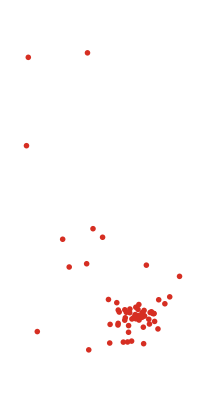
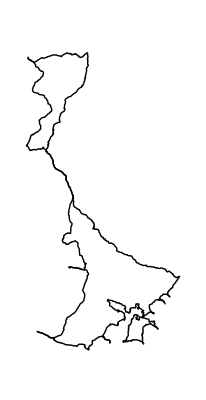
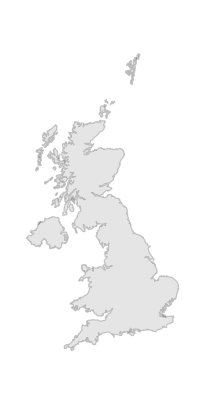
<|geoMarker→-Graphics-,travelDirections→-Graphics-,mapGraphic→-Graphics-|>

```mathematica
graphicsToProcess=<|"geoMarker"->geoMarkerGraphics,"travelDirections"->travelDirectionsGraphics,"mapGraphic"->mapGraphic|>
```

```mathematica
fullGraphicToProcess=Show[Sequence@@(graphicsToProcess//Values)];
```

```mathematica
testZZZ=DeleteCases[GroupBy[Cases[ImportString[ExportString[Show[geoMarkerGraphics],"SVG"],"XML"],XMLElement["path",___],{0,Infinity}],Lookup[#[[2]],"style"]&],HoldPattern["style"->_],{0,Infinity}];
```

```mathematica
testZZZ
```

<|stroke:none;fill-rule:evenodd;fill:rgb(83.921569%,18.039216%,13.333333%);fill-opacity:1;→{XMLElement[path,{d→M 96.925781 246.875 C 96.925781 247.296875 96.757812 247.703125 96.457031 248.003906 C 96.15625 248.300781 95.75 248.46875 95.328125 248.46875 C 94.902344 248.46875 94.5 248.300781 94.199219 248.003906 C 93.898438 247.703125 93.730469 247.296875 93.730469 246.875 C 93.730469 246.449219 93.898438 246.042969 94.199219 245.746094 C 94.5 245.445312 94.902344 245.277344 95.328125 245.277344 C 95.75 245.277344 96.15625 245.445312 96.457031 245.746094 C 96.757812 246.042969 96.925781 246.449219 96.925781 246.875 Z M 96.925781 246.875},{}],XMLElement[path,{d→M 109.230469 257.859375 C 109.230469 258.28125 109.0625 258.6875 108.761719 258.988281 C 108.460938 259.289062 108.054688 259.457031 107.632812 259.457031 C 107.207031 259.457031 106.800781 259.289062 106.503906 258.988281 C 106.203125 258.6875 106.035156 258.28125 106.035156 257.859375 C 106.035156 257.4375 106.203125 257.03125 106.503906 256.730469 C 106.800781 256.429688 107.207031 256.261719 107.632812 256.261719 C 108.054688 256.261719 108.460938 256.429688 108.761719 256.730469 C 109.0625 257.03125 109.230469 257.4375 109.230469 257.859375 Z M 109.230469 257.859375},{}],XMLElement[path,{d→M 165.476562 293.714844 C 165.476562 294.136719 165.308594 294.542969 165.007812 294.84375 C 164.710938 295.144531 164.304688 295.3125 163.878906 295.3125 C 163.457031 295.3125 163.050781 295.144531 162.75 294.84375 C 162.453125 294.542969 162.285156 294.136719 162.285156 293.714844 C 162.285156 293.292969 162.453125 292.886719 162.75 292.585938 C 163.050781 292.285156 163.457031 292.117188 163.878906 292.117188 C 164.304688 292.117188 164.710938 292.285156 165.007812 292.585938 C 165.308594 292.886719 165.476562 293.292969 165.476562 293.714844 Z M 165.476562 293.714844},{}],XMLElement[path,{d→M 208.105469 308.089844 C 208.105469 308.511719 207.9375 308.917969 207.636719 309.21875 C 207.335938 309.519531 206.929688 309.6875 206.507812 309.6875 C 206.085938 309.6875 205.679688 309.519531 205.378906 309.21875 C 205.078125 308.917969 204.910156 308.511719 204.910156 308.089844 C 204.910156 307.664062 205.078125 307.257812 205.378906 306.960938 C 205.679688 306.660156 206.085938 306.492188 206.507812 306.492188 C 206.929688 306.492188 207.335938 306.660156 207.636719 306.960938 C 207.9375 307.257812 208.105469 307.664062 208.105469 308.089844 Z M 208.105469 308.089844},{}],XMLElement[path,{d→M 195.496094 334.425781 C 195.496094 334.847656 195.328125 335.253906 195.027344 335.554688 C 194.730469 335.855469 194.324219 336.023438 193.898438 336.023438 C 193.476562 336.023438 193.070312 335.855469 192.769531 335.554688 C 192.46875 335.253906 192.300781 334.847656 192.300781 334.425781 C 192.300781 334 192.46875 333.59375 192.769531 333.296875 C 193.070312 332.996094 193.476562 332.828125 193.898438 332.828125 C 194.324219 332.828125 194.730469 332.996094 195.027344 333.296875 C 195.328125 333.59375 195.496094 334 195.496094 334.425781 Z M 195.496094 334.425781},{}],XMLElement[path,{d→M 189.265625 343.292969 C 189.265625 343.71875 189.097656 344.125 188.796875 344.421875 C 188.496094 344.722656 188.089844 344.890625 187.667969 344.890625 C 187.242188 344.890625 186.835938 344.722656 186.539062 344.421875 C 186.238281 344.125 186.070312 343.71875 186.070312 343.292969 C 186.070312 342.871094 186.238281 342.464844 186.539062 342.164062 C 186.835938 341.867188 187.242188 341.695312 187.667969 341.695312 C 188.089844 341.695312 188.496094 341.867188 188.796875 342.164062 C 189.097656 342.464844 189.265625 342.871094 189.265625 343.292969 Z M 189.265625 343.292969},{}],XMLElement[path,{d→M 181.347656 338.160156 C 181.347656 338.585938 181.179688 338.992188 180.878906 339.289062 C 180.582031 339.589844 180.175781 339.757812 179.75 339.757812 C 179.328125 339.757812 178.921875 339.589844 178.621094 339.289062 C 178.320312 338.992188 178.152344 338.585938 178.152344 338.160156 C 178.152344 337.738281 178.320312 337.332031 178.621094 337.03125 C 178.921875 336.730469 179.328125 336.5625 179.75 336.5625 C 180.175781 336.5625 180.582031 336.730469 180.878906 337.03125 C 181.179688 337.332031 181.347656 337.738281 181.347656 338.160156 Z M 181.347656 338.160156},{}],XMLElement[path,{d→M 175.394531 355.855469 C 175.394531 356.277344 175.226562 356.683594 174.925781 356.984375 C 174.628906 357.285156 174.222656 357.453125 173.796875 357.453125 C 173.375 357.453125 172.96875 357.285156 172.667969 356.984375 C 172.371094 356.683594 172.203125 356.277344 172.203125 355.855469 C 172.203125 355.433594 172.371094 355.027344 172.667969 354.726562 C 172.96875 354.425781 173.375 354.257812 173.796875 354.257812 C 174.222656 354.257812 174.628906 354.425781 174.925781 354.726562 C 175.226562 355.027344 175.394531 355.433594 175.394531 355.855469 Z M 175.394531 355.855469},{}],XMLElement[path,{d→M 174.847656 355.894531 C 174.847656 356.320312 174.679688 356.726562 174.378906 357.023438 C 174.078125 357.324219 173.671875 357.492188 173.25 357.492188 C 172.824219 357.492188 172.417969 357.324219 172.121094 357.023438 C 171.820312 356.726562 171.652344 356.320312 171.652344 355.894531 C 171.652344 355.472656 171.820312 355.066406 172.121094 354.765625 C 172.417969 354.46875 172.824219 354.296875 173.25 354.296875 C 173.671875 354.296875 174.078125 354.46875 174.378906 354.765625 C 174.679688 355.066406 174.847656 355.472656 174.847656 355.894531 Z M 174.847656 355.894531},{}],XMLElement[path,{d→M 173.71875 355.832031 C 173.71875 356.257812 173.546875 356.664062 173.25 356.960938 C 172.949219 357.261719 172.542969 357.429688 172.121094 357.429688 C 171.695312 357.429688 171.289062 357.261719 170.992188 356.960938 C 170.691406 356.664062 170.523438 356.257812 170.523438 355.832031 C 170.523438 355.410156 170.691406 355.003906 170.992188 354.703125 C 171.289062 354.402344 171.695312 354.234375 172.121094 354.234375 C 172.542969 354.234375 172.949219 354.402344 173.25 354.703125 C 173.546875 355.003906 173.71875 355.410156 173.71875 355.832031 Z M 173.71875 355.832031},{}],XMLElement[path,{d→M 172.035156 353.625 C 172.035156 354.046875 171.867188 354.453125 171.566406 354.753906 C 171.269531 355.054688 170.863281 355.222656 170.4375 355.222656 C 170.015625 355.222656 169.609375 355.054688 169.308594 354.753906 C 169.007812 354.453125 168.839844 354.046875 168.839844 353.625 C 168.839844 353.203125 169.007812 352.796875 169.308594 352.496094 C 169.609375 352.195312 170.015625 352.027344 170.4375 352.027344 C 170.863281 352.027344 171.269531 352.195312 171.566406 352.496094 C 171.867188 352.796875 172.035156 353.203125 172.035156 353.625 Z M 172.035156 353.625},{}],XMLElement[path,{d→M 170.339844 354.523438 C 170.339844 354.949219 170.171875 355.355469 169.875 355.652344 C 169.574219 355.953125 169.167969 356.121094 168.746094 356.121094 C 168.320312 356.121094 167.914062 355.953125 167.617188 355.652344 C 167.316406 355.355469 167.148438 354.949219 167.148438 354.523438 C 167.148438 354.101562 167.316406 353.695312 167.617188 353.394531 C 167.914062 353.09375 168.320312 352.925781 168.746094 352.925781 C 169.167969 352.925781 169.574219 353.09375 169.875 353.394531 C 170.171875 353.695312 170.339844 354.101562 170.339844 354.523438 Z M 170.339844 354.523438},{}],XMLElement[path,{d→M 168.621094 363.238281 C 168.621094 363.664062 168.453125 364.070312 168.152344 364.367188 C 167.855469 364.667969 167.449219 364.835938 167.023438 364.835938 C 166.601562 364.835938 166.195312 364.667969 165.894531 364.367188 C 165.59375 364.070312 165.425781 363.664062 165.425781 363.238281 C 165.425781 362.816406 165.59375 362.410156 165.894531 362.109375 C 166.195312 361.808594 166.601562 361.640625 167.023438 361.640625 C 167.449219 361.640625 167.855469 361.808594 168.152344 362.109375 C 168.453125 362.410156 168.621094 362.816406 168.621094 363.238281 Z M 168.621094 363.238281},{}],XMLElement[path,{d→M 176.078125 365.980469 C 176.078125 366.40625 175.910156 366.8125 175.609375 367.109375 C 175.308594 367.410156 174.902344 367.578125 174.480469 367.578125 C 174.054688 367.578125 173.648438 367.410156 173.351562 367.109375 C 173.050781 366.8125 172.882812 366.40625 172.882812 365.980469 C 172.882812 365.558594 173.050781 365.152344 173.351562 364.851562 C 173.648438 364.554688 174.054688 364.386719 174.480469 364.386719 C 174.902344 364.386719 175.308594 364.554688 175.609375 364.851562 C 175.910156 365.152344 176.078125 365.558594 176.078125 365.980469 Z M 176.078125 365.980469},{}],XMLElement[path,{d→M 180.382812 375.617188 C 180.382812 376.042969 180.214844 376.449219 179.914062 376.746094 C 179.613281 377.046875 179.207031 377.214844 178.785156 377.214844 C 178.359375 377.214844 177.953125 377.046875 177.65625 376.746094 C 177.355469 376.449219 177.1875 376.042969 177.1875 375.617188 C 177.1875 375.195312 177.355469 374.789062 177.65625 374.488281 C 177.953125 374.191406 178.359375 374.023438 178.785156 374.023438 C 179.207031 374.023438 179.613281 374.191406 179.914062 374.488281 C 180.214844 374.789062 180.382812 375.195312 180.382812 375.617188 Z M 180.382812 375.617188},{}],XMLElement[path,{d→M 169.457031 369.339844 C 169.457031 369.761719 169.289062 370.167969 168.988281 370.46875 C 168.691406 370.765625 168.285156 370.933594 167.859375 370.933594 C 167.4375 370.933594 167.03125 370.765625 166.730469 370.46875 C 166.429688 370.167969 166.261719 369.761719 166.261719 369.339844 C 166.261719 368.914062 166.429688 368.507812 166.730469 368.210938 C 167.03125 367.910156 167.4375 367.742188 167.859375 367.742188 C 168.285156 367.742188 168.691406 367.910156 168.988281 368.210938 C 169.289062 368.507812 169.457031 368.914062 169.457031 369.339844 Z M 169.457031 369.339844},{}],XMLElement[path,{d→M 161.582031 373.390625 C 161.582031 373.8125 161.414062 374.21875 161.113281 374.519531 C 160.816406 374.820312 160.410156 374.988281 159.984375 374.988281 C 159.5625 374.988281 159.15625 374.820312 158.855469 374.519531 C 158.558594 374.21875 158.386719 373.8125 158.386719 373.390625 C 158.386719 372.96875 158.558594 372.5625 158.855469 372.261719 C 159.15625 371.960938 159.5625 371.792969 159.984375 371.792969 C 160.410156 371.792969 160.816406 371.960938 161.113281 372.261719 C 161.414062 372.5625 161.582031 372.96875 161.582031 373.390625 Z M 161.582031 373.390625},{}],XMLElement[path,{d→M 161.992188 394.601562 C 161.992188 395.023438 161.820312 395.429688 161.523438 395.730469 C 161.222656 396.027344 160.816406 396.195312 160.394531 396.195312 C 159.96875 396.195312 159.5625 396.027344 159.265625 395.730469 C 158.964844 395.429688 158.796875 395.023438 158.796875 394.601562 C 158.796875 394.175781 158.964844 393.769531 159.265625 393.472656 C 159.5625 393.171875 159.96875 393.003906 160.394531 393.003906 C 160.816406 393.003906 161.222656 393.171875 161.523438 393.472656 C 161.820312 393.769531 161.992188 394.175781 161.992188 394.601562 Z M 161.992188 394.601562},{}],XMLElement[path,{d→M 146.511719 391.292969 C 146.511719 391.714844 146.34375 392.121094 146.042969 392.421875 C 145.742188 392.722656 145.335938 392.890625 144.914062 392.890625 C 144.492188 392.890625 144.085938 392.722656 143.785156 392.421875 C 143.484375 392.121094 143.316406 391.714844 143.316406 391.292969 C 143.316406 390.867188 143.484375 390.460938 143.785156 390.164062 C 144.085938 389.863281 144.492188 389.695312 144.914062 389.695312 C 145.335938 389.695312 145.742188 389.863281 146.042969 390.164062 C 146.34375 390.460938 146.511719 390.867188 146.511719 391.292969 Z M 146.511719 391.292969},{}],XMLElement[path,{d→M 141.347656 392.398438 C 141.347656 392.820312 141.179688 393.226562 140.878906 393.527344 C 140.578125 393.824219 140.171875 393.992188 139.75 393.992188 C 139.324219 393.992188 138.917969 393.824219 138.621094 393.527344 C 138.320312 393.226562 138.152344 392.820312 138.152344 392.398438 C 138.152344 391.972656 138.320312 391.566406 138.621094 391.269531 C 138.917969 390.96875 139.324219 390.800781 139.75 390.800781 C 140.171875 390.800781 140.578125 390.96875 140.878906 391.269531 C 141.179688 391.566406 141.347656 391.972656 141.347656 392.398438 Z M 141.347656 392.398438},{}],XMLElement[path,{d→M 135.90625 392.5625 C 135.90625 392.988281 135.738281 393.394531 135.441406 393.691406 C 135.140625 393.992188 134.734375 394.160156 134.308594 394.160156 C 133.886719 394.160156 133.480469 393.992188 133.179688 393.691406 C 132.882812 393.394531 132.714844 392.988281 132.714844 392.5625 C 132.714844 392.140625 132.882812 391.734375 133.179688 391.433594 C 133.480469 391.136719 133.886719 390.964844 134.308594 390.964844 C 134.734375 390.964844 135.140625 391.136719 135.441406 391.433594 C 135.738281 391.734375 135.90625 392.140625 135.90625 392.5625 Z M 135.90625 392.5625},{}],XMLElement[path,{d→M 142.574219 379.894531 C 142.574219 380.320312 142.402344 380.726562 142.105469 381.023438 C 141.804688 381.324219 141.398438 381.492188 140.976562 381.492188 C 140.550781 381.492188 140.144531 381.324219 139.847656 381.023438 C 139.546875 380.726562 139.378906 380.320312 139.378906 379.894531 C 139.378906 379.472656 139.546875 379.066406 139.847656 378.765625 C 140.144531 378.46875 140.550781 378.296875 140.976562 378.296875 C 141.398438 378.296875 141.804688 378.46875 142.105469 378.765625 C 142.402344 379.066406 142.574219 379.472656 142.574219 379.894531 Z M 142.574219 379.894531},{}],XMLElement[path,{d→M 142.648438 371.371094 C 142.648438 371.796875 142.480469 372.203125 142.179688 372.5 C 141.882812 372.800781 141.476562 372.96875 141.050781 372.96875 C 140.628906 372.96875 140.222656 372.800781 139.921875 372.5 C 139.621094 372.203125 139.453125 371.796875 139.453125 371.371094 C 139.453125 370.949219 139.621094 370.542969 139.921875 370.242188 C 140.222656 369.945312 140.628906 369.777344 141.050781 369.777344 C 141.476562 369.777344 141.882812 369.945312 142.179688 370.242188 C 142.480469 370.542969 142.648438 370.949219 142.648438 371.371094 Z M 142.648438 371.371094},{}],XMLElement[path,{d→M 146.902344 362.847656 C 146.902344 363.269531 146.734375 363.675781 146.4375 363.976562 C 146.136719 364.277344 145.730469 364.445312 145.308594 364.445312 C 144.882812 364.445312 144.476562 364.277344 144.179688 363.976562 C 143.878906 363.675781 143.710938 363.269531 143.710938 362.847656 C 143.710938 362.425781 143.878906 362.019531 144.179688 361.71875 C 144.476562 361.417969 144.882812 361.25 145.308594 361.25 C 145.730469 361.25 146.136719 361.417969 146.4375 361.71875 C 146.734375 362.019531 146.902344 362.425781 146.902344 362.847656 Z M 146.902344 362.847656},{}],XMLElement[path,{d→M 148.945312 361.324219 C 148.945312 361.75 148.777344 362.15625 148.480469 362.453125 C 148.179688 362.753906 147.773438 362.921875 147.351562 362.921875 C 146.925781 362.921875 146.519531 362.753906 146.222656 362.453125 C 145.921875 362.15625 145.753906 361.75 145.753906 361.324219 C 145.753906 360.902344 145.921875 360.496094 146.222656 360.195312 C 146.519531 359.898438 146.925781 359.730469 147.351562 359.730469 C 147.773438 359.730469 148.179688 359.898438 148.480469 360.195312 C 148.777344 360.496094 148.945312 360.902344 148.945312 361.324219 Z M 148.945312 361.324219},{}],XMLElement[path,{d→M 151.035156 358.320312 C 151.035156 358.746094 150.867188 359.152344 150.566406 359.453125 C 150.265625 359.75 149.859375 359.917969 149.4375 359.917969 C 149.011719 359.917969 148.605469 359.75 148.308594 359.453125 C 148.007812 359.152344 147.839844 358.746094 147.839844 358.320312 C 147.839844 357.898438 148.007812 357.492188 148.308594 357.191406 C 148.605469 356.894531 149.011719 356.726562 149.4375 356.726562 C 149.859375 356.726562 150.265625 356.894531 150.566406 357.191406 C 150.867188 357.492188 151.035156 357.898438 151.035156 358.320312 Z M 151.035156 358.320312},{}],XMLElement[path,{d→M 151.210938 357.207031 C 151.210938 357.628906 151.042969 358.035156 150.742188 358.335938 C 150.445312 358.632812 150.039062 358.800781 149.613281 358.800781 C 149.191406 358.800781 148.785156 358.632812 148.484375 358.335938 C 148.1875 358.035156 148.019531 357.628906 148.019531 357.207031 C 148.019531 356.78125 148.1875 356.375 148.484375 356.078125 C 148.785156 355.777344 149.191406 355.609375 149.613281 355.609375 C 150.039062 355.609375 150.445312 355.777344 150.742188 356.078125 C 151.042969 356.375 151.210938 356.78125 151.210938 357.207031 Z M 151.210938 357.207031},{}],XMLElement[path,{d→M 155.101562 358.425781 C 155.101562 358.847656 154.933594 359.253906 154.632812 359.554688 C 154.332031 359.851562 153.925781 360.019531 153.503906 360.019531 C 153.082031 360.019531 152.675781 359.851562 152.375 359.554688 C 152.074219 359.253906 151.90625 358.847656 151.90625 358.425781 C 151.90625 358 152.074219 357.59375 152.375 357.292969 C 152.675781 356.996094 153.082031 356.828125 153.503906 356.828125 C 153.925781 356.828125 154.332031 356.996094 154.632812 357.292969 C 154.933594 357.59375 155.101562 358 155.101562 358.425781 Z M 155.101562 358.425781},{}],XMLElement[path,{d→M 154.695312 360.417969 C 154.695312 360.84375 154.527344 361.25 154.226562 361.546875 C 153.925781 361.847656 153.519531 362.015625 153.097656 362.015625 C 152.675781 362.015625 152.269531 361.847656 151.96875 361.546875 C 151.667969 361.25 151.5 360.84375 151.5 360.417969 C 151.5 359.996094 151.667969 359.589844 151.96875 359.289062 C 152.269531 358.988281 152.675781 358.820312 153.097656 358.820312 C 153.519531 358.820312 153.925781 358.988281 154.226562 359.289062 C 154.527344 359.589844 154.695312 359.996094 154.695312 360.417969 Z M 154.695312 360.417969},{}],XMLElement[path,{d→M 152.039062 362.644531 C 152.039062 363.066406 151.871094 363.472656 151.574219 363.773438 C 151.273438 364.070312 150.867188 364.238281 150.445312 364.238281 C 150.019531 364.238281 149.613281 364.070312 149.3125 363.773438 C 149.015625 363.472656 148.847656 363.066406 148.847656 362.644531 C 148.847656 362.21875 149.015625 361.8125 149.3125 361.515625 C 149.613281 361.214844 150.019531 361.046875 150.445312 361.046875 C 150.867188 361.046875 151.273438 361.214844 151.574219 361.515625 C 151.871094 361.8125 152.039062 362.21875 152.039062 362.644531 Z M 152.039062 362.644531},{}],XMLElement[path,{d→M 156.105469 364.238281 C 156.105469 364.664062 155.9375 365.070312 155.636719 365.367188 C 155.339844 365.667969 154.933594 365.835938 154.507812 365.835938 C 154.085938 365.835938 153.679688 365.667969 153.378906 365.367188 C 153.082031 365.070312 152.910156 364.664062 152.910156 364.238281 C 152.910156 363.816406 153.082031 363.410156 153.378906 363.109375 C 153.679688 362.808594 154.085938 362.640625 154.507812 362.640625 C 154.933594 362.640625 155.339844 362.808594 155.636719 363.109375 C 155.9375 363.410156 156.105469 363.816406 156.105469 364.238281 Z M 156.105469 364.238281},{}],XMLElement[path,{d→M 157.398438 360.089844 C 157.398438 360.515625 157.230469 360.921875 156.929688 361.21875 C 156.632812 361.519531 156.226562 361.6875 155.800781 361.6875 C 155.378906 361.6875 154.972656 361.519531 154.671875 361.21875 C 154.375 360.921875 154.207031 360.515625 154.207031 360.089844 C 154.207031 359.667969 154.375 359.261719 154.671875 358.960938 C 154.972656 358.664062 155.378906 358.496094 155.800781 358.496094 C 156.226562 358.496094 156.632812 358.664062 156.929688 358.960938 C 157.230469 359.261719 157.398438 359.667969 157.398438 360.089844 Z M 157.398438 360.089844},{}],XMLElement[path,{d→M 159.859375 360.746094 C 159.859375 361.171875 159.691406 361.578125 159.390625 361.878906 C 159.089844 362.175781 158.683594 362.34375 158.261719 362.34375 C 157.839844 362.34375 157.433594 362.175781 157.132812 361.878906 C 156.832031 361.578125 156.664062 361.171875 156.664062 360.746094 C 156.664062 360.324219 156.832031 359.917969 157.132812 359.617188 C 157.433594 359.320312 157.839844 359.152344 158.261719 359.152344 C 158.683594 359.152344 159.089844 359.320312 159.390625 359.617188 C 159.691406 359.917969 159.859375 360.324219 159.859375 360.746094 Z M 159.859375 360.746094},{}],XMLElement[path,{d→M 163.21875 359.132812 C 163.21875 359.554688 163.050781 359.960938 162.75 360.261719 C 162.453125 360.5625 162.046875 360.730469 161.621094 360.730469 C 161.199219 360.730469 160.792969 360.5625 160.492188 360.261719 C 160.195312 359.960938 160.023438 359.554688 160.023438 359.132812 C 160.023438 358.710938 160.195312 358.304688 160.492188 358.003906 C 160.792969 357.703125 161.199219 357.535156 161.621094 357.535156 C 162.046875 357.535156 162.453125 357.703125 162.75 358.003906 C 163.050781 358.304688 163.21875 358.710938 163.21875 359.132812 Z M 163.21875 359.132812},{}],XMLElement[path,{d→M 162.003906 358.570312 C 162.003906 358.992188 161.835938 359.398438 161.535156 359.699219 C 161.234375 359.996094 160.828125 360.167969 160.40625 360.167969 C 159.980469 360.167969 159.574219 359.996094 159.277344 359.699219 C 158.976562 359.398438 158.808594 358.992188 158.808594 358.570312 C 158.808594 358.144531 158.976562 357.738281 159.277344 357.441406 C 159.574219 357.140625 159.980469 356.972656 160.40625 356.972656 C 160.828125 356.972656 161.234375 357.140625 161.535156 357.441406 C 161.835938 357.738281 162.003906 358.144531 162.003906 358.570312 Z M 162.003906 358.570312},{}],XMLElement[path,{d→M 160.859375 355.003906 C 160.859375 355.425781 160.691406 355.832031 160.394531 356.132812 C 160.09375 356.433594 159.6875 356.601562 159.265625 356.601562 C 158.839844 356.601562 158.433594 356.433594 158.136719 356.132812 C 157.835938 355.832031 157.667969 355.425781 157.667969 355.003906 C 157.667969 354.582031 157.835938 354.175781 158.136719 353.875 C 158.433594 353.574219 158.839844 353.40625 159.265625 353.40625 C 159.6875 353.40625 160.09375 353.574219 160.394531 353.875 C 160.691406 354.175781 160.859375 354.582031 160.859375 355.003906 Z M 160.859375 355.003906},{}],XMLElement[path,{d→M 159.902344 354.773438 C 159.902344 355.195312 159.734375 355.601562 159.433594 355.902344 C 159.132812 356.199219 158.726562 356.367188 158.304688 356.367188 C 157.878906 356.367188 157.472656 356.199219 157.175781 355.902344 C 156.875 355.601562 156.707031 355.195312 156.707031 354.773438 C 156.707031 354.347656 156.875 353.941406 157.175781 353.644531 C 157.472656 353.34375 157.878906 353.175781 158.304688 353.175781 C 158.726562 353.175781 159.132812 353.34375 159.433594 353.644531 C 159.734375 353.941406 159.902344 354.347656 159.902344 354.773438 Z M 159.902344 354.773438},{}],XMLElement[path,{d→M 162.578125 351.8125 C 162.578125 352.238281 162.410156 352.644531 162.109375 352.945312 C 161.808594 353.242188 161.402344 353.410156 160.980469 353.410156 C 160.554688 353.410156 160.148438 353.242188 159.851562 352.945312 C 159.550781 352.644531 159.382812 352.238281 159.382812 351.8125 C 159.382812 351.390625 159.550781 350.984375 159.851562 350.683594 C 160.148438 350.386719 160.554688 350.21875 160.980469 350.21875 C 161.402344 350.21875 161.808594 350.386719 162.109375 350.683594 C 162.410156 350.984375 162.578125 351.390625 162.578125 351.8125 Z M 162.578125 351.8125},{}],XMLElement[path,{d→M 154.703125 350.515625 C 154.703125 350.9375 154.535156 351.34375 154.238281 351.644531 C 153.9375 351.945312 153.53125 352.113281 153.109375 352.113281 C 152.683594 352.113281 152.277344 351.945312 151.980469 351.644531 C 151.679688 351.34375 151.511719 350.9375 151.511719 350.515625 C 151.511719 350.089844 151.679688 349.683594 151.980469 349.386719 C 152.277344 349.085938 152.683594 348.917969 153.109375 348.917969 C 153.53125 348.917969 153.9375 349.085938 154.238281 349.386719 C 154.535156 349.683594 154.703125 350.089844 154.703125 350.515625 Z M 154.703125 350.515625},{}],XMLElement[path,{d→M 155.839844 344.28125 C 155.839844 344.707031 155.671875 345.113281 155.371094 345.410156 C 155.070312 345.710938 154.664062 345.878906 154.242188 345.878906 C 153.820312 345.878906 153.414062 345.710938 153.113281 345.410156 C 152.8125 345.113281 152.644531 344.707031 152.644531 344.28125 C 152.644531 343.859375 152.8125 343.453125 153.113281 343.152344 C 153.414062 342.855469 153.820312 342.6875 154.242188 342.6875 C 154.664062 342.6875 155.070312 342.855469 155.371094 343.152344 C 155.671875 343.453125 155.839844 343.859375 155.839844 344.28125 Z M 155.839844 344.28125},{}],XMLElement[path,{d→M 151.921875 347.753906 C 151.921875 348.175781 151.753906 348.582031 151.453125 348.882812 C 151.15625 349.183594 150.75 349.351562 150.324219 349.351562 C 149.902344 349.351562 149.496094 349.183594 149.195312 348.882812 C 148.898438 348.582031 148.726562 348.175781 148.726562 347.753906 C 148.726562 347.328125 148.898438 346.921875 149.195312 346.625 C 149.496094 346.324219 149.902344 346.15625 150.324219 346.15625 C 150.75 346.15625 151.15625 346.324219 151.453125 346.625 C 151.753906 346.921875 151.921875 347.328125 151.921875 347.753906 Z M 151.921875 347.753906},{}],XMLElement[path,{d→M 144.3125 350.0625 C 144.3125 350.488281 144.144531 350.894531 143.847656 351.191406 C 143.546875 351.492188 143.140625 351.660156 142.71875 351.660156 C 142.292969 351.660156 141.886719 351.492188 141.589844 351.191406 C 141.289062 350.894531 141.121094 350.488281 141.121094 350.0625 C 141.121094 349.640625 141.289062 349.234375 141.589844 348.933594 C 141.886719 348.632812 142.292969 348.464844 142.71875 348.464844 C 143.140625 348.464844 143.546875 348.632812 143.847656 348.933594 C 144.144531 349.234375 144.3125 349.640625 144.3125 350.0625 Z M 144.3125 350.0625},{}],XMLElement[path,{d→M 144.132812 354.800781 C 144.132812 355.222656 143.964844 355.628906 143.664062 355.929688 C 143.363281 356.226562 142.957031 356.394531 142.535156 356.394531 C 142.109375 356.394531 141.703125 356.226562 141.40625 355.929688 C 141.105469 355.628906 140.9375 355.222656 140.9375 354.800781 C 140.9375 354.375 141.105469 353.96875 141.40625 353.671875 C 141.703125 353.371094 142.109375 353.203125 142.535156 353.203125 C 142.957031 353.203125 143.363281 353.371094 143.664062 353.671875 C 143.964844 353.96875 144.132812 354.375 144.132812 354.800781 Z M 144.132812 354.800781},{}],XMLElement[path,{d→M 139.707031 354.273438 C 139.707031 354.695312 139.539062 355.101562 139.238281 355.402344 C 138.9375 355.703125 138.53125 355.871094 138.109375 355.871094 C 137.6875 355.871094 137.28125 355.703125 136.980469 355.402344 C 136.679688 355.101562 136.511719 354.695312 136.511719 354.273438 C 136.511719 353.847656 136.679688 353.441406 136.980469 353.144531 C 137.28125 352.84375 137.6875 352.675781 138.109375 352.675781 C 138.53125 352.675781 138.9375 352.84375 139.238281 353.144531 C 139.539062 353.441406 139.707031 353.847656 139.707031 354.273438 Z M 139.707031 354.273438},{}],XMLElement[path,{d→M 137.789062 351.039062 C 137.789062 351.464844 137.621094 351.871094 137.320312 352.167969 C 137.019531 352.46875 136.613281 352.636719 136.191406 352.636719 C 135.769531 352.636719 135.363281 352.46875 135.0625 352.167969 C 134.761719 351.871094 134.59375 351.464844 134.59375 351.039062 C 134.59375 350.617188 134.761719 350.210938 135.0625 349.910156 C 135.363281 349.609375 135.769531 349.441406 136.191406 349.441406 C 136.613281 349.441406 137.019531 349.609375 137.320312 349.910156 C 137.621094 350.210938 137.789062 350.617188 137.789062 351.039062 Z M 137.789062 351.039062},{}],XMLElement[path,{d→M 127.492188 341.902344 C 127.492188 342.328125 127.324219 342.734375 127.023438 343.03125 C 126.722656 343.332031 126.316406 343.5 125.894531 343.5 C 125.472656 343.5 125.066406 343.332031 124.765625 343.03125 C 124.464844 342.734375 124.296875 342.328125 124.296875 341.902344 C 124.296875 341.480469 124.464844 341.074219 124.765625 340.773438 C 125.066406 340.476562 125.472656 340.308594 125.894531 340.308594 C 126.316406 340.308594 126.722656 340.476562 127.023438 340.773438 C 127.324219 341.074219 127.492188 341.480469 127.492188 341.902344 Z M 127.492188 341.902344},{}],XMLElement[path,{d→M 116.78125 337.8125 C 116.78125 338.234375 116.613281 338.640625 116.316406 338.941406 C 116.015625 339.242188 115.609375 339.410156 115.1875 339.410156 C 114.761719 339.410156 114.355469 339.242188 114.054688 338.941406 C 113.757812 338.640625 113.589844 338.234375 113.589844 337.8125 C 113.589844 337.386719 113.757812 336.980469 114.054688 336.683594 C 114.355469 336.382812 114.761719 336.214844 115.1875 336.214844 C 115.609375 336.214844 116.015625 336.382812 116.316406 336.683594 C 116.613281 336.980469 116.78125 337.386719 116.78125 337.8125 Z M 116.78125 337.8125},{}],XMLElement[path,{d→M 129.339844 351.363281 C 129.339844 351.785156 129.171875 352.191406 128.871094 352.492188 C 128.574219 352.789062 128.167969 352.957031 127.742188 352.957031 C 127.320312 352.957031 126.914062 352.789062 126.613281 352.492188 C 126.316406 352.191406 126.148438 351.785156 126.148438 351.363281 C 126.148438 350.9375 126.316406 350.53125 126.613281 350.230469 C 126.914062 349.933594 127.320312 349.765625 127.742188 349.765625 C 128.167969 349.765625 128.574219 349.933594 128.871094 350.230469 C 129.171875 350.53125 129.339844 350.9375 129.339844 351.363281 Z M 129.339844 351.363281},{}],XMLElement[path,{d→M 130.609375 353.945312 C 130.609375 354.367188 130.441406 354.773438 130.144531 355.074219 C 129.84375 355.375 129.4375 355.542969 129.015625 355.542969 C 128.589844 355.542969 128.183594 355.375 127.886719 355.074219 C 127.585938 354.773438 127.417969 354.367188 127.417969 353.945312 C 127.417969 353.519531 127.585938 353.113281 127.886719 352.816406 C 128.183594 352.515625 128.589844 352.347656 129.015625 352.347656 C 129.4375 352.347656 129.84375 352.515625 130.144531 352.816406 C 130.441406 353.113281 130.609375 353.519531 130.609375 353.945312 Z M 130.609375 353.945312},{}],XMLElement[path,{d→M 138.390625 361.285156 C 138.390625 361.710938 138.222656 362.117188 137.921875 362.414062 C 137.625 362.714844 137.21875 362.882812 136.792969 362.882812 C 136.371094 362.882812 135.964844 362.714844 135.664062 362.414062 C 135.363281 362.117188 135.195312 361.710938 135.195312 361.285156 C 135.195312 360.863281 135.363281 360.457031 135.664062 360.15625 C 135.964844 359.855469 136.371094 359.6875 136.792969 359.6875 C 137.21875 359.6875 137.625 359.855469 137.921875 360.15625 C 138.222656 360.457031 138.390625 360.863281 138.390625 361.285156 Z M 138.390625 361.285156},{}],XMLElement[path,{d→M 137.699219 364.398438 C 137.699219 364.820312 137.53125 365.226562 137.230469 365.527344 C 136.933594 365.828125 136.527344 365.996094 136.101562 365.996094 C 135.679688 365.996094 135.273438 365.828125 134.972656 365.527344 C 134.671875 365.226562 134.503906 364.820312 134.503906 364.398438 C 134.503906 363.972656 134.671875 363.566406 134.972656 363.269531 C 135.273438 362.96875 135.679688 362.800781 136.101562 362.800781 C 136.527344 362.800781 136.933594 362.96875 137.230469 363.269531 C 137.53125 363.566406 137.699219 363.972656 137.699219 364.398438 Z M 137.699219 364.398438},{}],XMLElement[path,{d→M 129.253906 368.472656 C 129.253906 368.894531 129.082031 369.300781 128.785156 369.601562 C 128.484375 369.898438 128.078125 370.066406 127.65625 370.066406 C 127.230469 370.066406 126.824219 369.898438 126.527344 369.601562 C 126.226562 369.300781 126.058594 368.894531 126.058594 368.472656 C 126.058594 368.046875 126.226562 367.640625 126.527344 367.34375 C 126.824219 367.042969 127.230469 366.875 127.65625 366.875 C 128.078125 366.875 128.484375 367.042969 128.785156 367.34375 C 129.082031 367.640625 129.253906 368.046875 129.253906 368.472656 Z M 129.253906 368.472656},{}],XMLElement[path,{d→M 128.980469 370.578125 C 128.980469 371.003906 128.8125 371.410156 128.511719 371.707031 C 128.214844 372.007812 127.808594 372.175781 127.382812 372.175781 C 126.960938 372.175781 126.554688 372.007812 126.253906 371.707031 C 125.957031 371.410156 125.785156 371.003906 125.785156 370.578125 C 125.785156 370.15625 125.957031 369.75 126.253906 369.449219 C 126.554688 369.152344 126.960938 368.984375 127.382812 368.984375 C 127.808594 368.984375 128.214844 369.152344 128.511719 369.449219 C 128.8125 369.75 128.980469 370.15625 128.980469 370.578125 Z M 128.980469 370.578125},{}],XMLElement[path,{d→M 118.894531 369.796875 C 118.894531 370.21875 118.726562 370.625 118.425781 370.925781 C 118.125 371.222656 117.71875 371.394531 117.296875 371.394531 C 116.875 371.394531 116.46875 371.222656 116.167969 370.925781 C 115.867188 370.625 115.699219 370.21875 115.699219 369.796875 C 115.699219 369.371094 115.867188 368.964844 116.167969 368.667969 C 116.46875 368.367188 116.875 368.199219 117.296875 368.199219 C 117.71875 368.199219 118.125 368.367188 118.425781 368.667969 C 118.726562 368.964844 118.894531 369.371094 118.894531 369.796875 Z M 118.894531 369.796875},{}],XMLElement[path,{d→M 118.40625 393.75 C 118.40625 394.171875 118.238281 394.578125 117.9375 394.878906 C 117.636719 395.175781 117.230469 395.34375 116.808594 395.34375 C 116.382812 395.34375 115.976562 395.175781 115.679688 394.878906 C 115.378906 394.578125 115.210938 394.171875 115.210938 393.75 C 115.210938 393.324219 115.378906 392.917969 115.679688 392.617188 C 115.976562 392.320312 116.382812 392.152344 116.808594 392.152344 C 117.230469 392.152344 117.636719 392.320312 117.9375 392.617188 C 118.238281 392.917969 118.40625 393.324219 118.40625 393.75 Z M 118.40625 393.75},{}],XMLElement[path,{d→M 91.464844 402.511719 C 91.464844 402.9375 91.292969 403.34375 90.996094 403.644531 C 90.695312 403.941406 90.289062 404.109375 89.867188 404.109375 C 89.441406 404.109375 89.035156 403.941406 88.738281 403.644531 C 88.4375 403.34375 88.269531 402.9375 88.269531 402.511719 C 88.269531 402.089844 88.4375 401.683594 88.738281 401.382812 C 89.035156 401.085938 89.441406 400.917969 89.867188 400.917969 C 90.289062 400.917969 90.695312 401.085938 90.996094 401.382812 C 91.292969 401.683594 91.464844 402.089844 91.464844 402.511719 Z M 91.464844 402.511719},{}],XMLElement[path,{d→M 25.328125 379.042969 C 25.328125 379.46875 25.160156 379.875 24.859375 380.175781 C 24.558594 380.472656 24.152344 380.640625 23.730469 380.640625 C 23.308594 380.640625 22.902344 380.472656 22.601562 380.175781 C 22.300781 379.875 22.132812 379.46875 22.132812 379.042969 C 22.132812 378.621094 22.300781 378.214844 22.601562 377.914062 C 22.902344 377.617188 23.308594 377.449219 23.730469 377.449219 C 24.152344 377.449219 24.558594 377.617188 24.859375 377.914062 C 25.160156 378.214844 25.328125 378.621094 25.328125 379.042969 Z M 25.328125 379.042969},{}],XMLElement[path,{d→M 66.339844 296.085938 C 66.339844 296.511719 66.171875 296.917969 65.871094 297.214844 C 65.570312 297.515625 65.164062 297.683594 64.742188 297.683594 C 64.320312 297.683594 63.914062 297.515625 63.613281 297.214844 C 63.3125 296.917969 63.144531 296.511719 63.144531 296.085938 C 63.144531 295.664062 63.3125 295.257812 63.613281 294.957031 C 63.914062 294.660156 64.320312 294.492188 64.742188 294.492188 C 65.164062 294.492188 65.570312 294.660156 65.871094 294.957031 C 66.171875 295.257812 66.339844 295.664062 66.339844 296.085938 Z M 66.339844 296.085938},{}],XMLElement[path,{d→M 88.757812 291.902344 C 88.757812 292.324219 88.589844 292.730469 88.292969 293.03125 C 87.992188 293.328125 87.585938 293.496094 87.160156 293.496094 C 86.738281 293.496094 86.332031 293.328125 86.03125 293.03125 C 85.734375 292.730469 85.566406 292.324219 85.566406 291.902344 C 85.566406 291.476562 85.734375 291.070312 86.03125 290.773438 C 86.332031 290.472656 86.738281 290.304688 87.160156 290.304688 C 87.585938 290.304688 87.992188 290.472656 88.292969 290.773438 C 88.589844 291.070312 88.757812 291.476562 88.757812 291.902344 Z M 88.757812 291.902344},{}],XMLElement[path,{d→M 57.945312 260.417969 C 57.945312 260.839844 57.777344 261.246094 57.476562 261.546875 C 57.175781 261.84375 56.769531 262.015625 56.347656 262.015625 C 55.925781 262.015625 55.519531 261.84375 55.21875 261.546875 C 54.917969 261.246094 54.75 260.839844 54.75 260.417969 C 54.75 259.992188 54.917969 259.585938 55.21875 259.289062 C 55.519531 258.988281 55.925781 258.820312 56.347656 258.820312 C 56.769531 258.820312 57.175781 258.988281 57.476562 259.289062 C 57.777344 259.585938 57.945312 259.992188 57.945312 260.417969 Z M 57.945312 260.417969},{}],XMLElement[path,{d→M 11.429688 140.242188 C 11.429688 140.664062 11.261719 141.070312 10.960938 141.371094 C 10.664062 141.667969 10.257812 141.835938 9.832031 141.835938 C 9.410156 141.835938 9.003906 141.667969 8.703125 141.371094 C 8.40625 141.070312 8.238281 140.664062 8.238281 140.242188 C 8.238281 139.816406 8.40625 139.410156 8.703125 139.109375 C 9.003906 138.8125 9.410156 138.644531 9.832031 138.644531 C 10.257812 138.644531 10.664062 138.8125 10.960938 139.109375 C 11.261719 139.410156 11.429688 139.816406 11.429688 140.242188 Z M 11.429688 140.242188},{}],XMLElement[path,{d→M 13.777344 26.707031 C 13.777344 27.132812 13.609375 27.539062 13.308594 27.835938 C 13.007812 28.136719 12.601562 28.304688 12.179688 28.304688 C 11.753906 28.304688 11.347656 28.136719 11.050781 27.835938 C 10.75 27.539062 10.582031 27.132812 10.582031 26.707031 C 10.582031 26.285156 10.75 25.878906 11.050781 25.578125 C 11.347656 25.277344 11.753906 25.109375 12.179688 25.109375 C 12.601562 25.109375 13.007812 25.277344 13.308594 25.578125 C 13.609375 25.878906 13.777344 26.285156 13.777344 26.707031 Z M 13.777344 26.707031},{}],XMLElement[path,{d→M 89.828125 20.945312 C 89.828125 21.367188 89.660156 21.773438 89.363281 22.074219 C 89.0625 22.371094 88.65625 22.542969 88.234375 22.542969 C 87.808594 22.542969 87.402344 22.371094 87.105469 22.074219 C 86.804688 21.773438 86.636719 21.367188 86.636719 20.945312 C 86.636719 20.519531 86.804688 20.113281 87.105469 19.816406 C 87.402344 19.515625 87.808594 19.347656 88.234375 19.347656 C 88.65625 19.347656 89.0625 19.515625 89.363281 19.816406 C 89.660156 20.113281 89.828125 20.519531 89.828125 20.945312 Z M 89.828125 20.945312},{}]}|>

```mathematica
testZZZ["path",{"d"->"M 96.925781 246.875 C 96.925781 247.296875 96.757812 247.703125 96.457031 248.003906 C 96.15625 248.300781 95.75 248.46875 95.328125 248.46875 C 94.902344 248.46875 94.5 248.300781 94.199219 248.003906 C 93.898438 247.703125 93.730469 247.296875 93.730469 246.875 C 93.730469 246.449219 93.898438 246.042969 94.199219 245.746094 C 94.5 245.445312 94.902344 245.277344 95.328125 245.277344 C 95.75 245.277344 96.15625 245.445312 96.457031 245.746094 C 96.757812 246.042969 96.925781 246.449219 96.925781 246.875 Z M 96.925781 246.875"},{}]/.x_XMLElement:>ExportString[x,"XML"]
```

<path d='M 96.925781 246.875 C 96.925781 247.296875 96.757812 247.703125 96.457031 248.003906 C 96.15625 248.300781 95.75 248.46875 95.328125 248.46875 C 94.902344 248.46875 94.5 248.300781 94.199219 248.003906 C 93.898438 247.703125 93.730469 247.296875 93.730469 246.875 C 93.730469 246.449219 93.898438 246.042969 94.199219 245.746094 C 94.5 245.445312 94.902344 245.277344 95.328125 245.277344 C 95.75 245.277344 96.15625 245.445312 96.457031 245.746094 C 96.757812 246.042969 96.925781 246.449219 96.925781 246.875 Z M 96.925781 246.875' />

```mathematica
ExportString[]
```

```mathematica
ImportString[ExportString[Show[mapGraphic,travelDirectionsGraphics,geoMarkerGraphics],"SVG"],"XML"]
```

```mathematica
customGraphicsExporter[fileName_,graphic_]:=Module[{xmldoc},
	xmldoc=ImportString[ExportString[graphic,"SVG"],"XML"];
	Export[
		fileName,
		ExportString[DeleteCases[xmldoc,HoldPattern[{_,"xmlns"|"xlink"}->_]|HoldPattern["style"->_],{0,Infinity}],"XML"],"Text"]//FullForm
]
```

### v3 (Using WimpyCodingTools)

```mathematica
<<WimpyCodingTools`
```

```mathematica
test=CreateSVGData[routeData];
```

```mathematica
test
```

```mathematica
test//CopyToClipboard
```

```mathematica
ExportString[test,"XML"]//CopyToClipboard
```

```mathematica
Entity["Island", "GreatBritain"]
```

```mathematica
seperateGraphics=WimpyCodingTools`Graphics`PackagePrivate`seperateGraphics[routeData]
```

```mathematica
CopyFile[Export["test.svg",Show[Sequence@@(seperateGraphics//Values)]],CloudObject[]]
```

CloudObject[https://www.wolframcloud.com/obj/782d08ca-ca14-454a-a001-4ba733c989a7]

```mathematica
DateString["Minute: ""10:00"TimeObject[{10,0},"Minute"]]
```

10:00

```mathematica
Normal[$WimpyData][[1]]
```

{Id→102,Name→Addlestone,OpeningTimes→<|Sunday→<|Open→Minute: 10:00TimeObject[{10,0},Minute],Close→Minute: 21:00TimeObject[{21,0},Minute]|>,Monday→<|Open→Minute: 10:00TimeObject[{10,0},Minute],Close→Minute: 21:00TimeObject[{21,0},Minute]|>,Tuesday→<|Open→Minute: 10:00TimeObject[{10,0},Minute],Close→Minute: 21:00TimeObject[{21,0},Minute]|>,Wednesday→<|Open→Minute: 10:00TimeObject[{10,0},Minute],Close→Minute: 21:00TimeObject[{21,0},Minute]|>,Thursday→<|Open→Minute: 10:00TimeObject[{10,0},Minute],Close→Minute: 21:00TimeObject[{21,0},Minute]|>,Friday→<|Open→Minute: 10:00TimeObject[{10,0},Minute],Close→Minute: 21:00TimeObject[{21,0},Minute]|>,Saturday→<|Open→Minute: 10:00TimeObject[{10,0},Minute],Close→Minute: 21:00TimeObject[{21,0},Minute]|>|>,GeoPosition→GeoPosition[{51.3718,-0.486553}],Address→<|Street→123 Station Road,City→Addlestone,County→Surrey,Postcode →KT15 2AT|>}

```mathematica
Dataset[$WimpyData]
```

```mathematica
transformedWimpyData=$WimpyData;
```

```mathematica
ds=Dataset[$WimpyData[[1;;2]]]
```

```mathematica
ds[#Id&]
```

Failure[…]

```mathematica
inner=<|"Sunday"-><|"Open"->"Minute: ""10:00"TimeObject[{10,0},"Minute"],"Close"->"Minute: ""21:00"TimeObject[{21,0},"Minute"]|>,"Monday"-><|"Open"->"Minute: ""10:00"TimeObject[{10,0},"Minute"],"Close"->"Minute: ""21:00"TimeObject[{21,0},"Minute"]|>,"Tuesday"-><|"Open"->"Minute: ""10:00"TimeObject[{10,0},"Minute"],"Close"->"Minute: ""21:00"TimeObject[{21,0},"Minute"]|>,"Wednesday"-><|"Open"->"Minute: ""10:00"TimeObject[{10,0},"Minute"],"Close"->"Minute: ""21:00"TimeObject[{21,0},"Minute"]|>,"Thursday"-><|"Open"->"Minute: ""10:00"TimeObject[{10,0},"Minute"],"Close"->"Minute: ""21:00"TimeObject[{21,0},"Minute"]|>,"Friday"-><|"Open"->"Minute: ""10:00"TimeObject[{10,0},"Minute"],"Close"->"Minute: ""21:00"TimeObject[{21,0},"Minute"]|>,"Saturday"-><|"Open"->"Minute: ""10:00"TimeObject[{10,0},"Minute"],"Close"->"Minute: ""21:00"TimeObject[{21,0},"Minute"]|>|>
```

```mathematica
Query[All,{"Open"->f,"Close"->f}][inner]
```

## Exporting wimpy JSON

### Testing

```mathematica
$WimpyData
```

```mathematica
GeoPosition[{51.371844003366064,-0.48655271530151367}][[1]]
```

{51.3718,-0.486553}

```mathematica
Query[All,{"GeoPosition"->First}][$WimpyData[[1;;2]]]
```

```mathematica
convert=Query[All,{"GeoPosition"->First,"OpeningTimes"->Query[All,{"Open"->DateString,"Close"->DateString}]}][$WimpyData]
```

```mathematica
Export["wimpy.json",convert]
```

wimpy.json

```mathematica
Query[All,{"OpeningTimes"->Query[All,{"Open"->DateString,"Close"->DateString}]}][ds]
```

```mathematica
ds[All,{"OpeningTimes"->x}]
```

```mathematica
ds[All,"OpeningTimes",All,{"Open"->DateString[#Open]&,"Close"->DateString[#Close]&}]
```

```mathematica
transformedWimpyData[[All,"OpeningTimes",All,{"Open","Close"}]]=transformedWimpyData[[All,"OpeningTimes",All,{"Open","Close"}]]
```

```mathematica
Normal[$WimpyData]/.x_TimeObject->DateString[x]
```

DateString::arg: Argument x cannot be interpreted as a date or time input or as a date string format.

```mathematica
Export["test.json",$WimpyData]
```

Export::jsonstrictencoding: Expression TimeObject cannot be exported as JSON.

$Failed

### finished

```mathematica
<<WimpyCodingTools`
```

```mathematica
ExportWimpyDataJson["WimpyData.json"]
```

WimpyData.json

## Deploy WimpyCodingTools

```mathematica
<<WimpyCodingTools`
```

```mathematica
(*DeleteDirectory[CloudObject[["https://www.wolframcloud.com/obj/az/Wimpy/WimpyCodingTools"](https://www.wolframcloud.com/obj/az/Wimpy/WimpyCodingTools)],DeleteContents->True]*)
```

```mathematica
DeployWimpyCodingTools[]
```

CloudObject[https://www.wolframcloud.com/obj/az/Wimpy/WimpyCodingTools]

## Other stuff

```mathematica
<<WimpyCodingTools`
```

```mathematica
DeployWimpyCodingTools[]
```

CloudObject[https://www.wolframcloud.com/obj/az/Wimpy/WimpyCodingTools]

```mathematica
$WimpyChangeMonitorScheduledTask
```

CloudObject[https://www.wolframcloud.com/obj/az/Wimpy/WimpyChangeMonitorScheduledTask]

```mathematica
InitializeWimpyChangeMonitor[]
```

CloudObject[https://www.wolframcloud.com/obj/az/Wimpy/WimpyChangeMonitorScheduledTask]

```mathematica
TaskExecute[%]
```

CloudObject[https://www.wolframcloud.com/obj/az/Wimpy/WimpyChangeMonitorScheduledTask]

```mathematica
?*`runComparison
```

```mathematica
WimpyCodingTools`ScheduledTask`PackagePrivate`runComparison[]
```

Running Comparison

<|WimpysClosed→{},WimpysOpened→{},OpeningTimes→{<|WimpyId→169,WimpyName→Horsham,Changes→|>,<|WimpyId→303,WimpyName→Portslade,Changes→|>}|>

```mathematica
Get["WimpyCodingTools`"]
```

```mathematica
?WimpyCodingTools`*
```

```mathematica
$WimpyData
```

```mathematica
Options[CreateRouteData]
```

{WimpyData:>$WimpyData,StartLocation→None,Reverse→False}

```mathematica
Get["WimpyCodingTools`"]
```

```mathematica
routeData=CreateRouteData["StartLocation"->,"Reverse"->True];
```

{1,3,15,31,12,5,48,50,60,14,17,30,40,16,32,59,28,29,20,11,45,8,24,62,39,10,55,44,22,33,38,63,46,23,58,42,4,52,56,9,47,37,61,53,19,18,26,41,36,49,34,27,21,35,13,43,51,6,57,54,7,2,25,1}

True

Set::write: Tag Times in WimpyCodingTools`WimpyCodingTools`PackagePrivate`allRoutes$1246899 {1,25,2,7,54,57,6,51,43,13,35,21,27,34,49,36,41,26,18,19,53,61,37,47,9,56,52,4,42,58,23,46,63,38,33,22,44,55,10,39,62,24,8,45,11,20,29,28,59,32,«14»} is Protected.

Select::normal: Nonatomic expression expected at position 1 in Select[WimpyCodingTools`WimpyCodingTools`PackagePrivate`allRoutes$1246899,WimpyCodingTools`WimpyCodingTools`PackagePrivate`wimpyData$1246899⟦#1⟦1⟧⟧[GeoPosition]===WimpyCodingTools`WimpyCodingTools`PackagePrivate`closestWimpy$1247285[GeoPosition]&].

RotateLeft::normal: Nonatomic expression expected at position 1 in RotateLeft[WimpyCodingTools`WimpyCodingTools`PackagePrivate`allRoutes$1246899,{}].

Part::partd: Part specification WimpyCodingTools`WimpyCodingTools`PackagePrivate`allRoutes$1246899⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression WimpyCodingTools`WimpyCodingTools`PackagePrivate`allRoutes$1246899⟦1⟧ cannot be used as a part specification.

Part::partd: Part specification WimpyCodingTools`WimpyCodingTools`PackagePrivate`allRoutes$1246899⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression WimpyCodingTools`WimpyCodingTools`PackagePrivate`allRoutes$1246899⟦2⟧ cannot be used as a part specification.

TravelDirections::arginvll: At least one of the elements in the list {«1»,«1»} is not a valid location.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

TravelDirections::arginvll: At least one of the elements in the list {«1»,«1»} is not a valid location.

RotateLeft::rspec: Rotation specification {<|From→Missing[],«1»,TravelDirections→TravelDirections[{«1»,{<|Id→102,Name→Addlestone,OpeningTimes→<|Sunday→«1»,«5»,Saturday→<|Open→«10»…,Close→«1»|>|>,GeoPosition→GeoPosition[{51.3718,-0.486553}],Address→<|Street→123 Station Road,City→Addlestone,County→Surrey,Postcode→KT15 2AT|>|>,«62»}⟦{}⟦2⟧⟧[…]}]|>} should be a machine-sized integer or list of machine-sized integers.

```mathematica
routeData["Properties"]
```

{Length,Tour,WimpysById,Routes,TravelDirections}

```mathematica
(Reverse/@(Dataset[routeData["TravelDirections"][[All,{"From","To"}]]][All,{"From","To"},#Name&]//Reverse//Values))//Normal//Grid
```

Huddersfield | Rotherham
Rotherham | King's Lynn
King's Lynn | Lowestoft
Lowestoft | Felixstowe
Felixstowe | Clacton-on-Sea
Clacton-on-Sea | Colchester
Colchester | Southend Churchill Square
Southend Churchill Square | Westcliff-on-Sea
Westcliff-on-Sea | Leigh-on-Sea
Leigh-on-Sea | Rayleigh
Rayleigh | Benfleet
Benfleet | Strood
Strood | Sittingbourne
Sittingbourne | Ashford Kent
Ashford Kent | Maidstone
Maidstone | Tonbridge
Tonbridge | Eastbourne
Eastbourne | Portslade
Portslade | Worthing
Worthing | Littlehampton
Littlehampton | Horsham
Horsham | Dorking
Dorking | Morden
Morden | Streatham
Streatham | Bermondsey
Bermondsey | Watney Market
Watney Market | Woolwich
Woolwich | Eltham
Eltham | Beckenham
Beckenham | Orpington
Orpington | Bexleyheath
Bexleyheath | Dartford
Dartford | Grays
Grays | Grays Lakeside
Grays Lakeside | Upminster
Upminster | Hornchurch
Hornchurch | Brentwood
Brentwood | Loughton
Loughton | Harlow
Harlow | Cheshunt
Cheshunt | Borehamwood
Borehamwood | Wembley
Wembley | Ruislip
Ruislip | Rickmansworth
Rickmansworth | Aylesbury
Aylesbury | Bicester
Bicester | High Wycombe
High Wycombe | Bourne End
Bourne End | Ashford Middlesex
Ashford Middlesex | Addlestone
Addlestone | Farnborough
Farnborough | Aldershot
Aldershot | Basingstoke
Basingstoke | Southsea
Southsea | Swanage
Swanage | Barnstaple
Barnstaple | Shrewsbury
Shrewsbury | Milford
Milford | Birkenhead
Birkenhead | Kilmarnock
Kilmarnock | Dingwall
Dingwall | Fraserburgh
Fraserburgh | Huddersfield

## New

```mathematica
<<WimpyCodingTools`
```

```mathematica
Remove[WimpyTourGraphic]
```

```mathematica
WimpyTourGraphic[routeData,"Dynamic"->True,"CompleteRoute"->True]
```

## Route Grid

```mathematica
RouteGrid[routeData]
```

```mathematica
Options[CreateRouteData]
```

{WimpyData:>$WimpyData,StartLocation→None}

```mathematica
routeData=CreateRouteData["StartLocation"->Entity["City", {"Leeds", "Leeds", "UnitedKingdom"}]];
```

```mathematica
routeData//Keys
```

Keys::invrl: The argument RouteData[<|Length→1505.41,Tour→{34,49,36,41,26,18,19,54,53,62,37,47,9,57,52,4,42,59,23,46,64,38,33,22,44,56,10,39,63,24,8,45,11,20,29,28,60,32,16,40,30,17,14,61,50,48,5,12,31,15,3,1,1,25,2,7,55,58,6,51,43,13,35,21,27},W…d→«1»,Routes→{{171,222},{222,176},{176,317},«58»,{175,140},{140,157},{157,171}},TravelDirections→{«1»,«62»,«1»}|>] is not a valid Association or a list of rules.

```mathematica
Short[routeData]
```

RouteData[<|Length→1505.41 nmi,«3»,TravelDirections→{«1»}|>]

```mathematica
Options[WimpyTourGraphic]
```

Wimpys in a 30 mile radius of London

```mathematica
Get["WimpyCodingTools`"]
```

```mathematica
WimpyTourGraphic[routeData]
```

```mathematica
WimpyTourGraphic[routeData,"CompleteRoute"->False,"ShowSpecialMarkers"->True,"Dynamic"->True]
```

OptionValue::nodef: Unknown option CompleteRoute for GeoGraphics.

OptionValue::nodef: Unknown option ShowSpecialMarkers for GeoGraphics.

OptionValue::nodef: Unknown option Dynamic for GeoGraphics.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

-Graphics-

Wimpys in a 30 mile radius of London

```mathematica
WimpyTourGraphic[routeData,GeoCenter->Entity["City",{"London","GreaterLondon","UnitedKingdom"}],GeoRange->Quantity[30,"Miles"]]
```

## Old

```mathematica
WimpyCodingTools`WimpyCodingTools`PackagePrivate`$RawWimpyData
```

```mathematica
data=ImportWimpyData[WimpyCodingTools`WimpyCodingTools`PackagePrivate`$RawWimpyData]
```

```mathematica
data[[1]]
```

```mathematica
primaryContact
```

```mathematica
Lookup[ImportString[WimpyCodingTools`Private`$RawWimpyData["Body"],"JSON"][[1]],"primaryContact"]
```

```mathematica
Keys[ImportString[WimpyCodingTools`Private`$RawWimpyData["Body"],"JSON"][[1]]]//Column
```

```mathematica
data[[1]]
```

# Wimpy Coding Tools

```mathematica
$Rawi
```

```mathematica
$WimpyData
```

## ?

```mathematica
Quit
```

```mathematica
routeData=CreateRouteData["StartLocation"->Entity["City",{"Leeds","Leeds","UnitedKingdom"}]];
```

```mathematica
routeData["Length"]
```

```mathematica
routeData["Tour"]//Length
```

```mathematica
routeData["TravelDirections"][[1]]
```

## ?

```mathematica
Options[WimpyTourGraphic]
```

```mathematica
GeoGraphics
```

```mathematica
<<WimpyCodingTools`
```

```mathematica
Options[WimpyTourGraphic]
```

{CompleteRoute→True,ShowSpecialMarkers→False,Dynamic→False}

```mathematica
Lookup[Options[WimpyTourGraphic],"CompleteRoute"]
```

```mathematica
Options[WimpyTourGraphic]
```

```mathematica
WimpyTourGraphic[routeData,"CompleteRoute"->False]
```

{}

```mathematica
<<WimpyCodingTools`
WimpyTourGraphic[routeData,GeoCenter->Entity["City",{"London","GreaterLondon","UnitedKingdom"}],GeoRange->Quantity[30,"Miles"],"CompleteRoute"->False]
```

{GeoCenter→London,GeoRange→30 mi}

```mathematica
WimpyTourGraphic[routeData,"CompleteRoute"->False,"Dynamic"->True]
```

## Wimpy Diff

```mathematica
ScheduledTask
```

## Reworking RouteData

```mathematica
Get["WimpyCodingTools`"]
```

```mathematica
routeData=CreateRouteData["StartLocation"->Entity["City",{"Leeds","Leeds","UnitedKingdom"}]];
```

```mathematica
routeData["Properties"]
```

```mathematica
routesZ=routeData["Routes"]
```

```mathematica
routesZ[[2]]
```

```mathematica
<<WimpyCodingTools`
```

```mathematica
GetGeoData[routesZ[[1,1]],routesZ[[1,2]]][["AllGeoPaths"]][[1]]
```

```mathematica
GeoGraphics[,GeoRange->]
```

```mathematica
Show[GeoGraphics[,GeoRange->]]
```

```mathematica
Show[GeoGraphics[GeoRange->](*,GeoGraphics[GetGeoData[routesZ[[1,1]],routesZ[[1,2]]][["AllGeoPaths"]]]*)]
```

```mathematica
TravelDirections[GeoPosition[{53.64592728789287,-1.7832371592521667}],GeoPosition[{53.438333220351126,-1.3919484615325928}]]
```

```mathematica
GetWimpyById/@routesZ[[1]]
```

```mathematica
routeData["WimpysById"]
```

```mathematica
reorderedWimpyData=With[{x=#},Select[$WimpyData,#Id===x&]]&/@routeData["WimpysById"]
```

```mathematica
reorderedWimpyData[[-1]]
```